# Linearity

```mathematica
theoreticalColor="TropicalRainForest";
experimentalColor="BrickRed";
zeroFreqColor="Razzmatazz";
zeroFreqColorAtF = "ShamRock";
```

## Observation

```mathematica
experimentalList={{0.5,23/1000},{1.67, 78/1000},{2,95/1000 },{6,288/1000},{8,391/1000},{10,469/1000},{11, 559/1000},{12, 602/1000},{13, 637/1000},{14,714/1000},{15,774/1000},{16, 839/1000},{16.7, 893/1000},{17,912/1000},{18,957/1000},{19,989/1000},{20,997/1000}};
```

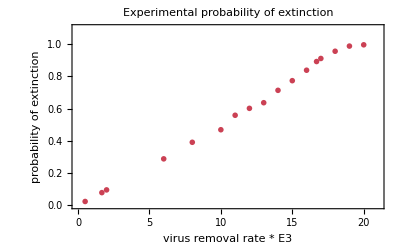

```mathematica
ListPlot[
experimentalList,
PlotStyle->{ColorData["Crayola"][experimentalColor],Thickness[0.010]},
Background->Lighter[Gray, 1.0],
Frame->True,
PlotLabel->Style["Experimental probability of extinction",FontSize->14],
PlotMarkers->{{●,10}},PlotRange->{{0,21},{0,1.1}},
FrameLabel->{{"probability of extinction",""},{"virus removal rate * E3",""}},
PlotLabel->"Experimental probability of extinction"]
```

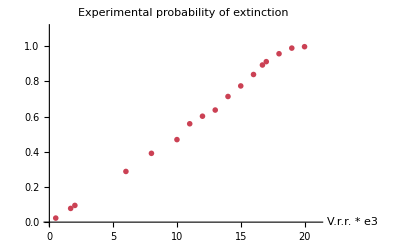

```mathematica
PlotExperimental=ListPlot[experimentalList, 
PlotStyle->{ColorData["Crayola"][experimentalColor],Thickness[0.010]},
PlotMarkers->{{●,10}},PlotRange->{{0,21},{0,1.1}},AxesLabel->{"V.r.r. * e3",""},PlotLabel->"Experimental probability of extinction"]
```

note: for the majority of the curve above we see ~reasonable linearity, the end seems mollified. Towards the end (vrr = 19, 20) we don’t really have E(X)>>1, so the fix point theorem does not hold in itself. (and it is the fix point theorem that gives us linearity at this point)

## Offspring distribution

#### Virus removal rate \in [1.67 , 18] * E-3

```mathematica
VRRString = "18";
VRRNumString="18";
```

```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo"<>VRRString<>".txt", "Table"];
```

Import::nffil: File C:\Users\Juhász Nóra\Documents\GitHub\ABM-PDE\StochasticVariability\theo_results\theo18.txt not found during Import.

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<=dataLength, i++,cleanData=Append[cleanData,data[[i]][[4]]]]
```

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partw: Part 4 of $Failed⟦1⟧ does not exist.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::partw: Part 4 of $Failed⟦2⟧ does not exist.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of $Failed⟦3⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData
```

{}

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

Part::pkspec1: The expression 1+$Failed⟦1⟧⟦4⟧ cannot be used as a part specification.

Set::pkspec1: The expression 1+$Failed⟦1⟧⟦4⟧ cannot be used as a part specification.

Part::pkspec1: The expression 1+$Failed⟦2⟧⟦4⟧ cannot be used as a part specification.

Set::pkspec1: The expression 1+$Failed⟦2⟧⟦4⟧ cannot be used as a part specification.

Part::pkspec1: The expression 1+$Failed⟦3⟧⟦4⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Set::pkspec1: The expression 1+$Failed⟦3⟧⟦4⟧ cannot be used as a part specification.

General::stop: Further output of Set::pkspec1 will be suppressed during this calculation.

```mathematica
probabilityData
```

{}

check if the expected value is > 1 (it is a condition in the fix point theorem)

```mathematica
N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

0.

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartStyle->"Pastel",PlotLabel->"VRR="<>VRRNumString<>"E-3. Shown against geometric distr., Freq. Zero"];
```

Histogram::hbins: The bin specification {0,Max[$Failed⟦1⟧⟦4⟧,$Failed⟦2⟧⟦4⟧,$Failed⟦3⟧⟦4⟧,$Failed⟦4⟧⟦4⟧,$Failed⟦5⟧⟦4⟧,$Failed⟦6⟧⟦4⟧,$Failed⟦7⟧⟦4⟧,$Failed⟦8⟧⟦4⟧,$Failed⟦9⟧⟦4⟧,$Failed⟦10⟧⟦4⟧,«990»],1} cannot be used to determine either how many or which bins to use.

General::stop: Further output of Histogram::hbins will be suppressed during this calculation.

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[probabilityData[[1,2]]/1000],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

Part::partw: Part 1 of {} does not exist.

DiscretePlot::iterb: Iterator {x,0,Max[cleanData]} does not have appropriate bounds.

```mathematica
probabilityData[[1,2]]/1000 //N
```

Part::partw: Part 1 of {} does not exist.

0.001 {}⟦1,2⟧

```mathematica
Rasterize[Show[p1,p2]]
```

DiscretePlot::iterb: Iterator {x,0,Max[cleanData]} does not have appropriate bounds.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[{$Failed⟦1⟧⟦4⟧,$Failed⟦2⟧⟦4⟧,$Failed⟦3⟧⟦4⟧,$Failed⟦4⟧⟦4⟧,$Failed⟦5⟧⟦4⟧,$Failed⟦6⟧⟦4⟧,$Failed⟦7⟧⟦4⟧,$Failed⟦8⟧⟦4⟧,$Failed⟦9⟧⟦4⟧,$Failed⟦10⟧⟦4⟧,«990»},{0,Max[$Failed⟦1⟧⟦4⟧,$Failed⟦2⟧⟦4⟧,$Failed⟦3⟧⟦4⟧,$Failed⟦4⟧⟦4⟧,$Failed⟦5⟧⟦4⟧,$Failed⟦6⟧⟦4⟧,$Failed⟦7⟧⟦4⟧,$Failed⟦8⟧⟦4⟧,$Failed⟦9⟧⟦4⟧,$Failed⟦10⟧⟦4⟧,«990»],1},Probability,ChartStyle→Pastel,PlotLabel→VRR=18E-3. Shown against geometric distr., Freq. Zero],«1»].

-Graphics-

Gábor ötlete: geom param: mintaátlag reciproka, ML becslés; K-S próba.
Végeredmény: melyik param becslés ad jobb illeszkedést.

```mathematica
geohope=1/(Mean[cleanData]+1)
```

1/(1+1/1000($Failed⟦1⟧⟦4⟧+$Failed⟦2⟧⟦4⟧+$Failed⟦3⟧⟦4⟧+$Failed⟦4⟧⟦4⟧+$Failed⟦5⟧⟦4⟧+$Failed⟦6⟧⟦4⟧+$Failed⟦7⟧⟦4⟧+$Failed⟦8⟧⟦4⟧+$Failed⟦9⟧⟦4⟧+$Failed⟦10⟧⟦4⟧+$Failed⟦11⟧⟦4⟧+$Failed⟦12⟧⟦4⟧+$Failed⟦13⟧⟦4⟧+$Failed⟦14⟧⟦4⟧+$Failed⟦15⟧⟦4⟧+$Failed⟦16⟧⟦4⟧+$Failed⟦17⟧⟦4⟧+$Failed⟦18⟧⟦4⟧+$Failed⟦19⟧⟦4⟧+$Failed⟦20⟧⟦4⟧+$Failed⟦21⟧⟦4⟧+$Failed⟦22⟧⟦4⟧+$Failed⟦23⟧⟦4⟧+$Failed⟦24⟧⟦4⟧+$Failed⟦25⟧⟦4⟧+$Failed⟦26⟧⟦4⟧+$Failed⟦27⟧⟦4⟧+$Failed⟦28⟧⟦4⟧+$Failed⟦29⟧⟦4⟧+$Failed⟦30⟧⟦4⟧+$Failed⟦31⟧⟦4⟧+$Failed⟦32⟧⟦4⟧+$Failed⟦33⟧⟦4⟧+$Failed⟦34⟧⟦4⟧+$Failed⟦35⟧⟦4⟧+$Failed⟦36⟧⟦4⟧+$Failed⟦37⟧⟦4⟧+$Failed⟦38⟧⟦4⟧+$Failed⟦39⟧⟦4⟧+$Failed⟦40⟧⟦4⟧+$Failed⟦41⟧⟦4⟧+$Failed⟦42⟧⟦4⟧+$Failed⟦43⟧⟦4⟧+$Failed⟦44⟧⟦4⟧+$Failed⟦45⟧⟦4⟧+$Failed⟦46⟧⟦4⟧+$Failed⟦47⟧⟦4⟧+$Failed⟦48⟧⟦4⟧+$Failed⟦49⟧⟦4⟧+$Failed⟦50⟧⟦4⟧+$Failed⟦51⟧⟦4⟧+$Failed⟦52⟧⟦4⟧+$Failed⟦53⟧⟦4⟧+$Failed⟦54⟧⟦4⟧+$Failed⟦55⟧⟦4⟧+$Failed⟦56⟧⟦4⟧+$Failed⟦57⟧⟦4⟧+$Failed⟦58⟧⟦4⟧+$Failed⟦59⟧⟦4⟧+$Failed⟦60⟧⟦4⟧+$Failed⟦61⟧⟦4⟧+$Failed⟦62⟧⟦4⟧+$Failed⟦63⟧⟦4⟧+$Failed⟦64⟧⟦4⟧+$Failed⟦65⟧⟦4⟧+$Failed⟦66⟧⟦4⟧+$Failed⟦67⟧⟦4⟧+$Failed⟦68⟧⟦4⟧+$Failed⟦69⟧⟦4⟧+$Failed⟦70⟧⟦4⟧+$Failed⟦71⟧⟦4⟧+$Failed⟦72⟧⟦4⟧+$Failed⟦73⟧⟦4⟧+$Failed⟦74⟧⟦4⟧+$Failed⟦75⟧⟦4⟧+$Failed⟦76⟧⟦4⟧+$Failed⟦77⟧⟦4⟧+$Failed⟦78⟧⟦4⟧+$Failed⟦79⟧⟦4⟧+$Failed⟦80⟧⟦4⟧+$Failed⟦81⟧⟦4⟧+$Failed⟦82⟧⟦4⟧+$Failed⟦83⟧⟦4⟧+$Failed⟦84⟧⟦4⟧+$Failed⟦85⟧⟦4⟧+$Failed⟦86⟧⟦4⟧+$Failed⟦87⟧⟦4⟧+$Failed⟦88⟧⟦4⟧+$Failed⟦89⟧⟦4⟧+$Failed⟦90⟧⟦4⟧+$Failed⟦91⟧⟦4⟧+$Failed⟦92⟧⟦4⟧+$Failed⟦93⟧⟦4⟧+$Failed⟦94⟧⟦4⟧+$Failed⟦95⟧⟦4⟧+$Failed⟦96⟧⟦4⟧+$Failed⟦97⟧⟦4⟧+$Failed⟦98⟧⟦4⟧+$Failed⟦99⟧⟦4⟧+$Failed⟦100⟧⟦4⟧+$Failed⟦101⟧⟦4⟧+$Failed⟦102⟧⟦4⟧+$Failed⟦103⟧⟦4⟧+$Failed⟦104⟧⟦4⟧+$Failed⟦105⟧⟦4⟧+$Failed⟦106⟧⟦4⟧+$Failed⟦107⟧⟦4⟧+$Failed⟦108⟧⟦4⟧+$Failed⟦109⟧⟦4⟧+$Failed⟦110⟧⟦4⟧+$Failed⟦111⟧⟦4⟧+$Failed⟦112⟧⟦4⟧+$Failed⟦113⟧⟦4⟧+$Failed⟦114⟧⟦4⟧+$Failed⟦115⟧⟦4⟧+$Failed⟦116⟧⟦4⟧+$Failed⟦117⟧⟦4⟧+$Failed⟦118⟧⟦4⟧+$Failed⟦119⟧⟦4⟧+$Failed⟦120⟧⟦4⟧+$Failed⟦121⟧⟦4⟧+$Failed⟦122⟧⟦4⟧+$Failed⟦123⟧⟦4⟧+$Failed⟦124⟧⟦4⟧+$Failed⟦125⟧⟦4⟧+$Failed⟦126⟧⟦4⟧+$Failed⟦127⟧⟦4⟧+$Failed⟦128⟧⟦4⟧+$Failed⟦129⟧⟦4⟧+$Failed⟦130⟧⟦4⟧+$Failed⟦131⟧⟦4⟧+$Failed⟦132⟧⟦4⟧+$Failed⟦133⟧⟦4⟧+$Failed⟦134⟧⟦4⟧+$Failed⟦135⟧⟦4⟧+$Failed⟦136⟧⟦4⟧+$Failed⟦137⟧⟦4⟧+$Failed⟦138⟧⟦4⟧+$Failed⟦139⟧⟦4⟧+$Failed⟦140⟧⟦4⟧+$Failed⟦141⟧⟦4⟧+$Failed⟦142⟧⟦4⟧+$Failed⟦143⟧⟦4⟧+$Failed⟦144⟧⟦4⟧+$Failed⟦145⟧⟦4⟧+$Failed⟦146⟧⟦4⟧+$Failed⟦147⟧⟦4⟧+$Failed⟦148⟧⟦4⟧+$Failed⟦149⟧⟦4⟧+$Failed⟦150⟧⟦4⟧+$Failed⟦151⟧⟦4⟧+$Failed⟦152⟧⟦4⟧+$Failed⟦153⟧⟦4⟧+$Failed⟦154⟧⟦4⟧+$Failed⟦155⟧⟦4⟧+$Failed⟦156⟧⟦4⟧+$Failed⟦157⟧⟦4⟧+$Failed⟦158⟧⟦4⟧+$Failed⟦159⟧⟦4⟧+$Failed⟦160⟧⟦4⟧+$Failed⟦161⟧⟦4⟧+$Failed⟦162⟧⟦4⟧+$Failed⟦163⟧⟦4⟧+$Failed⟦164⟧⟦4⟧+$Failed⟦165⟧⟦4⟧+$Failed⟦166⟧⟦4⟧+$Failed⟦167⟧⟦4⟧+$Failed⟦168⟧⟦4⟧+$Failed⟦169⟧⟦4⟧+$Failed⟦170⟧⟦4⟧+$Failed⟦171⟧⟦4⟧+$Failed⟦172⟧⟦4⟧+$Failed⟦173⟧⟦4⟧+$Failed⟦174⟧⟦4⟧+$Failed⟦175⟧⟦4⟧+$Failed⟦176⟧⟦4⟧+$Failed⟦177⟧⟦4⟧+$Failed⟦178⟧⟦4⟧+$Failed⟦179⟧⟦4⟧+$Failed⟦180⟧⟦4⟧+$Failed⟦181⟧⟦4⟧+$Failed⟦182⟧⟦4⟧+$Failed⟦183⟧⟦4⟧+$Failed⟦184⟧⟦4⟧+$Failed⟦185⟧⟦4⟧+$Failed⟦186⟧⟦4⟧+$Failed⟦187⟧⟦4⟧+$Failed⟦188⟧⟦4⟧+$Failed⟦189⟧⟦4⟧+$Failed⟦190⟧⟦4⟧+$Failed⟦191⟧⟦4⟧+$Failed⟦192⟧⟦4⟧+$Failed⟦193⟧⟦4⟧+$Failed⟦194⟧⟦4⟧+$Failed⟦195⟧⟦4⟧+$Failed⟦196⟧⟦4⟧+$Failed⟦197⟧⟦4⟧+$Failed⟦198⟧⟦4⟧+$Failed⟦199⟧⟦4⟧+$Failed⟦200⟧⟦4⟧+$Failed⟦201⟧⟦4⟧+$Failed⟦202⟧⟦4⟧+$Failed⟦203⟧⟦4⟧+$Failed⟦204⟧⟦4⟧+$Failed⟦205⟧⟦4⟧+$Failed⟦206⟧⟦4⟧+$Failed⟦207⟧⟦4⟧+$Failed⟦208⟧⟦4⟧+$Failed⟦209⟧⟦4⟧+$Failed⟦210⟧⟦4⟧+$Failed⟦211⟧⟦4⟧+$Failed⟦212⟧⟦4⟧+$Failed⟦213⟧⟦4⟧+$Failed⟦214⟧⟦4⟧+$Failed⟦215⟧⟦4⟧+$Failed⟦216⟧⟦4⟧+$Failed⟦217⟧⟦4⟧+$Failed⟦218⟧⟦4⟧+$Failed⟦219⟧⟦4⟧+$Failed⟦220⟧⟦4⟧+$Failed⟦221⟧⟦4⟧+$Failed⟦222⟧⟦4⟧+$Failed⟦223⟧⟦4⟧+$Failed⟦224⟧⟦4⟧+$Failed⟦225⟧⟦4⟧+$Failed⟦226⟧⟦4⟧+$Failed⟦227⟧⟦4⟧+$Failed⟦228⟧⟦4⟧+$Failed⟦229⟧⟦4⟧+$Failed⟦230⟧⟦4⟧+$Failed⟦231⟧⟦4⟧+$Failed⟦232⟧⟦4⟧+$Failed⟦233⟧⟦4⟧+$Failed⟦234⟧⟦4⟧+$Failed⟦235⟧⟦4⟧+$Failed⟦236⟧⟦4⟧+$Failed⟦237⟧⟦4⟧+$Failed⟦238⟧⟦4⟧+$Failed⟦239⟧⟦4⟧+$Failed⟦240⟧⟦4⟧+$Failed⟦241⟧⟦4⟧+$Failed⟦242⟧⟦4⟧+$Failed⟦243⟧⟦4⟧+$Failed⟦244⟧⟦4⟧+$Failed⟦245⟧⟦4⟧+$Failed⟦246⟧⟦4⟧+$Failed⟦247⟧⟦4⟧+$Failed⟦248⟧⟦4⟧+$Failed⟦249⟧⟦4⟧+$Failed⟦250⟧⟦4⟧+$Failed⟦251⟧⟦4⟧+$Failed⟦252⟧⟦4⟧+$Failed⟦253⟧⟦4⟧+$Failed⟦254⟧⟦4⟧+$Failed⟦255⟧⟦4⟧+$Failed⟦256⟧⟦4⟧+$Failed⟦257⟧⟦4⟧+$Failed⟦258⟧⟦4⟧+$Failed⟦259⟧⟦4⟧+$Failed⟦260⟧⟦4⟧+$Failed⟦261⟧⟦4⟧+$Failed⟦262⟧⟦4⟧+$Failed⟦263⟧⟦4⟧+$Failed⟦264⟧⟦4⟧+$Failed⟦265⟧⟦4⟧+$Failed⟦266⟧⟦4⟧+$Failed⟦267⟧⟦4⟧+$Failed⟦268⟧⟦4⟧+$Failed⟦269⟧⟦4⟧+$Failed⟦270⟧⟦4⟧+$Failed⟦271⟧⟦4⟧+$Failed⟦272⟧⟦4⟧+$Failed⟦273⟧⟦4⟧+$Failed⟦274⟧⟦4⟧+$Failed⟦275⟧⟦4⟧+$Failed⟦276⟧⟦4⟧+$Failed⟦277⟧⟦4⟧+$Failed⟦278⟧⟦4⟧+$Failed⟦279⟧⟦4⟧+$Failed⟦280⟧⟦4⟧+$Failed⟦281⟧⟦4⟧+$Failed⟦282⟧⟦4⟧+$Failed⟦283⟧⟦4⟧+$Failed⟦284⟧⟦4⟧+$Failed⟦285⟧⟦4⟧+$Failed⟦286⟧⟦4⟧+$Failed⟦287⟧⟦4⟧+$Failed⟦288⟧⟦4⟧+$Failed⟦289⟧⟦4⟧+$Failed⟦290⟧⟦4⟧+$Failed⟦291⟧⟦4⟧+$Failed⟦292⟧⟦4⟧+$Failed⟦293⟧⟦4⟧+$Failed⟦294⟧⟦4⟧+$Failed⟦295⟧⟦4⟧+$Failed⟦296⟧⟦4⟧+$Failed⟦297⟧⟦4⟧+$Failed⟦298⟧⟦4⟧+$Failed⟦299⟧⟦4⟧+$Failed⟦300⟧⟦4⟧+$Failed⟦301⟧⟦4⟧+$Failed⟦302⟧⟦4⟧+$Failed⟦303⟧⟦4⟧+$Failed⟦304⟧⟦4⟧+$Failed⟦305⟧⟦4⟧+$Failed⟦306⟧⟦4⟧+$Failed⟦307⟧⟦4⟧+$Failed⟦308⟧⟦4⟧+$Failed⟦309⟧⟦4⟧+$Failed⟦310⟧⟦4⟧+$Failed⟦311⟧⟦4⟧+$Failed⟦312⟧⟦4⟧+$Failed⟦313⟧⟦4⟧+$Failed⟦314⟧⟦4⟧+$Failed⟦315⟧⟦4⟧+$Failed⟦316⟧⟦4⟧+$Failed⟦317⟧⟦4⟧+$Failed⟦318⟧⟦4⟧+$Failed⟦319⟧⟦4⟧+$Failed⟦320⟧⟦4⟧+$Failed⟦321⟧⟦4⟧+$Failed⟦322⟧⟦4⟧+$Failed⟦323⟧⟦4⟧+$Failed⟦324⟧⟦4⟧+$Failed⟦325⟧⟦4⟧+$Failed⟦326⟧⟦4⟧+$Failed⟦327⟧⟦4⟧+$Failed⟦328⟧⟦4⟧+$Failed⟦329⟧⟦4⟧+$Failed⟦330⟧⟦4⟧+$Failed⟦331⟧⟦4⟧+$Failed⟦332⟧⟦4⟧+$Failed⟦333⟧⟦4⟧+$Failed⟦334⟧⟦4⟧+$Failed⟦335⟧⟦4⟧+$Failed⟦336⟧⟦4⟧+$Failed⟦337⟧⟦4⟧+$Failed⟦338⟧⟦4⟧+$Failed⟦339⟧⟦4⟧+$Failed⟦340⟧⟦4⟧+$Failed⟦341⟧⟦4⟧+$Failed⟦342⟧⟦4⟧+$Failed⟦343⟧⟦4⟧+$Failed⟦344⟧⟦4⟧+$Failed⟦345⟧⟦4⟧+$Failed⟦346⟧⟦4⟧+$Failed⟦347⟧⟦4⟧+$Failed⟦348⟧⟦4⟧+$Failed⟦349⟧⟦4⟧+$Failed⟦350⟧⟦4⟧+$Failed⟦351⟧⟦4⟧+$Failed⟦352⟧⟦4⟧+$Failed⟦353⟧⟦4⟧+$Failed⟦354⟧⟦4⟧+$Failed⟦355⟧⟦4⟧+$Failed⟦356⟧⟦4⟧+$Failed⟦357⟧⟦4⟧+$Failed⟦358⟧⟦4⟧+$Failed⟦359⟧⟦4⟧+$Failed⟦360⟧⟦4⟧+$Failed⟦361⟧⟦4⟧+$Failed⟦362⟧⟦4⟧+$Failed⟦363⟧⟦4⟧+$Failed⟦364⟧⟦4⟧+$Failed⟦365⟧⟦4⟧+$Failed⟦366⟧⟦4⟧+$Failed⟦367⟧⟦4⟧+$Failed⟦368⟧⟦4⟧+$Failed⟦369⟧⟦4⟧+$Failed⟦370⟧⟦4⟧+$Failed⟦371⟧⟦4⟧+$Failed⟦372⟧⟦4⟧+$Failed⟦373⟧⟦4⟧+$Failed⟦374⟧⟦4⟧+$Failed⟦375⟧⟦4⟧+$Failed⟦376⟧⟦4⟧+$Failed⟦377⟧⟦4⟧+$Failed⟦378⟧⟦4⟧+$Failed⟦379⟧⟦4⟧+$Failed⟦380⟧⟦4⟧+$Failed⟦381⟧⟦4⟧+$Failed⟦382⟧⟦4⟧+$Failed⟦383⟧⟦4⟧+$Failed⟦384⟧⟦4⟧+$Failed⟦385⟧⟦4⟧+$Failed⟦386⟧⟦4⟧+$Failed⟦387⟧⟦4⟧+$Failed⟦388⟧⟦4⟧+$Failed⟦389⟧⟦4⟧+$Failed⟦390⟧⟦4⟧+$Failed⟦391⟧⟦4⟧+$Failed⟦392⟧⟦4⟧+$Failed⟦393⟧⟦4⟧+$Failed⟦394⟧⟦4⟧+$Failed⟦395⟧⟦4⟧+$Failed⟦396⟧⟦4⟧+$Failed⟦397⟧⟦4⟧+$Failed⟦398⟧⟦4⟧+$Failed⟦399⟧⟦4⟧+$Failed⟦400⟧⟦4⟧+$Failed⟦401⟧⟦4⟧+$Failed⟦402⟧⟦4⟧+$Failed⟦403⟧⟦4⟧+$Failed⟦404⟧⟦4⟧+$Failed⟦405⟧⟦4⟧+$Failed⟦406⟧⟦4⟧+$Failed⟦407⟧⟦4⟧+$Failed⟦408⟧⟦4⟧+$Failed⟦409⟧⟦4⟧+$Failed⟦410⟧⟦4⟧+$Failed⟦411⟧⟦4⟧+$Failed⟦412⟧⟦4⟧+$Failed⟦413⟧⟦4⟧+$Failed⟦414⟧⟦4⟧+$Failed⟦415⟧⟦4⟧+$Failed⟦416⟧⟦4⟧+$Failed⟦417⟧⟦4⟧+$Failed⟦418⟧⟦4⟧+$Failed⟦419⟧⟦4⟧+$Failed⟦420⟧⟦4⟧+$Failed⟦421⟧⟦4⟧+$Failed⟦422⟧⟦4⟧+$Failed⟦423⟧⟦4⟧+$Failed⟦424⟧⟦4⟧+$Failed⟦425⟧⟦4⟧+$Failed⟦426⟧⟦4⟧+$Failed⟦427⟧⟦4⟧+$Failed⟦428⟧⟦4⟧+$Failed⟦429⟧⟦4⟧+$Failed⟦430⟧⟦4⟧+$Failed⟦431⟧⟦4⟧+$Failed⟦432⟧⟦4⟧+$Failed⟦433⟧⟦4⟧+$Failed⟦434⟧⟦4⟧+$Failed⟦435⟧⟦4⟧+$Failed⟦436⟧⟦4⟧+$Failed⟦437⟧⟦4⟧+$Failed⟦438⟧⟦4⟧+$Failed⟦439⟧⟦4⟧+$Failed⟦440⟧⟦4⟧+$Failed⟦441⟧⟦4⟧+$Failed⟦442⟧⟦4⟧+$Failed⟦443⟧⟦4⟧+$Failed⟦444⟧⟦4⟧+$Failed⟦445⟧⟦4⟧+$Failed⟦446⟧⟦4⟧+$Failed⟦447⟧⟦4⟧+$Failed⟦448⟧⟦4⟧+$Failed⟦449⟧⟦4⟧+$Failed⟦450⟧⟦4⟧+$Failed⟦451⟧⟦4⟧+$Failed⟦452⟧⟦4⟧+$Failed⟦453⟧⟦4⟧+$Failed⟦454⟧⟦4⟧+$Failed⟦455⟧⟦4⟧+$Failed⟦456⟧⟦4⟧+$Failed⟦457⟧⟦4⟧+$Failed⟦458⟧⟦4⟧+$Failed⟦459⟧⟦4⟧+$Failed⟦460⟧⟦4⟧+$Failed⟦461⟧⟦4⟧+$Failed⟦462⟧⟦4⟧+$Failed⟦463⟧⟦4⟧+$Failed⟦464⟧⟦4⟧+$Failed⟦465⟧⟦4⟧+$Failed⟦466⟧⟦4⟧+$Failed⟦467⟧⟦4⟧+$Failed⟦468⟧⟦4⟧+$Failed⟦469⟧⟦4⟧+$Failed⟦470⟧⟦4⟧+$Failed⟦471⟧⟦4⟧+$Failed⟦472⟧⟦4⟧+$Failed⟦473⟧⟦4⟧+$Failed⟦474⟧⟦4⟧+$Failed⟦475⟧⟦4⟧+$Failed⟦476⟧⟦4⟧+$Failed⟦477⟧⟦4⟧+$Failed⟦478⟧⟦4⟧+$Failed⟦479⟧⟦4⟧+$Failed⟦480⟧⟦4⟧+$Failed⟦481⟧⟦4⟧+$Failed⟦482⟧⟦4⟧+$Failed⟦483⟧⟦4⟧+$Failed⟦484⟧⟦4⟧+$Failed⟦485⟧⟦4⟧+$Failed⟦486⟧⟦4⟧+$Failed⟦487⟧⟦4⟧+$Failed⟦488⟧⟦4⟧+$Failed⟦489⟧⟦4⟧+$Failed⟦490⟧⟦4⟧+$Failed⟦491⟧⟦4⟧+$Failed⟦492⟧⟦4⟧+$Failed⟦493⟧⟦4⟧+$Failed⟦494⟧⟦4⟧+$Failed⟦495⟧⟦4⟧+$Failed⟦496⟧⟦4⟧+$Failed⟦497⟧⟦4⟧+$Failed⟦498⟧⟦4⟧+$Failed⟦499⟧⟦4⟧+$Failed⟦500⟧⟦4⟧+$Failed⟦501⟧⟦4⟧+$Failed⟦502⟧⟦4⟧+$Failed⟦503⟧⟦4⟧+$Failed⟦504⟧⟦4⟧+$Failed⟦505⟧⟦4⟧+$Failed⟦506⟧⟦4⟧+$Failed⟦507⟧⟦4⟧+$Failed⟦508⟧⟦4⟧+$Failed⟦509⟧⟦4⟧+$Failed⟦510⟧⟦4⟧+$Failed⟦511⟧⟦4⟧+$Failed⟦512⟧⟦4⟧+$Failed⟦513⟧⟦4⟧+$Failed⟦514⟧⟦4⟧+$Failed⟦515⟧⟦4⟧+$Failed⟦516⟧⟦4⟧+$Failed⟦517⟧⟦4⟧+$Failed⟦518⟧⟦4⟧+$Failed⟦519⟧⟦4⟧+$Failed⟦520⟧⟦4⟧+$Failed⟦521⟧⟦4⟧+$Failed⟦522⟧⟦4⟧+$Failed⟦523⟧⟦4⟧+$Failed⟦524⟧⟦4⟧+$Failed⟦525⟧⟦4⟧+$Failed⟦526⟧⟦4⟧+$Failed⟦527⟧⟦4⟧+$Failed⟦528⟧⟦4⟧+$Failed⟦529⟧⟦4⟧+$Failed⟦530⟧⟦4⟧+$Failed⟦531⟧⟦4⟧+$Failed⟦532⟧⟦4⟧+$Failed⟦533⟧⟦4⟧+$Failed⟦534⟧⟦4⟧+$Failed⟦535⟧⟦4⟧+$Failed⟦536⟧⟦4⟧+$Failed⟦537⟧⟦4⟧+$Failed⟦538⟧⟦4⟧+$Failed⟦539⟧⟦4⟧+$Failed⟦540⟧⟦4⟧+$Failed⟦541⟧⟦4⟧+$Failed⟦542⟧⟦4⟧+$Failed⟦543⟧⟦4⟧+$Failed⟦544⟧⟦4⟧+$Failed⟦545⟧⟦4⟧+$Failed⟦546⟧⟦4⟧+$Failed⟦547⟧⟦4⟧+$Failed⟦548⟧⟦4⟧+$Failed⟦549⟧⟦4⟧+$Failed⟦550⟧⟦4⟧+$Failed⟦551⟧⟦4⟧+$Failed⟦552⟧⟦4⟧+$Failed⟦553⟧⟦4⟧+$Failed⟦554⟧⟦4⟧+$Failed⟦555⟧⟦4⟧+$Failed⟦556⟧⟦4⟧+$Failed⟦557⟧⟦4⟧+$Failed⟦558⟧⟦4⟧+$Failed⟦559⟧⟦4⟧+$Failed⟦560⟧⟦4⟧+$Failed⟦561⟧⟦4⟧+$Failed⟦562⟧⟦4⟧+$Failed⟦563⟧⟦4⟧+$Failed⟦564⟧⟦4⟧+$Failed⟦565⟧⟦4⟧+$Failed⟦566⟧⟦4⟧+$Failed⟦567⟧⟦4⟧+$Failed⟦568⟧⟦4⟧+$Failed⟦569⟧⟦4⟧+$Failed⟦570⟧⟦4⟧+$Failed⟦571⟧⟦4⟧+$Failed⟦572⟧⟦4⟧+$Failed⟦573⟧⟦4⟧+$Failed⟦574⟧⟦4⟧+$Failed⟦575⟧⟦4⟧+$Failed⟦576⟧⟦4⟧+$Failed⟦577⟧⟦4⟧+$Failed⟦578⟧⟦4⟧+$Failed⟦579⟧⟦4⟧+$Failed⟦580⟧⟦4⟧+$Failed⟦581⟧⟦4⟧+$Failed⟦582⟧⟦4⟧+$Failed⟦583⟧⟦4⟧+$Failed⟦584⟧⟦4⟧+$Failed⟦585⟧⟦4⟧+$Failed⟦586⟧⟦4⟧+$Failed⟦587⟧⟦4⟧+$Failed⟦588⟧⟦4⟧+$Failed⟦589⟧⟦4⟧+$Failed⟦590⟧⟦4⟧+$Failed⟦591⟧⟦4⟧+$Failed⟦592⟧⟦4⟧+$Failed⟦593⟧⟦4⟧+$Failed⟦594⟧⟦4⟧+$Failed⟦595⟧⟦4⟧+$Failed⟦596⟧⟦4⟧+$Failed⟦597⟧⟦4⟧+$Failed⟦598⟧⟦4⟧+$Failed⟦599⟧⟦4⟧+$Failed⟦600⟧⟦4⟧+$Failed⟦601⟧⟦4⟧+$Failed⟦602⟧⟦4⟧+$Failed⟦603⟧⟦4⟧+$Failed⟦604⟧⟦4⟧+$Failed⟦605⟧⟦4⟧+$Failed⟦606⟧⟦4⟧+$Failed⟦607⟧⟦4⟧+$Failed⟦608⟧⟦4⟧+$Failed⟦609⟧⟦4⟧+$Failed⟦610⟧⟦4⟧+$Failed⟦611⟧⟦4⟧+$Failed⟦612⟧⟦4⟧+$Failed⟦613⟧⟦4⟧+$Failed⟦614⟧⟦4⟧+$Failed⟦615⟧⟦4⟧+$Failed⟦616⟧⟦4⟧+$Failed⟦617⟧⟦4⟧+$Failed⟦618⟧⟦4⟧+$Failed⟦619⟧⟦4⟧+$Failed⟦620⟧⟦4⟧+$Failed⟦621⟧⟦4⟧+$Failed⟦622⟧⟦4⟧+$Failed⟦623⟧⟦4⟧+$Failed⟦624⟧⟦4⟧+$Failed⟦625⟧⟦4⟧+$Failed⟦626⟧⟦4⟧+$Failed⟦627⟧⟦4⟧+$Failed⟦628⟧⟦4⟧+$Failed⟦629⟧⟦4⟧+$Failed⟦630⟧⟦4⟧+$Failed⟦631⟧⟦4⟧+$Failed⟦632⟧⟦4⟧+$Failed⟦633⟧⟦4⟧+$Failed⟦634⟧⟦4⟧+$Failed⟦635⟧⟦4⟧+$Failed⟦636⟧⟦4⟧+$Failed⟦637⟧⟦4⟧+$Failed⟦638⟧⟦4⟧+$Failed⟦639⟧⟦4⟧+$Failed⟦640⟧⟦4⟧+$Failed⟦641⟧⟦4⟧+$Failed⟦642⟧⟦4⟧+$Failed⟦643⟧⟦4⟧+$Failed⟦644⟧⟦4⟧+$Failed⟦645⟧⟦4⟧+$Failed⟦646⟧⟦4⟧+$Failed⟦647⟧⟦4⟧+$Failed⟦648⟧⟦4⟧+$Failed⟦649⟧⟦4⟧+$Failed⟦650⟧⟦4⟧+$Failed⟦651⟧⟦4⟧+$Failed⟦652⟧⟦4⟧+$Failed⟦653⟧⟦4⟧+$Failed⟦654⟧⟦4⟧+$Failed⟦655⟧⟦4⟧+$Failed⟦656⟧⟦4⟧+$Failed⟦657⟧⟦4⟧+$Failed⟦658⟧⟦4⟧+$Failed⟦659⟧⟦4⟧+$Failed⟦660⟧⟦4⟧+$Failed⟦661⟧⟦4⟧+$Failed⟦662⟧⟦4⟧+$Failed⟦663⟧⟦4⟧+$Failed⟦664⟧⟦4⟧+$Failed⟦665⟧⟦4⟧+$Failed⟦666⟧⟦4⟧+$Failed⟦667⟧⟦4⟧+$Failed⟦668⟧⟦4⟧+$Failed⟦669⟧⟦4⟧+$Failed⟦670⟧⟦4⟧+$Failed⟦671⟧⟦4⟧+$Failed⟦672⟧⟦4⟧+$Failed⟦673⟧⟦4⟧+$Failed⟦674⟧⟦4⟧+$Failed⟦675⟧⟦4⟧+$Failed⟦676⟧⟦4⟧+$Failed⟦677⟧⟦4⟧+$Failed⟦678⟧⟦4⟧+$Failed⟦679⟧⟦4⟧+$Failed⟦680⟧⟦4⟧+$Failed⟦681⟧⟦4⟧+$Failed⟦682⟧⟦4⟧+$Failed⟦683⟧⟦4⟧+$Failed⟦684⟧⟦4⟧+$Failed⟦685⟧⟦4⟧+$Failed⟦686⟧⟦4⟧+$Failed⟦687⟧⟦4⟧+$Failed⟦688⟧⟦4⟧+$Failed⟦689⟧⟦4⟧+$Failed⟦690⟧⟦4⟧+$Failed⟦691⟧⟦4⟧+$Failed⟦692⟧⟦4⟧+$Failed⟦693⟧⟦4⟧+$Failed⟦694⟧⟦4⟧+$Failed⟦695⟧⟦4⟧+$Failed⟦696⟧⟦4⟧+$Failed⟦697⟧⟦4⟧+$Failed⟦698⟧⟦4⟧+$Failed⟦699⟧⟦4⟧+$Failed⟦700⟧⟦4⟧+$Failed⟦701⟧⟦4⟧+$Failed⟦702⟧⟦4⟧+$Failed⟦703⟧⟦4⟧+$Failed⟦704⟧⟦4⟧+$Failed⟦705⟧⟦4⟧+$Failed⟦706⟧⟦4⟧+$Failed⟦707⟧⟦4⟧+$Failed⟦708⟧⟦4⟧+$Failed⟦709⟧⟦4⟧+$Failed⟦710⟧⟦4⟧+$Failed⟦711⟧⟦4⟧+$Failed⟦712⟧⟦4⟧+$Failed⟦713⟧⟦4⟧+$Failed⟦714⟧⟦4⟧+$Failed⟦715⟧⟦4⟧+$Failed⟦716⟧⟦4⟧+$Failed⟦717⟧⟦4⟧+$Failed⟦718⟧⟦4⟧+$Failed⟦719⟧⟦4⟧+$Failed⟦720⟧⟦4⟧+$Failed⟦721⟧⟦4⟧+$Failed⟦722⟧⟦4⟧+$Failed⟦723⟧⟦4⟧+$Failed⟦724⟧⟦4⟧+$Failed⟦725⟧⟦4⟧+$Failed⟦726⟧⟦4⟧+$Failed⟦727⟧⟦4⟧+$Failed⟦728⟧⟦4⟧+$Failed⟦729⟧⟦4⟧+$Failed⟦730⟧⟦4⟧+$Failed⟦731⟧⟦4⟧+$Failed⟦732⟧⟦4⟧+$Failed⟦733⟧⟦4⟧+$Failed⟦734⟧⟦4⟧+$Failed⟦735⟧⟦4⟧+$Failed⟦736⟧⟦4⟧+$Failed⟦737⟧⟦4⟧+$Failed⟦738⟧⟦4⟧+$Failed⟦739⟧⟦4⟧+$Failed⟦740⟧⟦4⟧+$Failed⟦741⟧⟦4⟧+$Failed⟦742⟧⟦4⟧+$Failed⟦743⟧⟦4⟧+$Failed⟦744⟧⟦4⟧+$Failed⟦745⟧⟦4⟧+$Failed⟦746⟧⟦4⟧+$Failed⟦747⟧⟦4⟧+$Failed⟦748⟧⟦4⟧+$Failed⟦749⟧⟦4⟧+$Failed⟦750⟧⟦4⟧+$Failed⟦751⟧⟦4⟧+$Failed⟦752⟧⟦4⟧+$Failed⟦753⟧⟦4⟧+$Failed⟦754⟧⟦4⟧+$Failed⟦755⟧⟦4⟧+$Failed⟦756⟧⟦4⟧+$Failed⟦757⟧⟦4⟧+$Failed⟦758⟧⟦4⟧+$Failed⟦759⟧⟦4⟧+$Failed⟦760⟧⟦4⟧+$Failed⟦761⟧⟦4⟧+$Failed⟦762⟧⟦4⟧+$Failed⟦763⟧⟦4⟧+$Failed⟦764⟧⟦4⟧+$Failed⟦765⟧⟦4⟧+$Failed⟦766⟧⟦4⟧+$Failed⟦767⟧⟦4⟧+$Failed⟦768⟧⟦4⟧+$Failed⟦769⟧⟦4⟧+$Failed⟦770⟧⟦4⟧+$Failed⟦771⟧⟦4⟧+$Failed⟦772⟧⟦4⟧+$Failed⟦773⟧⟦4⟧+$Failed⟦774⟧⟦4⟧+$Failed⟦775⟧⟦4⟧+$Failed⟦776⟧⟦4⟧+$Failed⟦777⟧⟦4⟧+$Failed⟦778⟧⟦4⟧+$Failed⟦779⟧⟦4⟧+$Failed⟦780⟧⟦4⟧+$Failed⟦781⟧⟦4⟧+$Failed⟦782⟧⟦4⟧+$Failed⟦783⟧⟦4⟧+$Failed⟦784⟧⟦4⟧+$Failed⟦785⟧⟦4⟧+$Failed⟦786⟧⟦4⟧+$Failed⟦787⟧⟦4⟧+$Failed⟦788⟧⟦4⟧+$Failed⟦789⟧⟦4⟧+$Failed⟦790⟧⟦4⟧+$Failed⟦791⟧⟦4⟧+$Failed⟦792⟧⟦4⟧+$Failed⟦793⟧⟦4⟧+$Failed⟦794⟧⟦4⟧+$Failed⟦795⟧⟦4⟧+$Failed⟦796⟧⟦4⟧+$Failed⟦797⟧⟦4⟧+$Failed⟦798⟧⟦4⟧+$Failed⟦799⟧⟦4⟧+$Failed⟦800⟧⟦4⟧+$Failed⟦801⟧⟦4⟧+$Failed⟦802⟧⟦4⟧+$Failed⟦803⟧⟦4⟧+$Failed⟦804⟧⟦4⟧+$Failed⟦805⟧⟦4⟧+$Failed⟦806⟧⟦4⟧+$Failed⟦807⟧⟦4⟧+$Failed⟦808⟧⟦4⟧+$Failed⟦809⟧⟦4⟧+$Failed⟦810⟧⟦4⟧+$Failed⟦811⟧⟦4⟧+$Failed⟦812⟧⟦4⟧+$Failed⟦813⟧⟦4⟧+$Failed⟦814⟧⟦4⟧+$Failed⟦815⟧⟦4⟧+$Failed⟦816⟧⟦4⟧+$Failed⟦817⟧⟦4⟧+$Failed⟦818⟧⟦4⟧+$Failed⟦819⟧⟦4⟧+$Failed⟦820⟧⟦4⟧+$Failed⟦821⟧⟦4⟧+$Failed⟦822⟧⟦4⟧+$Failed⟦823⟧⟦4⟧+$Failed⟦824⟧⟦4⟧+$Failed⟦825⟧⟦4⟧+$Failed⟦826⟧⟦4⟧+$Failed⟦827⟧⟦4⟧+$Failed⟦828⟧⟦4⟧+$Failed⟦829⟧⟦4⟧+$Failed⟦830⟧⟦4⟧+$Failed⟦831⟧⟦4⟧+$Failed⟦832⟧⟦4⟧+$Failed⟦833⟧⟦4⟧+$Failed⟦834⟧⟦4⟧+$Failed⟦835⟧⟦4⟧+$Failed⟦836⟧⟦4⟧+$Failed⟦837⟧⟦4⟧+$Failed⟦838⟧⟦4⟧+$Failed⟦839⟧⟦4⟧+$Failed⟦840⟧⟦4⟧+$Failed⟦841⟧⟦4⟧+$Failed⟦842⟧⟦4⟧+$Failed⟦843⟧⟦4⟧+$Failed⟦844⟧⟦4⟧+$Failed⟦845⟧⟦4⟧+$Failed⟦846⟧⟦4⟧+$Failed⟦847⟧⟦4⟧+$Failed⟦848⟧⟦4⟧+$Failed⟦849⟧⟦4⟧+$Failed⟦850⟧⟦4⟧+$Failed⟦851⟧⟦4⟧+$Failed⟦852⟧⟦4⟧+$Failed⟦853⟧⟦4⟧+$Failed⟦854⟧⟦4⟧+$Failed⟦855⟧⟦4⟧+$Failed⟦856⟧⟦4⟧+$Failed⟦857⟧⟦4⟧+$Failed⟦858⟧⟦4⟧+$Failed⟦859⟧⟦4⟧+$Failed⟦860⟧⟦4⟧+$Failed⟦861⟧⟦4⟧+$Failed⟦862⟧⟦4⟧+$Failed⟦863⟧⟦4⟧+$Failed⟦864⟧⟦4⟧+$Failed⟦865⟧⟦4⟧+$Failed⟦866⟧⟦4⟧+$Failed⟦867⟧⟦4⟧+$Failed⟦868⟧⟦4⟧+$Failed⟦869⟧⟦4⟧+$Failed⟦870⟧⟦4⟧+$Failed⟦871⟧⟦4⟧+$Failed⟦872⟧⟦4⟧+$Failed⟦873⟧⟦4⟧+$Failed⟦874⟧⟦4⟧+$Failed⟦875⟧⟦4⟧+$Failed⟦876⟧⟦4⟧+$Failed⟦877⟧⟦4⟧+$Failed⟦878⟧⟦4⟧+$Failed⟦879⟧⟦4⟧+$Failed⟦880⟧⟦4⟧+$Failed⟦881⟧⟦4⟧+$Failed⟦882⟧⟦4⟧+$Failed⟦883⟧⟦4⟧+$Failed⟦884⟧⟦4⟧+$Failed⟦885⟧⟦4⟧+$Failed⟦886⟧⟦4⟧+$Failed⟦887⟧⟦4⟧+$Failed⟦888⟧⟦4⟧+$Failed⟦889⟧⟦4⟧+$Failed⟦890⟧⟦4⟧+$Failed⟦891⟧⟦4⟧+$Failed⟦892⟧⟦4⟧+$Failed⟦893⟧⟦4⟧+$Failed⟦894⟧⟦4⟧+$Failed⟦895⟧⟦4⟧+$Failed⟦896⟧⟦4⟧+$Failed⟦897⟧⟦4⟧+$Failed⟦898⟧⟦4⟧+$Failed⟦899⟧⟦4⟧+$Failed⟦900⟧⟦4⟧+$Failed⟦901⟧⟦4⟧+$Failed⟦902⟧⟦4⟧+$Failed⟦903⟧⟦4⟧+$Failed⟦904⟧⟦4⟧+$Failed⟦905⟧⟦4⟧+$Failed⟦906⟧⟦4⟧+$Failed⟦907⟧⟦4⟧+$Failed⟦908⟧⟦4⟧+$Failed⟦909⟧⟦4⟧+$Failed⟦910⟧⟦4⟧+$Failed⟦911⟧⟦4⟧+$Failed⟦912⟧⟦4⟧+$Failed⟦913⟧⟦4⟧+$Failed⟦914⟧⟦4⟧+$Failed⟦915⟧⟦4⟧+$Failed⟦916⟧⟦4⟧+$Failed⟦917⟧⟦4⟧+$Failed⟦918⟧⟦4⟧+$Failed⟦919⟧⟦4⟧+$Failed⟦920⟧⟦4⟧+$Failed⟦921⟧⟦4⟧+$Failed⟦922⟧⟦4⟧+$Failed⟦923⟧⟦4⟧+$Failed⟦924⟧⟦4⟧+$Failed⟦925⟧⟦4⟧+$Failed⟦926⟧⟦4⟧+$Failed⟦927⟧⟦4⟧+$Failed⟦928⟧⟦4⟧+$Failed⟦929⟧⟦4⟧+$Failed⟦930⟧⟦4⟧+$Failed⟦931⟧⟦4⟧+$Failed⟦932⟧⟦4⟧+$Failed⟦933⟧⟦4⟧+$Failed⟦934⟧⟦4⟧+$Failed⟦935⟧⟦4⟧+$Failed⟦936⟧⟦4⟧+$Failed⟦937⟧⟦4⟧+$Failed⟦938⟧⟦4⟧+$Failed⟦939⟧⟦4⟧+$Failed⟦940⟧⟦4⟧+$Failed⟦941⟧⟦4⟧+$Failed⟦942⟧⟦4⟧+$Failed⟦943⟧⟦4⟧+$Failed⟦944⟧⟦4⟧+$Failed⟦945⟧⟦4⟧+$Failed⟦946⟧⟦4⟧+$Failed⟦947⟧⟦4⟧+$Failed⟦948⟧⟦4⟧+$Failed⟦949⟧⟦4⟧+$Failed⟦950⟧⟦4⟧+$Failed⟦951⟧⟦4⟧+$Failed⟦952⟧⟦4⟧+$Failed⟦953⟧⟦4⟧+$Failed⟦954⟧⟦4⟧+$Failed⟦955⟧⟦4⟧+$Failed⟦956⟧⟦4⟧+$Failed⟦957⟧⟦4⟧+$Failed⟦958⟧⟦4⟧+$Failed⟦959⟧⟦4⟧+$Failed⟦960⟧⟦4⟧+$Failed⟦961⟧⟦4⟧+$Failed⟦962⟧⟦4⟧+$Failed⟦963⟧⟦4⟧+$Failed⟦964⟧⟦4⟧+$Failed⟦965⟧⟦4⟧+$Failed⟦966⟧⟦4⟧+$Failed⟦967⟧⟦4⟧+$Failed⟦968⟧⟦4⟧+$Failed⟦969⟧⟦4⟧+$Failed⟦970⟧⟦4⟧+$Failed⟦971⟧⟦4⟧+$Failed⟦972⟧⟦4⟧+$Failed⟦973⟧⟦4⟧+$Failed⟦974⟧⟦4⟧+$Failed⟦975⟧⟦4⟧+$Failed⟦976⟧⟦4⟧+$Failed⟦977⟧⟦4⟧+$Failed⟦978⟧⟦4⟧+$Failed⟦979⟧⟦4⟧+$Failed⟦980⟧⟦4⟧+$Failed⟦981⟧⟦4⟧+$Failed⟦982⟧⟦4⟧+$Failed⟦983⟧⟦4⟧+$Failed⟦984⟧⟦4⟧+$Failed⟦985⟧⟦4⟧+$Failed⟦986⟧⟦4⟧+$Failed⟦987⟧⟦4⟧+$Failed⟦988⟧⟦4⟧+$Failed⟦989⟧⟦4⟧+$Failed⟦990⟧⟦4⟧+$Failed⟦991⟧⟦4⟧+$Failed⟦992⟧⟦4⟧+$Failed⟦993⟧⟦4⟧+$Failed⟦994⟧⟦4⟧+$Failed⟦995⟧⟦4⟧+$Failed⟦996⟧⟦4⟧+$Failed⟦997⟧⟦4⟧+$Failed⟦998⟧⟦4⟧+$Failed⟦999⟧⟦4⟧+$Failed⟦1000⟧⟦4⟧))

```mathematica
Max[cleanData]
```

Max[$Failed⟦1⟧⟦4⟧,$Failed⟦2⟧⟦4⟧,$Failed⟦3⟧⟦4⟧,$Failed⟦4⟧⟦4⟧,$Failed⟦5⟧⟦4⟧,$Failed⟦6⟧⟦4⟧,$Failed⟦7⟧⟦4⟧,$Failed⟦8⟧⟦4⟧,$Failed⟦9⟧⟦4⟧,$Failed⟦10⟧⟦4⟧,$Failed⟦11⟧⟦4⟧,$Failed⟦12⟧⟦4⟧,$Failed⟦13⟧⟦4⟧,$Failed⟦14⟧⟦4⟧,$Failed⟦15⟧⟦4⟧,$Failed⟦16⟧⟦4⟧,$Failed⟦17⟧⟦4⟧,$Failed⟦18⟧⟦4⟧,$Failed⟦19⟧⟦4⟧,$Failed⟦20⟧⟦4⟧,$Failed⟦21⟧⟦4⟧,$Failed⟦22⟧⟦4⟧,$Failed⟦23⟧⟦4⟧,$Failed⟦24⟧⟦4⟧,$Failed⟦25⟧⟦4⟧,$Failed⟦26⟧⟦4⟧,$Failed⟦27⟧⟦4⟧,$Failed⟦28⟧⟦4⟧,$Failed⟦29⟧⟦4⟧,$Failed⟦30⟧⟦4⟧,$Failed⟦31⟧⟦4⟧,$Failed⟦32⟧⟦4⟧,$Failed⟦33⟧⟦4⟧,$Failed⟦34⟧⟦4⟧,$Failed⟦35⟧⟦4⟧,$Failed⟦36⟧⟦4⟧,$Failed⟦37⟧⟦4⟧,$Failed⟦38⟧⟦4⟧,$Failed⟦39⟧⟦4⟧,$Failed⟦40⟧⟦4⟧,$Failed⟦41⟧⟦4⟧,$Failed⟦42⟧⟦4⟧,$Failed⟦43⟧⟦4⟧,$Failed⟦44⟧⟦4⟧,$Failed⟦45⟧⟦4⟧,$Failed⟦46⟧⟦4⟧,$Failed⟦47⟧⟦4⟧,$Failed⟦48⟧⟦4⟧,$Failed⟦49⟧⟦4⟧,$Failed⟦50⟧⟦4⟧,$Failed⟦51⟧⟦4⟧,$Failed⟦52⟧⟦4⟧,$Failed⟦53⟧⟦4⟧,$Failed⟦54⟧⟦4⟧,$Failed⟦55⟧⟦4⟧,$Failed⟦56⟧⟦4⟧,$Failed⟦57⟧⟦4⟧,$Failed⟦58⟧⟦4⟧,$Failed⟦59⟧⟦4⟧,$Failed⟦60⟧⟦4⟧,$Failed⟦61⟧⟦4⟧,$Failed⟦62⟧⟦4⟧,$Failed⟦63⟧⟦4⟧,$Failed⟦64⟧⟦4⟧,$Failed⟦65⟧⟦4⟧,$Failed⟦66⟧⟦4⟧,$Failed⟦67⟧⟦4⟧,$Failed⟦68⟧⟦4⟧,$Failed⟦69⟧⟦4⟧,$Failed⟦70⟧⟦4⟧,$Failed⟦71⟧⟦4⟧,$Failed⟦72⟧⟦4⟧,$Failed⟦73⟧⟦4⟧,$Failed⟦74⟧⟦4⟧,$Failed⟦75⟧⟦4⟧,$Failed⟦76⟧⟦4⟧,$Failed⟦77⟧⟦4⟧,$Failed⟦78⟧⟦4⟧,$Failed⟦79⟧⟦4⟧,$Failed⟦80⟧⟦4⟧,$Failed⟦81⟧⟦4⟧,$Failed⟦82⟧⟦4⟧,$Failed⟦83⟧⟦4⟧,$Failed⟦84⟧⟦4⟧,$Failed⟦85⟧⟦4⟧,$Failed⟦86⟧⟦4⟧,$Failed⟦87⟧⟦4⟧,$Failed⟦88⟧⟦4⟧,$Failed⟦89⟧⟦4⟧,$Failed⟦90⟧⟦4⟧,$Failed⟦91⟧⟦4⟧,$Failed⟦92⟧⟦4⟧,$Failed⟦93⟧⟦4⟧,$Failed⟦94⟧⟦4⟧,$Failed⟦95⟧⟦4⟧,$Failed⟦96⟧⟦4⟧,$Failed⟦97⟧⟦4⟧,$Failed⟦98⟧⟦4⟧,$Failed⟦99⟧⟦4⟧,$Failed⟦100⟧⟦4⟧,$Failed⟦101⟧⟦4⟧,$Failed⟦102⟧⟦4⟧,$Failed⟦103⟧⟦4⟧,$Failed⟦104⟧⟦4⟧,$Failed⟦105⟧⟦4⟧,$Failed⟦106⟧⟦4⟧,$Failed⟦107⟧⟦4⟧,$Failed⟦108⟧⟦4⟧,$Failed⟦109⟧⟦4⟧,$Failed⟦110⟧⟦4⟧,$Failed⟦111⟧⟦4⟧,$Failed⟦112⟧⟦4⟧,$Failed⟦113⟧⟦4⟧,$Failed⟦114⟧⟦4⟧,$Failed⟦115⟧⟦4⟧,$Failed⟦116⟧⟦4⟧,$Failed⟦117⟧⟦4⟧,$Failed⟦118⟧⟦4⟧,$Failed⟦119⟧⟦4⟧,$Failed⟦120⟧⟦4⟧,$Failed⟦121⟧⟦4⟧,$Failed⟦122⟧⟦4⟧,$Failed⟦123⟧⟦4⟧,$Failed⟦124⟧⟦4⟧,$Failed⟦125⟧⟦4⟧,$Failed⟦126⟧⟦4⟧,$Failed⟦127⟧⟦4⟧,$Failed⟦128⟧⟦4⟧,$Failed⟦129⟧⟦4⟧,$Failed⟦130⟧⟦4⟧,$Failed⟦131⟧⟦4⟧,$Failed⟦132⟧⟦4⟧,$Failed⟦133⟧⟦4⟧,$Failed⟦134⟧⟦4⟧,$Failed⟦135⟧⟦4⟧,$Failed⟦136⟧⟦4⟧,$Failed⟦137⟧⟦4⟧,$Failed⟦138⟧⟦4⟧,$Failed⟦139⟧⟦4⟧,$Failed⟦140⟧⟦4⟧,$Failed⟦141⟧⟦4⟧,$Failed⟦142⟧⟦4⟧,$Failed⟦143⟧⟦4⟧,$Failed⟦144⟧⟦4⟧,$Failed⟦145⟧⟦4⟧,$Failed⟦146⟧⟦4⟧,$Failed⟦147⟧⟦4⟧,$Failed⟦148⟧⟦4⟧,$Failed⟦149⟧⟦4⟧,$Failed⟦150⟧⟦4⟧,$Failed⟦151⟧⟦4⟧,$Failed⟦152⟧⟦4⟧,$Failed⟦153⟧⟦4⟧,$Failed⟦154⟧⟦4⟧,$Failed⟦155⟧⟦4⟧,$Failed⟦156⟧⟦4⟧,$Failed⟦157⟧⟦4⟧,$Failed⟦158⟧⟦4⟧,$Failed⟦159⟧⟦4⟧,$Failed⟦160⟧⟦4⟧,$Failed⟦161⟧⟦4⟧,$Failed⟦162⟧⟦4⟧,$Failed⟦163⟧⟦4⟧,$Failed⟦164⟧⟦4⟧,$Failed⟦165⟧⟦4⟧,$Failed⟦166⟧⟦4⟧,$Failed⟦167⟧⟦4⟧,$Failed⟦168⟧⟦4⟧,$Failed⟦169⟧⟦4⟧,$Failed⟦170⟧⟦4⟧,$Failed⟦171⟧⟦4⟧,$Failed⟦172⟧⟦4⟧,$Failed⟦173⟧⟦4⟧,$Failed⟦174⟧⟦4⟧,$Failed⟦175⟧⟦4⟧,$Failed⟦176⟧⟦4⟧,$Failed⟦177⟧⟦4⟧,$Failed⟦178⟧⟦4⟧,$Failed⟦179⟧⟦4⟧,$Failed⟦180⟧⟦4⟧,$Failed⟦181⟧⟦4⟧,$Failed⟦182⟧⟦4⟧,$Failed⟦183⟧⟦4⟧,$Failed⟦184⟧⟦4⟧,$Failed⟦185⟧⟦4⟧,$Failed⟦186⟧⟦4⟧,$Failed⟦187⟧⟦4⟧,$Failed⟦188⟧⟦4⟧,$Failed⟦189⟧⟦4⟧,$Failed⟦190⟧⟦4⟧,$Failed⟦191⟧⟦4⟧,$Failed⟦192⟧⟦4⟧,$Failed⟦193⟧⟦4⟧,$Failed⟦194⟧⟦4⟧,$Failed⟦195⟧⟦4⟧,$Failed⟦196⟧⟦4⟧,$Failed⟦197⟧⟦4⟧,$Failed⟦198⟧⟦4⟧,$Failed⟦199⟧⟦4⟧,$Failed⟦200⟧⟦4⟧,$Failed⟦201⟧⟦4⟧,$Failed⟦202⟧⟦4⟧,$Failed⟦203⟧⟦4⟧,$Failed⟦204⟧⟦4⟧,$Failed⟦205⟧⟦4⟧,$Failed⟦206⟧⟦4⟧,$Failed⟦207⟧⟦4⟧,$Failed⟦208⟧⟦4⟧,$Failed⟦209⟧⟦4⟧,$Failed⟦210⟧⟦4⟧,$Failed⟦211⟧⟦4⟧,$Failed⟦212⟧⟦4⟧,$Failed⟦213⟧⟦4⟧,$Failed⟦214⟧⟦4⟧,$Failed⟦215⟧⟦4⟧,$Failed⟦216⟧⟦4⟧,$Failed⟦217⟧⟦4⟧,$Failed⟦218⟧⟦4⟧,$Failed⟦219⟧⟦4⟧,$Failed⟦220⟧⟦4⟧,$Failed⟦221⟧⟦4⟧,$Failed⟦222⟧⟦4⟧,$Failed⟦223⟧⟦4⟧,$Failed⟦224⟧⟦4⟧,$Failed⟦225⟧⟦4⟧,$Failed⟦226⟧⟦4⟧,$Failed⟦227⟧⟦4⟧,$Failed⟦228⟧⟦4⟧,$Failed⟦229⟧⟦4⟧,$Failed⟦230⟧⟦4⟧,$Failed⟦231⟧⟦4⟧,$Failed⟦232⟧⟦4⟧,$Failed⟦233⟧⟦4⟧,$Failed⟦234⟧⟦4⟧,$Failed⟦235⟧⟦4⟧,$Failed⟦236⟧⟦4⟧,$Failed⟦237⟧⟦4⟧,$Failed⟦238⟧⟦4⟧,$Failed⟦239⟧⟦4⟧,$Failed⟦240⟧⟦4⟧,$Failed⟦241⟧⟦4⟧,$Failed⟦242⟧⟦4⟧,$Failed⟦243⟧⟦4⟧,$Failed⟦244⟧⟦4⟧,$Failed⟦245⟧⟦4⟧,$Failed⟦246⟧⟦4⟧,$Failed⟦247⟧⟦4⟧,$Failed⟦248⟧⟦4⟧,$Failed⟦249⟧⟦4⟧,$Failed⟦250⟧⟦4⟧,$Failed⟦251⟧⟦4⟧,$Failed⟦252⟧⟦4⟧,$Failed⟦253⟧⟦4⟧,$Failed⟦254⟧⟦4⟧,$Failed⟦255⟧⟦4⟧,$Failed⟦256⟧⟦4⟧,$Failed⟦257⟧⟦4⟧,$Failed⟦258⟧⟦4⟧,$Failed⟦259⟧⟦4⟧,$Failed⟦260⟧⟦4⟧,$Failed⟦261⟧⟦4⟧,$Failed⟦262⟧⟦4⟧,$Failed⟦263⟧⟦4⟧,$Failed⟦264⟧⟦4⟧,$Failed⟦265⟧⟦4⟧,$Failed⟦266⟧⟦4⟧,$Failed⟦267⟧⟦4⟧,$Failed⟦268⟧⟦4⟧,$Failed⟦269⟧⟦4⟧,$Failed⟦270⟧⟦4⟧,$Failed⟦271⟧⟦4⟧,$Failed⟦272⟧⟦4⟧,$Failed⟦273⟧⟦4⟧,$Failed⟦274⟧⟦4⟧,$Failed⟦275⟧⟦4⟧,$Failed⟦276⟧⟦4⟧,$Failed⟦277⟧⟦4⟧,$Failed⟦278⟧⟦4⟧,$Failed⟦279⟧⟦4⟧,$Failed⟦280⟧⟦4⟧,$Failed⟦281⟧⟦4⟧,$Failed⟦282⟧⟦4⟧,$Failed⟦283⟧⟦4⟧,$Failed⟦284⟧⟦4⟧,$Failed⟦285⟧⟦4⟧,$Failed⟦286⟧⟦4⟧,$Failed⟦287⟧⟦4⟧,$Failed⟦288⟧⟦4⟧,$Failed⟦289⟧⟦4⟧,$Failed⟦290⟧⟦4⟧,$Failed⟦291⟧⟦4⟧,$Failed⟦292⟧⟦4⟧,$Failed⟦293⟧⟦4⟧,$Failed⟦294⟧⟦4⟧,$Failed⟦295⟧⟦4⟧,$Failed⟦296⟧⟦4⟧,$Failed⟦297⟧⟦4⟧,$Failed⟦298⟧⟦4⟧,$Failed⟦299⟧⟦4⟧,$Failed⟦300⟧⟦4⟧,$Failed⟦301⟧⟦4⟧,$Failed⟦302⟧⟦4⟧,$Failed⟦303⟧⟦4⟧,$Failed⟦304⟧⟦4⟧,$Failed⟦305⟧⟦4⟧,$Failed⟦306⟧⟦4⟧,$Failed⟦307⟧⟦4⟧,$Failed⟦308⟧⟦4⟧,$Failed⟦309⟧⟦4⟧,$Failed⟦310⟧⟦4⟧,$Failed⟦311⟧⟦4⟧,$Failed⟦312⟧⟦4⟧,$Failed⟦313⟧⟦4⟧,$Failed⟦314⟧⟦4⟧,$Failed⟦315⟧⟦4⟧,$Failed⟦316⟧⟦4⟧,$Failed⟦317⟧⟦4⟧,$Failed⟦318⟧⟦4⟧,$Failed⟦319⟧⟦4⟧,$Failed⟦320⟧⟦4⟧,$Failed⟦321⟧⟦4⟧,$Failed⟦322⟧⟦4⟧,$Failed⟦323⟧⟦4⟧,$Failed⟦324⟧⟦4⟧,$Failed⟦325⟧⟦4⟧,$Failed⟦326⟧⟦4⟧,$Failed⟦327⟧⟦4⟧,$Failed⟦328⟧⟦4⟧,$Failed⟦329⟧⟦4⟧,$Failed⟦330⟧⟦4⟧,$Failed⟦331⟧⟦4⟧,$Failed⟦332⟧⟦4⟧,$Failed⟦333⟧⟦4⟧,$Failed⟦334⟧⟦4⟧,$Failed⟦335⟧⟦4⟧,$Failed⟦336⟧⟦4⟧,$Failed⟦337⟧⟦4⟧,$Failed⟦338⟧⟦4⟧,$Failed⟦339⟧⟦4⟧,$Failed⟦340⟧⟦4⟧,$Failed⟦341⟧⟦4⟧,$Failed⟦342⟧⟦4⟧,$Failed⟦343⟧⟦4⟧,$Failed⟦344⟧⟦4⟧,$Failed⟦345⟧⟦4⟧,$Failed⟦346⟧⟦4⟧,$Failed⟦347⟧⟦4⟧,$Failed⟦348⟧⟦4⟧,$Failed⟦349⟧⟦4⟧,$Failed⟦350⟧⟦4⟧,$Failed⟦351⟧⟦4⟧,$Failed⟦352⟧⟦4⟧,$Failed⟦353⟧⟦4⟧,$Failed⟦354⟧⟦4⟧,$Failed⟦355⟧⟦4⟧,$Failed⟦356⟧⟦4⟧,$Failed⟦357⟧⟦4⟧,$Failed⟦358⟧⟦4⟧,$Failed⟦359⟧⟦4⟧,$Failed⟦360⟧⟦4⟧,$Failed⟦361⟧⟦4⟧,$Failed⟦362⟧⟦4⟧,$Failed⟦363⟧⟦4⟧,$Failed⟦364⟧⟦4⟧,$Failed⟦365⟧⟦4⟧,$Failed⟦366⟧⟦4⟧,$Failed⟦367⟧⟦4⟧,$Failed⟦368⟧⟦4⟧,$Failed⟦369⟧⟦4⟧,$Failed⟦370⟧⟦4⟧,$Failed⟦371⟧⟦4⟧,$Failed⟦372⟧⟦4⟧,$Failed⟦373⟧⟦4⟧,$Failed⟦374⟧⟦4⟧,$Failed⟦375⟧⟦4⟧,$Failed⟦376⟧⟦4⟧,$Failed⟦377⟧⟦4⟧,$Failed⟦378⟧⟦4⟧,$Failed⟦379⟧⟦4⟧,$Failed⟦380⟧⟦4⟧,$Failed⟦381⟧⟦4⟧,$Failed⟦382⟧⟦4⟧,$Failed⟦383⟧⟦4⟧,$Failed⟦384⟧⟦4⟧,$Failed⟦385⟧⟦4⟧,$Failed⟦386⟧⟦4⟧,$Failed⟦387⟧⟦4⟧,$Failed⟦388⟧⟦4⟧,$Failed⟦389⟧⟦4⟧,$Failed⟦390⟧⟦4⟧,$Failed⟦391⟧⟦4⟧,$Failed⟦392⟧⟦4⟧,$Failed⟦393⟧⟦4⟧,$Failed⟦394⟧⟦4⟧,$Failed⟦395⟧⟦4⟧,$Failed⟦396⟧⟦4⟧,$Failed⟦397⟧⟦4⟧,$Failed⟦398⟧⟦4⟧,$Failed⟦399⟧⟦4⟧,$Failed⟦400⟧⟦4⟧,$Failed⟦401⟧⟦4⟧,$Failed⟦402⟧⟦4⟧,$Failed⟦403⟧⟦4⟧,$Failed⟦404⟧⟦4⟧,$Failed⟦405⟧⟦4⟧,$Failed⟦406⟧⟦4⟧,$Failed⟦407⟧⟦4⟧,$Failed⟦408⟧⟦4⟧,$Failed⟦409⟧⟦4⟧,$Failed⟦410⟧⟦4⟧,$Failed⟦411⟧⟦4⟧,$Failed⟦412⟧⟦4⟧,$Failed⟦413⟧⟦4⟧,$Failed⟦414⟧⟦4⟧,$Failed⟦415⟧⟦4⟧,$Failed⟦416⟧⟦4⟧,$Failed⟦417⟧⟦4⟧,$Failed⟦418⟧⟦4⟧,$Failed⟦419⟧⟦4⟧,$Failed⟦420⟧⟦4⟧,$Failed⟦421⟧⟦4⟧,$Failed⟦422⟧⟦4⟧,$Failed⟦423⟧⟦4⟧,$Failed⟦424⟧⟦4⟧,$Failed⟦425⟧⟦4⟧,$Failed⟦426⟧⟦4⟧,$Failed⟦427⟧⟦4⟧,$Failed⟦428⟧⟦4⟧,$Failed⟦429⟧⟦4⟧,$Failed⟦430⟧⟦4⟧,$Failed⟦431⟧⟦4⟧,$Failed⟦432⟧⟦4⟧,$Failed⟦433⟧⟦4⟧,$Failed⟦434⟧⟦4⟧,$Failed⟦435⟧⟦4⟧,$Failed⟦436⟧⟦4⟧,$Failed⟦437⟧⟦4⟧,$Failed⟦438⟧⟦4⟧,$Failed⟦439⟧⟦4⟧,$Failed⟦440⟧⟦4⟧,$Failed⟦441⟧⟦4⟧,$Failed⟦442⟧⟦4⟧,$Failed⟦443⟧⟦4⟧,$Failed⟦444⟧⟦4⟧,$Failed⟦445⟧⟦4⟧,$Failed⟦446⟧⟦4⟧,$Failed⟦447⟧⟦4⟧,$Failed⟦448⟧⟦4⟧,$Failed⟦449⟧⟦4⟧,$Failed⟦450⟧⟦4⟧,$Failed⟦451⟧⟦4⟧,$Failed⟦452⟧⟦4⟧,$Failed⟦453⟧⟦4⟧,$Failed⟦454⟧⟦4⟧,$Failed⟦455⟧⟦4⟧,$Failed⟦456⟧⟦4⟧,$Failed⟦457⟧⟦4⟧,$Failed⟦458⟧⟦4⟧,$Failed⟦459⟧⟦4⟧,$Failed⟦460⟧⟦4⟧,$Failed⟦461⟧⟦4⟧,$Failed⟦462⟧⟦4⟧,$Failed⟦463⟧⟦4⟧,$Failed⟦464⟧⟦4⟧,$Failed⟦465⟧⟦4⟧,$Failed⟦466⟧⟦4⟧,$Failed⟦467⟧⟦4⟧,$Failed⟦468⟧⟦4⟧,$Failed⟦469⟧⟦4⟧,$Failed⟦470⟧⟦4⟧,$Failed⟦471⟧⟦4⟧,$Failed⟦472⟧⟦4⟧,$Failed⟦473⟧⟦4⟧,$Failed⟦474⟧⟦4⟧,$Failed⟦475⟧⟦4⟧,$Failed⟦476⟧⟦4⟧,$Failed⟦477⟧⟦4⟧,$Failed⟦478⟧⟦4⟧,$Failed⟦479⟧⟦4⟧,$Failed⟦480⟧⟦4⟧,$Failed⟦481⟧⟦4⟧,$Failed⟦482⟧⟦4⟧,$Failed⟦483⟧⟦4⟧,$Failed⟦484⟧⟦4⟧,$Failed⟦485⟧⟦4⟧,$Failed⟦486⟧⟦4⟧,$Failed⟦487⟧⟦4⟧,$Failed⟦488⟧⟦4⟧,$Failed⟦489⟧⟦4⟧,$Failed⟦490⟧⟦4⟧,$Failed⟦491⟧⟦4⟧,$Failed⟦492⟧⟦4⟧,$Failed⟦493⟧⟦4⟧,$Failed⟦494⟧⟦4⟧,$Failed⟦495⟧⟦4⟧,$Failed⟦496⟧⟦4⟧,$Failed⟦497⟧⟦4⟧,$Failed⟦498⟧⟦4⟧,$Failed⟦499⟧⟦4⟧,$Failed⟦500⟧⟦4⟧,$Failed⟦501⟧⟦4⟧,$Failed⟦502⟧⟦4⟧,$Failed⟦503⟧⟦4⟧,$Failed⟦504⟧⟦4⟧,$Failed⟦505⟧⟦4⟧,$Failed⟦506⟧⟦4⟧,$Failed⟦507⟧⟦4⟧,$Failed⟦508⟧⟦4⟧,$Failed⟦509⟧⟦4⟧,$Failed⟦510⟧⟦4⟧,$Failed⟦511⟧⟦4⟧,$Failed⟦512⟧⟦4⟧,$Failed⟦513⟧⟦4⟧,$Failed⟦514⟧⟦4⟧,$Failed⟦515⟧⟦4⟧,$Failed⟦516⟧⟦4⟧,$Failed⟦517⟧⟦4⟧,$Failed⟦518⟧⟦4⟧,$Failed⟦519⟧⟦4⟧,$Failed⟦520⟧⟦4⟧,$Failed⟦521⟧⟦4⟧,$Failed⟦522⟧⟦4⟧,$Failed⟦523⟧⟦4⟧,$Failed⟦524⟧⟦4⟧,$Failed⟦525⟧⟦4⟧,$Failed⟦526⟧⟦4⟧,$Failed⟦527⟧⟦4⟧,$Failed⟦528⟧⟦4⟧,$Failed⟦529⟧⟦4⟧,$Failed⟦530⟧⟦4⟧,$Failed⟦531⟧⟦4⟧,$Failed⟦532⟧⟦4⟧,$Failed⟦533⟧⟦4⟧,$Failed⟦534⟧⟦4⟧,$Failed⟦535⟧⟦4⟧,$Failed⟦536⟧⟦4⟧,$Failed⟦537⟧⟦4⟧,$Failed⟦538⟧⟦4⟧,$Failed⟦539⟧⟦4⟧,$Failed⟦540⟧⟦4⟧,$Failed⟦541⟧⟦4⟧,$Failed⟦542⟧⟦4⟧,$Failed⟦543⟧⟦4⟧,$Failed⟦544⟧⟦4⟧,$Failed⟦545⟧⟦4⟧,$Failed⟦546⟧⟦4⟧,$Failed⟦547⟧⟦4⟧,$Failed⟦548⟧⟦4⟧,$Failed⟦549⟧⟦4⟧,$Failed⟦550⟧⟦4⟧,$Failed⟦551⟧⟦4⟧,$Failed⟦552⟧⟦4⟧,$Failed⟦553⟧⟦4⟧,$Failed⟦554⟧⟦4⟧,$Failed⟦555⟧⟦4⟧,$Failed⟦556⟧⟦4⟧,$Failed⟦557⟧⟦4⟧,$Failed⟦558⟧⟦4⟧,$Failed⟦559⟧⟦4⟧,$Failed⟦560⟧⟦4⟧,$Failed⟦561⟧⟦4⟧,$Failed⟦562⟧⟦4⟧,$Failed⟦563⟧⟦4⟧,$Failed⟦564⟧⟦4⟧,$Failed⟦565⟧⟦4⟧,$Failed⟦566⟧⟦4⟧,$Failed⟦567⟧⟦4⟧,$Failed⟦568⟧⟦4⟧,$Failed⟦569⟧⟦4⟧,$Failed⟦570⟧⟦4⟧,$Failed⟦571⟧⟦4⟧,$Failed⟦572⟧⟦4⟧,$Failed⟦573⟧⟦4⟧,$Failed⟦574⟧⟦4⟧,$Failed⟦575⟧⟦4⟧,$Failed⟦576⟧⟦4⟧,$Failed⟦577⟧⟦4⟧,$Failed⟦578⟧⟦4⟧,$Failed⟦579⟧⟦4⟧,$Failed⟦580⟧⟦4⟧,$Failed⟦581⟧⟦4⟧,$Failed⟦582⟧⟦4⟧,$Failed⟦583⟧⟦4⟧,$Failed⟦584⟧⟦4⟧,$Failed⟦585⟧⟦4⟧,$Failed⟦586⟧⟦4⟧,$Failed⟦587⟧⟦4⟧,$Failed⟦588⟧⟦4⟧,$Failed⟦589⟧⟦4⟧,$Failed⟦590⟧⟦4⟧,$Failed⟦591⟧⟦4⟧,$Failed⟦592⟧⟦4⟧,$Failed⟦593⟧⟦4⟧,$Failed⟦594⟧⟦4⟧,$Failed⟦595⟧⟦4⟧,$Failed⟦596⟧⟦4⟧,$Failed⟦597⟧⟦4⟧,$Failed⟦598⟧⟦4⟧,$Failed⟦599⟧⟦4⟧,$Failed⟦600⟧⟦4⟧,$Failed⟦601⟧⟦4⟧,$Failed⟦602⟧⟦4⟧,$Failed⟦603⟧⟦4⟧,$Failed⟦604⟧⟦4⟧,$Failed⟦605⟧⟦4⟧,$Failed⟦606⟧⟦4⟧,$Failed⟦607⟧⟦4⟧,$Failed⟦608⟧⟦4⟧,$Failed⟦609⟧⟦4⟧,$Failed⟦610⟧⟦4⟧,$Failed⟦611⟧⟦4⟧,$Failed⟦612⟧⟦4⟧,$Failed⟦613⟧⟦4⟧,$Failed⟦614⟧⟦4⟧,$Failed⟦615⟧⟦4⟧,$Failed⟦616⟧⟦4⟧,$Failed⟦617⟧⟦4⟧,$Failed⟦618⟧⟦4⟧,$Failed⟦619⟧⟦4⟧,$Failed⟦620⟧⟦4⟧,$Failed⟦621⟧⟦4⟧,$Failed⟦622⟧⟦4⟧,$Failed⟦623⟧⟦4⟧,$Failed⟦624⟧⟦4⟧,$Failed⟦625⟧⟦4⟧,$Failed⟦626⟧⟦4⟧,$Failed⟦627⟧⟦4⟧,$Failed⟦628⟧⟦4⟧,$Failed⟦629⟧⟦4⟧,$Failed⟦630⟧⟦4⟧,$Failed⟦631⟧⟦4⟧,$Failed⟦632⟧⟦4⟧,$Failed⟦633⟧⟦4⟧,$Failed⟦634⟧⟦4⟧,$Failed⟦635⟧⟦4⟧,$Failed⟦636⟧⟦4⟧,$Failed⟦637⟧⟦4⟧,$Failed⟦638⟧⟦4⟧,$Failed⟦639⟧⟦4⟧,$Failed⟦640⟧⟦4⟧,$Failed⟦641⟧⟦4⟧,$Failed⟦642⟧⟦4⟧,$Failed⟦643⟧⟦4⟧,$Failed⟦644⟧⟦4⟧,$Failed⟦645⟧⟦4⟧,$Failed⟦646⟧⟦4⟧,$Failed⟦647⟧⟦4⟧,$Failed⟦648⟧⟦4⟧,$Failed⟦649⟧⟦4⟧,$Failed⟦650⟧⟦4⟧,$Failed⟦651⟧⟦4⟧,$Failed⟦652⟧⟦4⟧,$Failed⟦653⟧⟦4⟧,$Failed⟦654⟧⟦4⟧,$Failed⟦655⟧⟦4⟧,$Failed⟦656⟧⟦4⟧,$Failed⟦657⟧⟦4⟧,$Failed⟦658⟧⟦4⟧,$Failed⟦659⟧⟦4⟧,$Failed⟦660⟧⟦4⟧,$Failed⟦661⟧⟦4⟧,$Failed⟦662⟧⟦4⟧,$Failed⟦663⟧⟦4⟧,$Failed⟦664⟧⟦4⟧,$Failed⟦665⟧⟦4⟧,$Failed⟦666⟧⟦4⟧,$Failed⟦667⟧⟦4⟧,$Failed⟦668⟧⟦4⟧,$Failed⟦669⟧⟦4⟧,$Failed⟦670⟧⟦4⟧,$Failed⟦671⟧⟦4⟧,$Failed⟦672⟧⟦4⟧,$Failed⟦673⟧⟦4⟧,$Failed⟦674⟧⟦4⟧,$Failed⟦675⟧⟦4⟧,$Failed⟦676⟧⟦4⟧,$Failed⟦677⟧⟦4⟧,$Failed⟦678⟧⟦4⟧,$Failed⟦679⟧⟦4⟧,$Failed⟦680⟧⟦4⟧,$Failed⟦681⟧⟦4⟧,$Failed⟦682⟧⟦4⟧,$Failed⟦683⟧⟦4⟧,$Failed⟦684⟧⟦4⟧,$Failed⟦685⟧⟦4⟧,$Failed⟦686⟧⟦4⟧,$Failed⟦687⟧⟦4⟧,$Failed⟦688⟧⟦4⟧,$Failed⟦689⟧⟦4⟧,$Failed⟦690⟧⟦4⟧,$Failed⟦691⟧⟦4⟧,$Failed⟦692⟧⟦4⟧,$Failed⟦693⟧⟦4⟧,$Failed⟦694⟧⟦4⟧,$Failed⟦695⟧⟦4⟧,$Failed⟦696⟧⟦4⟧,$Failed⟦697⟧⟦4⟧,$Failed⟦698⟧⟦4⟧,$Failed⟦699⟧⟦4⟧,$Failed⟦700⟧⟦4⟧,$Failed⟦701⟧⟦4⟧,$Failed⟦702⟧⟦4⟧,$Failed⟦703⟧⟦4⟧,$Failed⟦704⟧⟦4⟧,$Failed⟦705⟧⟦4⟧,$Failed⟦706⟧⟦4⟧,$Failed⟦707⟧⟦4⟧,$Failed⟦708⟧⟦4⟧,$Failed⟦709⟧⟦4⟧,$Failed⟦710⟧⟦4⟧,$Failed⟦711⟧⟦4⟧,$Failed⟦712⟧⟦4⟧,$Failed⟦713⟧⟦4⟧,$Failed⟦714⟧⟦4⟧,$Failed⟦715⟧⟦4⟧,$Failed⟦716⟧⟦4⟧,$Failed⟦717⟧⟦4⟧,$Failed⟦718⟧⟦4⟧,$Failed⟦719⟧⟦4⟧,$Failed⟦720⟧⟦4⟧,$Failed⟦721⟧⟦4⟧,$Failed⟦722⟧⟦4⟧,$Failed⟦723⟧⟦4⟧,$Failed⟦724⟧⟦4⟧,$Failed⟦725⟧⟦4⟧,$Failed⟦726⟧⟦4⟧,$Failed⟦727⟧⟦4⟧,$Failed⟦728⟧⟦4⟧,$Failed⟦729⟧⟦4⟧,$Failed⟦730⟧⟦4⟧,$Failed⟦731⟧⟦4⟧,$Failed⟦732⟧⟦4⟧,$Failed⟦733⟧⟦4⟧,$Failed⟦734⟧⟦4⟧,$Failed⟦735⟧⟦4⟧,$Failed⟦736⟧⟦4⟧,$Failed⟦737⟧⟦4⟧,$Failed⟦738⟧⟦4⟧,$Failed⟦739⟧⟦4⟧,$Failed⟦740⟧⟦4⟧,$Failed⟦741⟧⟦4⟧,$Failed⟦742⟧⟦4⟧,$Failed⟦743⟧⟦4⟧,$Failed⟦744⟧⟦4⟧,$Failed⟦745⟧⟦4⟧,$Failed⟦746⟧⟦4⟧,$Failed⟦747⟧⟦4⟧,$Failed⟦748⟧⟦4⟧,$Failed⟦749⟧⟦4⟧,$Failed⟦750⟧⟦4⟧,$Failed⟦751⟧⟦4⟧,$Failed⟦752⟧⟦4⟧,$Failed⟦753⟧⟦4⟧,$Failed⟦754⟧⟦4⟧,$Failed⟦755⟧⟦4⟧,$Failed⟦756⟧⟦4⟧,$Failed⟦757⟧⟦4⟧,$Failed⟦758⟧⟦4⟧,$Failed⟦759⟧⟦4⟧,$Failed⟦760⟧⟦4⟧,$Failed⟦761⟧⟦4⟧,$Failed⟦762⟧⟦4⟧,$Failed⟦763⟧⟦4⟧,$Failed⟦764⟧⟦4⟧,$Failed⟦765⟧⟦4⟧,$Failed⟦766⟧⟦4⟧,$Failed⟦767⟧⟦4⟧,$Failed⟦768⟧⟦4⟧,$Failed⟦769⟧⟦4⟧,$Failed⟦770⟧⟦4⟧,$Failed⟦771⟧⟦4⟧,$Failed⟦772⟧⟦4⟧,$Failed⟦773⟧⟦4⟧,$Failed⟦774⟧⟦4⟧,$Failed⟦775⟧⟦4⟧,$Failed⟦776⟧⟦4⟧,$Failed⟦777⟧⟦4⟧,$Failed⟦778⟧⟦4⟧,$Failed⟦779⟧⟦4⟧,$Failed⟦780⟧⟦4⟧,$Failed⟦781⟧⟦4⟧,$Failed⟦782⟧⟦4⟧,$Failed⟦783⟧⟦4⟧,$Failed⟦784⟧⟦4⟧,$Failed⟦785⟧⟦4⟧,$Failed⟦786⟧⟦4⟧,$Failed⟦787⟧⟦4⟧,$Failed⟦788⟧⟦4⟧,$Failed⟦789⟧⟦4⟧,$Failed⟦790⟧⟦4⟧,$Failed⟦791⟧⟦4⟧,$Failed⟦792⟧⟦4⟧,$Failed⟦793⟧⟦4⟧,$Failed⟦794⟧⟦4⟧,$Failed⟦795⟧⟦4⟧,$Failed⟦796⟧⟦4⟧,$Failed⟦797⟧⟦4⟧,$Failed⟦798⟧⟦4⟧,$Failed⟦799⟧⟦4⟧,$Failed⟦800⟧⟦4⟧,$Failed⟦801⟧⟦4⟧,$Failed⟦802⟧⟦4⟧,$Failed⟦803⟧⟦4⟧,$Failed⟦804⟧⟦4⟧,$Failed⟦805⟧⟦4⟧,$Failed⟦806⟧⟦4⟧,$Failed⟦807⟧⟦4⟧,$Failed⟦808⟧⟦4⟧,$Failed⟦809⟧⟦4⟧,$Failed⟦810⟧⟦4⟧,$Failed⟦811⟧⟦4⟧,$Failed⟦812⟧⟦4⟧,$Failed⟦813⟧⟦4⟧,$Failed⟦814⟧⟦4⟧,$Failed⟦815⟧⟦4⟧,$Failed⟦816⟧⟦4⟧,$Failed⟦817⟧⟦4⟧,$Failed⟦818⟧⟦4⟧,$Failed⟦819⟧⟦4⟧,$Failed⟦820⟧⟦4⟧,$Failed⟦821⟧⟦4⟧,$Failed⟦822⟧⟦4⟧,$Failed⟦823⟧⟦4⟧,$Failed⟦824⟧⟦4⟧,$Failed⟦825⟧⟦4⟧,$Failed⟦826⟧⟦4⟧,$Failed⟦827⟧⟦4⟧,$Failed⟦828⟧⟦4⟧,$Failed⟦829⟧⟦4⟧,$Failed⟦830⟧⟦4⟧,$Failed⟦831⟧⟦4⟧,$Failed⟦832⟧⟦4⟧,$Failed⟦833⟧⟦4⟧,$Failed⟦834⟧⟦4⟧,$Failed⟦835⟧⟦4⟧,$Failed⟦836⟧⟦4⟧,$Failed⟦837⟧⟦4⟧,$Failed⟦838⟧⟦4⟧,$Failed⟦839⟧⟦4⟧,$Failed⟦840⟧⟦4⟧,$Failed⟦841⟧⟦4⟧,$Failed⟦842⟧⟦4⟧,$Failed⟦843⟧⟦4⟧,$Failed⟦844⟧⟦4⟧,$Failed⟦845⟧⟦4⟧,$Failed⟦846⟧⟦4⟧,$Failed⟦847⟧⟦4⟧,$Failed⟦848⟧⟦4⟧,$Failed⟦849⟧⟦4⟧,$Failed⟦850⟧⟦4⟧,$Failed⟦851⟧⟦4⟧,$Failed⟦852⟧⟦4⟧,$Failed⟦853⟧⟦4⟧,$Failed⟦854⟧⟦4⟧,$Failed⟦855⟧⟦4⟧,$Failed⟦856⟧⟦4⟧,$Failed⟦857⟧⟦4⟧,$Failed⟦858⟧⟦4⟧,$Failed⟦859⟧⟦4⟧,$Failed⟦860⟧⟦4⟧,$Failed⟦861⟧⟦4⟧,$Failed⟦862⟧⟦4⟧,$Failed⟦863⟧⟦4⟧,$Failed⟦864⟧⟦4⟧,$Failed⟦865⟧⟦4⟧,$Failed⟦866⟧⟦4⟧,$Failed⟦867⟧⟦4⟧,$Failed⟦868⟧⟦4⟧,$Failed⟦869⟧⟦4⟧,$Failed⟦870⟧⟦4⟧,$Failed⟦871⟧⟦4⟧,$Failed⟦872⟧⟦4⟧,$Failed⟦873⟧⟦4⟧,$Failed⟦874⟧⟦4⟧,$Failed⟦875⟧⟦4⟧,$Failed⟦876⟧⟦4⟧,$Failed⟦877⟧⟦4⟧,$Failed⟦878⟧⟦4⟧,$Failed⟦879⟧⟦4⟧,$Failed⟦880⟧⟦4⟧,$Failed⟦881⟧⟦4⟧,$Failed⟦882⟧⟦4⟧,$Failed⟦883⟧⟦4⟧,$Failed⟦884⟧⟦4⟧,$Failed⟦885⟧⟦4⟧,$Failed⟦886⟧⟦4⟧,$Failed⟦887⟧⟦4⟧,$Failed⟦888⟧⟦4⟧,$Failed⟦889⟧⟦4⟧,$Failed⟦890⟧⟦4⟧,$Failed⟦891⟧⟦4⟧,$Failed⟦892⟧⟦4⟧,$Failed⟦893⟧⟦4⟧,$Failed⟦894⟧⟦4⟧,$Failed⟦895⟧⟦4⟧,$Failed⟦896⟧⟦4⟧,$Failed⟦897⟧⟦4⟧,$Failed⟦898⟧⟦4⟧,$Failed⟦899⟧⟦4⟧,$Failed⟦900⟧⟦4⟧,$Failed⟦901⟧⟦4⟧,$Failed⟦902⟧⟦4⟧,$Failed⟦903⟧⟦4⟧,$Failed⟦904⟧⟦4⟧,$Failed⟦905⟧⟦4⟧,$Failed⟦906⟧⟦4⟧,$Failed⟦907⟧⟦4⟧,$Failed⟦908⟧⟦4⟧,$Failed⟦909⟧⟦4⟧,$Failed⟦910⟧⟦4⟧,$Failed⟦911⟧⟦4⟧,$Failed⟦912⟧⟦4⟧,$Failed⟦913⟧⟦4⟧,$Failed⟦914⟧⟦4⟧,$Failed⟦915⟧⟦4⟧,$Failed⟦916⟧⟦4⟧,$Failed⟦917⟧⟦4⟧,$Failed⟦918⟧⟦4⟧,$Failed⟦919⟧⟦4⟧,$Failed⟦920⟧⟦4⟧,$Failed⟦921⟧⟦4⟧,$Failed⟦922⟧⟦4⟧,$Failed⟦923⟧⟦4⟧,$Failed⟦924⟧⟦4⟧,$Failed⟦925⟧⟦4⟧,$Failed⟦926⟧⟦4⟧,$Failed⟦927⟧⟦4⟧,$Failed⟦928⟧⟦4⟧,$Failed⟦929⟧⟦4⟧,$Failed⟦930⟧⟦4⟧,$Failed⟦931⟧⟦4⟧,$Failed⟦932⟧⟦4⟧,$Failed⟦933⟧⟦4⟧,$Failed⟦934⟧⟦4⟧,$Failed⟦935⟧⟦4⟧,$Failed⟦936⟧⟦4⟧,$Failed⟦937⟧⟦4⟧,$Failed⟦938⟧⟦4⟧,$Failed⟦939⟧⟦4⟧,$Failed⟦940⟧⟦4⟧,$Failed⟦941⟧⟦4⟧,$Failed⟦942⟧⟦4⟧,$Failed⟦943⟧⟦4⟧,$Failed⟦944⟧⟦4⟧,$Failed⟦945⟧⟦4⟧,$Failed⟦946⟧⟦4⟧,$Failed⟦947⟧⟦4⟧,$Failed⟦948⟧⟦4⟧,$Failed⟦949⟧⟦4⟧,$Failed⟦950⟧⟦4⟧,$Failed⟦951⟧⟦4⟧,$Failed⟦952⟧⟦4⟧,$Failed⟦953⟧⟦4⟧,$Failed⟦954⟧⟦4⟧,$Failed⟦955⟧⟦4⟧,$Failed⟦956⟧⟦4⟧,$Failed⟦957⟧⟦4⟧,$Failed⟦958⟧⟦4⟧,$Failed⟦959⟧⟦4⟧,$Failed⟦960⟧⟦4⟧,$Failed⟦961⟧⟦4⟧,$Failed⟦962⟧⟦4⟧,$Failed⟦963⟧⟦4⟧,$Failed⟦964⟧⟦4⟧,$Failed⟦965⟧⟦4⟧,$Failed⟦966⟧⟦4⟧,$Failed⟦967⟧⟦4⟧,$Failed⟦968⟧⟦4⟧,$Failed⟦969⟧⟦4⟧,$Failed⟦970⟧⟦4⟧,$Failed⟦971⟧⟦4⟧,$Failed⟦972⟧⟦4⟧,$Failed⟦973⟧⟦4⟧,$Failed⟦974⟧⟦4⟧,$Failed⟦975⟧⟦4⟧,$Failed⟦976⟧⟦4⟧,$Failed⟦977⟧⟦4⟧,$Failed⟦978⟧⟦4⟧,$Failed⟦979⟧⟦4⟧,$Failed⟦980⟧⟦4⟧,$Failed⟦981⟧⟦4⟧,$Failed⟦982⟧⟦4⟧,$Failed⟦983⟧⟦4⟧,$Failed⟦984⟧⟦4⟧,$Failed⟦985⟧⟦4⟧,$Failed⟦986⟧⟦4⟧,$Failed⟦987⟧⟦4⟧,$Failed⟦988⟧⟦4⟧,$Failed⟦989⟧⟦4⟧,$Failed⟦990⟧⟦4⟧,$Failed⟦991⟧⟦4⟧,$Failed⟦992⟧⟦4⟧,$Failed⟦993⟧⟦4⟧,$Failed⟦994⟧⟦4⟧,$Failed⟦995⟧⟦4⟧,$Failed⟦996⟧⟦4⟧,$Failed⟦997⟧⟦4⟧,$Failed⟦998⟧⟦4⟧,$Failed⟦999⟧⟦4⟧,$Failed⟦1000⟧⟦4⟧]

```mathematica
geohope
```

1/(1+1/1000($Failed⟦1⟧⟦4⟧+$Failed⟦2⟧⟦4⟧+$Failed⟦3⟧⟦4⟧+$Failed⟦4⟧⟦4⟧+$Failed⟦5⟧⟦4⟧+$Failed⟦6⟧⟦4⟧+$Failed⟦7⟧⟦4⟧+$Failed⟦8⟧⟦4⟧+$Failed⟦9⟧⟦4⟧+$Failed⟦10⟧⟦4⟧+$Failed⟦11⟧⟦4⟧+$Failed⟦12⟧⟦4⟧+$Failed⟦13⟧⟦4⟧+$Failed⟦14⟧⟦4⟧+$Failed⟦15⟧⟦4⟧+$Failed⟦16⟧⟦4⟧+$Failed⟦17⟧⟦4⟧+$Failed⟦18⟧⟦4⟧+$Failed⟦19⟧⟦4⟧+$Failed⟦20⟧⟦4⟧+$Failed⟦21⟧⟦4⟧+$Failed⟦22⟧⟦4⟧+$Failed⟦23⟧⟦4⟧+$Failed⟦24⟧⟦4⟧+$Failed⟦25⟧⟦4⟧+$Failed⟦26⟧⟦4⟧+$Failed⟦27⟧⟦4⟧+$Failed⟦28⟧⟦4⟧+$Failed⟦29⟧⟦4⟧+$Failed⟦30⟧⟦4⟧+$Failed⟦31⟧⟦4⟧+$Failed⟦32⟧⟦4⟧+$Failed⟦33⟧⟦4⟧+$Failed⟦34⟧⟦4⟧+$Failed⟦35⟧⟦4⟧+$Failed⟦36⟧⟦4⟧+$Failed⟦37⟧⟦4⟧+$Failed⟦38⟧⟦4⟧+$Failed⟦39⟧⟦4⟧+$Failed⟦40⟧⟦4⟧+$Failed⟦41⟧⟦4⟧+$Failed⟦42⟧⟦4⟧+$Failed⟦43⟧⟦4⟧+$Failed⟦44⟧⟦4⟧+$Failed⟦45⟧⟦4⟧+$Failed⟦46⟧⟦4⟧+$Failed⟦47⟧⟦4⟧+$Failed⟦48⟧⟦4⟧+$Failed⟦49⟧⟦4⟧+$Failed⟦50⟧⟦4⟧+$Failed⟦51⟧⟦4⟧+$Failed⟦52⟧⟦4⟧+$Failed⟦53⟧⟦4⟧+$Failed⟦54⟧⟦4⟧+$Failed⟦55⟧⟦4⟧+$Failed⟦56⟧⟦4⟧+$Failed⟦57⟧⟦4⟧+$Failed⟦58⟧⟦4⟧+$Failed⟦59⟧⟦4⟧+$Failed⟦60⟧⟦4⟧+$Failed⟦61⟧⟦4⟧+$Failed⟦62⟧⟦4⟧+$Failed⟦63⟧⟦4⟧+$Failed⟦64⟧⟦4⟧+$Failed⟦65⟧⟦4⟧+$Failed⟦66⟧⟦4⟧+$Failed⟦67⟧⟦4⟧+$Failed⟦68⟧⟦4⟧+$Failed⟦69⟧⟦4⟧+$Failed⟦70⟧⟦4⟧+$Failed⟦71⟧⟦4⟧+$Failed⟦72⟧⟦4⟧+$Failed⟦73⟧⟦4⟧+$Failed⟦74⟧⟦4⟧+$Failed⟦75⟧⟦4⟧+$Failed⟦76⟧⟦4⟧+$Failed⟦77⟧⟦4⟧+$Failed⟦78⟧⟦4⟧+$Failed⟦79⟧⟦4⟧+$Failed⟦80⟧⟦4⟧+$Failed⟦81⟧⟦4⟧+$Failed⟦82⟧⟦4⟧+$Failed⟦83⟧⟦4⟧+$Failed⟦84⟧⟦4⟧+$Failed⟦85⟧⟦4⟧+$Failed⟦86⟧⟦4⟧+$Failed⟦87⟧⟦4⟧+$Failed⟦88⟧⟦4⟧+$Failed⟦89⟧⟦4⟧+$Failed⟦90⟧⟦4⟧+$Failed⟦91⟧⟦4⟧+$Failed⟦92⟧⟦4⟧+$Failed⟦93⟧⟦4⟧+$Failed⟦94⟧⟦4⟧+$Failed⟦95⟧⟦4⟧+$Failed⟦96⟧⟦4⟧+$Failed⟦97⟧⟦4⟧+$Failed⟦98⟧⟦4⟧+$Failed⟦99⟧⟦4⟧+$Failed⟦100⟧⟦4⟧+$Failed⟦101⟧⟦4⟧+$Failed⟦102⟧⟦4⟧+$Failed⟦103⟧⟦4⟧+$Failed⟦104⟧⟦4⟧+$Failed⟦105⟧⟦4⟧+$Failed⟦106⟧⟦4⟧+$Failed⟦107⟧⟦4⟧+$Failed⟦108⟧⟦4⟧+$Failed⟦109⟧⟦4⟧+$Failed⟦110⟧⟦4⟧+$Failed⟦111⟧⟦4⟧+$Failed⟦112⟧⟦4⟧+$Failed⟦113⟧⟦4⟧+$Failed⟦114⟧⟦4⟧+$Failed⟦115⟧⟦4⟧+$Failed⟦116⟧⟦4⟧+$Failed⟦117⟧⟦4⟧+$Failed⟦118⟧⟦4⟧+$Failed⟦119⟧⟦4⟧+$Failed⟦120⟧⟦4⟧+$Failed⟦121⟧⟦4⟧+$Failed⟦122⟧⟦4⟧+$Failed⟦123⟧⟦4⟧+$Failed⟦124⟧⟦4⟧+$Failed⟦125⟧⟦4⟧+$Failed⟦126⟧⟦4⟧+$Failed⟦127⟧⟦4⟧+$Failed⟦128⟧⟦4⟧+$Failed⟦129⟧⟦4⟧+$Failed⟦130⟧⟦4⟧+$Failed⟦131⟧⟦4⟧+$Failed⟦132⟧⟦4⟧+$Failed⟦133⟧⟦4⟧+$Failed⟦134⟧⟦4⟧+$Failed⟦135⟧⟦4⟧+$Failed⟦136⟧⟦4⟧+$Failed⟦137⟧⟦4⟧+$Failed⟦138⟧⟦4⟧+$Failed⟦139⟧⟦4⟧+$Failed⟦140⟧⟦4⟧+$Failed⟦141⟧⟦4⟧+$Failed⟦142⟧⟦4⟧+$Failed⟦143⟧⟦4⟧+$Failed⟦144⟧⟦4⟧+$Failed⟦145⟧⟦4⟧+$Failed⟦146⟧⟦4⟧+$Failed⟦147⟧⟦4⟧+$Failed⟦148⟧⟦4⟧+$Failed⟦149⟧⟦4⟧+$Failed⟦150⟧⟦4⟧+$Failed⟦151⟧⟦4⟧+$Failed⟦152⟧⟦4⟧+$Failed⟦153⟧⟦4⟧+$Failed⟦154⟧⟦4⟧+$Failed⟦155⟧⟦4⟧+$Failed⟦156⟧⟦4⟧+$Failed⟦157⟧⟦4⟧+$Failed⟦158⟧⟦4⟧+$Failed⟦159⟧⟦4⟧+$Failed⟦160⟧⟦4⟧+$Failed⟦161⟧⟦4⟧+$Failed⟦162⟧⟦4⟧+$Failed⟦163⟧⟦4⟧+$Failed⟦164⟧⟦4⟧+$Failed⟦165⟧⟦4⟧+$Failed⟦166⟧⟦4⟧+$Failed⟦167⟧⟦4⟧+$Failed⟦168⟧⟦4⟧+$Failed⟦169⟧⟦4⟧+$Failed⟦170⟧⟦4⟧+$Failed⟦171⟧⟦4⟧+$Failed⟦172⟧⟦4⟧+$Failed⟦173⟧⟦4⟧+$Failed⟦174⟧⟦4⟧+$Failed⟦175⟧⟦4⟧+$Failed⟦176⟧⟦4⟧+$Failed⟦177⟧⟦4⟧+$Failed⟦178⟧⟦4⟧+$Failed⟦179⟧⟦4⟧+$Failed⟦180⟧⟦4⟧+$Failed⟦181⟧⟦4⟧+$Failed⟦182⟧⟦4⟧+$Failed⟦183⟧⟦4⟧+$Failed⟦184⟧⟦4⟧+$Failed⟦185⟧⟦4⟧+$Failed⟦186⟧⟦4⟧+$Failed⟦187⟧⟦4⟧+$Failed⟦188⟧⟦4⟧+$Failed⟦189⟧⟦4⟧+$Failed⟦190⟧⟦4⟧+$Failed⟦191⟧⟦4⟧+$Failed⟦192⟧⟦4⟧+$Failed⟦193⟧⟦4⟧+$Failed⟦194⟧⟦4⟧+$Failed⟦195⟧⟦4⟧+$Failed⟦196⟧⟦4⟧+$Failed⟦197⟧⟦4⟧+$Failed⟦198⟧⟦4⟧+$Failed⟦199⟧⟦4⟧+$Failed⟦200⟧⟦4⟧+$Failed⟦201⟧⟦4⟧+$Failed⟦202⟧⟦4⟧+$Failed⟦203⟧⟦4⟧+$Failed⟦204⟧⟦4⟧+$Failed⟦205⟧⟦4⟧+$Failed⟦206⟧⟦4⟧+$Failed⟦207⟧⟦4⟧+$Failed⟦208⟧⟦4⟧+$Failed⟦209⟧⟦4⟧+$Failed⟦210⟧⟦4⟧+$Failed⟦211⟧⟦4⟧+$Failed⟦212⟧⟦4⟧+$Failed⟦213⟧⟦4⟧+$Failed⟦214⟧⟦4⟧+$Failed⟦215⟧⟦4⟧+$Failed⟦216⟧⟦4⟧+$Failed⟦217⟧⟦4⟧+$Failed⟦218⟧⟦4⟧+$Failed⟦219⟧⟦4⟧+$Failed⟦220⟧⟦4⟧+$Failed⟦221⟧⟦4⟧+$Failed⟦222⟧⟦4⟧+$Failed⟦223⟧⟦4⟧+$Failed⟦224⟧⟦4⟧+$Failed⟦225⟧⟦4⟧+$Failed⟦226⟧⟦4⟧+$Failed⟦227⟧⟦4⟧+$Failed⟦228⟧⟦4⟧+$Failed⟦229⟧⟦4⟧+$Failed⟦230⟧⟦4⟧+$Failed⟦231⟧⟦4⟧+$Failed⟦232⟧⟦4⟧+$Failed⟦233⟧⟦4⟧+$Failed⟦234⟧⟦4⟧+$Failed⟦235⟧⟦4⟧+$Failed⟦236⟧⟦4⟧+$Failed⟦237⟧⟦4⟧+$Failed⟦238⟧⟦4⟧+$Failed⟦239⟧⟦4⟧+$Failed⟦240⟧⟦4⟧+$Failed⟦241⟧⟦4⟧+$Failed⟦242⟧⟦4⟧+$Failed⟦243⟧⟦4⟧+$Failed⟦244⟧⟦4⟧+$Failed⟦245⟧⟦4⟧+$Failed⟦246⟧⟦4⟧+$Failed⟦247⟧⟦4⟧+$Failed⟦248⟧⟦4⟧+$Failed⟦249⟧⟦4⟧+$Failed⟦250⟧⟦4⟧+$Failed⟦251⟧⟦4⟧+$Failed⟦252⟧⟦4⟧+$Failed⟦253⟧⟦4⟧+$Failed⟦254⟧⟦4⟧+$Failed⟦255⟧⟦4⟧+$Failed⟦256⟧⟦4⟧+$Failed⟦257⟧⟦4⟧+$Failed⟦258⟧⟦4⟧+$Failed⟦259⟧⟦4⟧+$Failed⟦260⟧⟦4⟧+$Failed⟦261⟧⟦4⟧+$Failed⟦262⟧⟦4⟧+$Failed⟦263⟧⟦4⟧+$Failed⟦264⟧⟦4⟧+$Failed⟦265⟧⟦4⟧+$Failed⟦266⟧⟦4⟧+$Failed⟦267⟧⟦4⟧+$Failed⟦268⟧⟦4⟧+$Failed⟦269⟧⟦4⟧+$Failed⟦270⟧⟦4⟧+$Failed⟦271⟧⟦4⟧+$Failed⟦272⟧⟦4⟧+$Failed⟦273⟧⟦4⟧+$Failed⟦274⟧⟦4⟧+$Failed⟦275⟧⟦4⟧+$Failed⟦276⟧⟦4⟧+$Failed⟦277⟧⟦4⟧+$Failed⟦278⟧⟦4⟧+$Failed⟦279⟧⟦4⟧+$Failed⟦280⟧⟦4⟧+$Failed⟦281⟧⟦4⟧+$Failed⟦282⟧⟦4⟧+$Failed⟦283⟧⟦4⟧+$Failed⟦284⟧⟦4⟧+$Failed⟦285⟧⟦4⟧+$Failed⟦286⟧⟦4⟧+$Failed⟦287⟧⟦4⟧+$Failed⟦288⟧⟦4⟧+$Failed⟦289⟧⟦4⟧+$Failed⟦290⟧⟦4⟧+$Failed⟦291⟧⟦4⟧+$Failed⟦292⟧⟦4⟧+$Failed⟦293⟧⟦4⟧+$Failed⟦294⟧⟦4⟧+$Failed⟦295⟧⟦4⟧+$Failed⟦296⟧⟦4⟧+$Failed⟦297⟧⟦4⟧+$Failed⟦298⟧⟦4⟧+$Failed⟦299⟧⟦4⟧+$Failed⟦300⟧⟦4⟧+$Failed⟦301⟧⟦4⟧+$Failed⟦302⟧⟦4⟧+$Failed⟦303⟧⟦4⟧+$Failed⟦304⟧⟦4⟧+$Failed⟦305⟧⟦4⟧+$Failed⟦306⟧⟦4⟧+$Failed⟦307⟧⟦4⟧+$Failed⟦308⟧⟦4⟧+$Failed⟦309⟧⟦4⟧+$Failed⟦310⟧⟦4⟧+$Failed⟦311⟧⟦4⟧+$Failed⟦312⟧⟦4⟧+$Failed⟦313⟧⟦4⟧+$Failed⟦314⟧⟦4⟧+$Failed⟦315⟧⟦4⟧+$Failed⟦316⟧⟦4⟧+$Failed⟦317⟧⟦4⟧+$Failed⟦318⟧⟦4⟧+$Failed⟦319⟧⟦4⟧+$Failed⟦320⟧⟦4⟧+$Failed⟦321⟧⟦4⟧+$Failed⟦322⟧⟦4⟧+$Failed⟦323⟧⟦4⟧+$Failed⟦324⟧⟦4⟧+$Failed⟦325⟧⟦4⟧+$Failed⟦326⟧⟦4⟧+$Failed⟦327⟧⟦4⟧+$Failed⟦328⟧⟦4⟧+$Failed⟦329⟧⟦4⟧+$Failed⟦330⟧⟦4⟧+$Failed⟦331⟧⟦4⟧+$Failed⟦332⟧⟦4⟧+$Failed⟦333⟧⟦4⟧+$Failed⟦334⟧⟦4⟧+$Failed⟦335⟧⟦4⟧+$Failed⟦336⟧⟦4⟧+$Failed⟦337⟧⟦4⟧+$Failed⟦338⟧⟦4⟧+$Failed⟦339⟧⟦4⟧+$Failed⟦340⟧⟦4⟧+$Failed⟦341⟧⟦4⟧+$Failed⟦342⟧⟦4⟧+$Failed⟦343⟧⟦4⟧+$Failed⟦344⟧⟦4⟧+$Failed⟦345⟧⟦4⟧+$Failed⟦346⟧⟦4⟧+$Failed⟦347⟧⟦4⟧+$Failed⟦348⟧⟦4⟧+$Failed⟦349⟧⟦4⟧+$Failed⟦350⟧⟦4⟧+$Failed⟦351⟧⟦4⟧+$Failed⟦352⟧⟦4⟧+$Failed⟦353⟧⟦4⟧+$Failed⟦354⟧⟦4⟧+$Failed⟦355⟧⟦4⟧+$Failed⟦356⟧⟦4⟧+$Failed⟦357⟧⟦4⟧+$Failed⟦358⟧⟦4⟧+$Failed⟦359⟧⟦4⟧+$Failed⟦360⟧⟦4⟧+$Failed⟦361⟧⟦4⟧+$Failed⟦362⟧⟦4⟧+$Failed⟦363⟧⟦4⟧+$Failed⟦364⟧⟦4⟧+$Failed⟦365⟧⟦4⟧+$Failed⟦366⟧⟦4⟧+$Failed⟦367⟧⟦4⟧+$Failed⟦368⟧⟦4⟧+$Failed⟦369⟧⟦4⟧+$Failed⟦370⟧⟦4⟧+$Failed⟦371⟧⟦4⟧+$Failed⟦372⟧⟦4⟧+$Failed⟦373⟧⟦4⟧+$Failed⟦374⟧⟦4⟧+$Failed⟦375⟧⟦4⟧+$Failed⟦376⟧⟦4⟧+$Failed⟦377⟧⟦4⟧+$Failed⟦378⟧⟦4⟧+$Failed⟦379⟧⟦4⟧+$Failed⟦380⟧⟦4⟧+$Failed⟦381⟧⟦4⟧+$Failed⟦382⟧⟦4⟧+$Failed⟦383⟧⟦4⟧+$Failed⟦384⟧⟦4⟧+$Failed⟦385⟧⟦4⟧+$Failed⟦386⟧⟦4⟧+$Failed⟦387⟧⟦4⟧+$Failed⟦388⟧⟦4⟧+$Failed⟦389⟧⟦4⟧+$Failed⟦390⟧⟦4⟧+$Failed⟦391⟧⟦4⟧+$Failed⟦392⟧⟦4⟧+$Failed⟦393⟧⟦4⟧+$Failed⟦394⟧⟦4⟧+$Failed⟦395⟧⟦4⟧+$Failed⟦396⟧⟦4⟧+$Failed⟦397⟧⟦4⟧+$Failed⟦398⟧⟦4⟧+$Failed⟦399⟧⟦4⟧+$Failed⟦400⟧⟦4⟧+$Failed⟦401⟧⟦4⟧+$Failed⟦402⟧⟦4⟧+$Failed⟦403⟧⟦4⟧+$Failed⟦404⟧⟦4⟧+$Failed⟦405⟧⟦4⟧+$Failed⟦406⟧⟦4⟧+$Failed⟦407⟧⟦4⟧+$Failed⟦408⟧⟦4⟧+$Failed⟦409⟧⟦4⟧+$Failed⟦410⟧⟦4⟧+$Failed⟦411⟧⟦4⟧+$Failed⟦412⟧⟦4⟧+$Failed⟦413⟧⟦4⟧+$Failed⟦414⟧⟦4⟧+$Failed⟦415⟧⟦4⟧+$Failed⟦416⟧⟦4⟧+$Failed⟦417⟧⟦4⟧+$Failed⟦418⟧⟦4⟧+$Failed⟦419⟧⟦4⟧+$Failed⟦420⟧⟦4⟧+$Failed⟦421⟧⟦4⟧+$Failed⟦422⟧⟦4⟧+$Failed⟦423⟧⟦4⟧+$Failed⟦424⟧⟦4⟧+$Failed⟦425⟧⟦4⟧+$Failed⟦426⟧⟦4⟧+$Failed⟦427⟧⟦4⟧+$Failed⟦428⟧⟦4⟧+$Failed⟦429⟧⟦4⟧+$Failed⟦430⟧⟦4⟧+$Failed⟦431⟧⟦4⟧+$Failed⟦432⟧⟦4⟧+$Failed⟦433⟧⟦4⟧+$Failed⟦434⟧⟦4⟧+$Failed⟦435⟧⟦4⟧+$Failed⟦436⟧⟦4⟧+$Failed⟦437⟧⟦4⟧+$Failed⟦438⟧⟦4⟧+$Failed⟦439⟧⟦4⟧+$Failed⟦440⟧⟦4⟧+$Failed⟦441⟧⟦4⟧+$Failed⟦442⟧⟦4⟧+$Failed⟦443⟧⟦4⟧+$Failed⟦444⟧⟦4⟧+$Failed⟦445⟧⟦4⟧+$Failed⟦446⟧⟦4⟧+$Failed⟦447⟧⟦4⟧+$Failed⟦448⟧⟦4⟧+$Failed⟦449⟧⟦4⟧+$Failed⟦450⟧⟦4⟧+$Failed⟦451⟧⟦4⟧+$Failed⟦452⟧⟦4⟧+$Failed⟦453⟧⟦4⟧+$Failed⟦454⟧⟦4⟧+$Failed⟦455⟧⟦4⟧+$Failed⟦456⟧⟦4⟧+$Failed⟦457⟧⟦4⟧+$Failed⟦458⟧⟦4⟧+$Failed⟦459⟧⟦4⟧+$Failed⟦460⟧⟦4⟧+$Failed⟦461⟧⟦4⟧+$Failed⟦462⟧⟦4⟧+$Failed⟦463⟧⟦4⟧+$Failed⟦464⟧⟦4⟧+$Failed⟦465⟧⟦4⟧+$Failed⟦466⟧⟦4⟧+$Failed⟦467⟧⟦4⟧+$Failed⟦468⟧⟦4⟧+$Failed⟦469⟧⟦4⟧+$Failed⟦470⟧⟦4⟧+$Failed⟦471⟧⟦4⟧+$Failed⟦472⟧⟦4⟧+$Failed⟦473⟧⟦4⟧+$Failed⟦474⟧⟦4⟧+$Failed⟦475⟧⟦4⟧+$Failed⟦476⟧⟦4⟧+$Failed⟦477⟧⟦4⟧+$Failed⟦478⟧⟦4⟧+$Failed⟦479⟧⟦4⟧+$Failed⟦480⟧⟦4⟧+$Failed⟦481⟧⟦4⟧+$Failed⟦482⟧⟦4⟧+$Failed⟦483⟧⟦4⟧+$Failed⟦484⟧⟦4⟧+$Failed⟦485⟧⟦4⟧+$Failed⟦486⟧⟦4⟧+$Failed⟦487⟧⟦4⟧+$Failed⟦488⟧⟦4⟧+$Failed⟦489⟧⟦4⟧+$Failed⟦490⟧⟦4⟧+$Failed⟦491⟧⟦4⟧+$Failed⟦492⟧⟦4⟧+$Failed⟦493⟧⟦4⟧+$Failed⟦494⟧⟦4⟧+$Failed⟦495⟧⟦4⟧+$Failed⟦496⟧⟦4⟧+$Failed⟦497⟧⟦4⟧+$Failed⟦498⟧⟦4⟧+$Failed⟦499⟧⟦4⟧+$Failed⟦500⟧⟦4⟧+$Failed⟦501⟧⟦4⟧+$Failed⟦502⟧⟦4⟧+$Failed⟦503⟧⟦4⟧+$Failed⟦504⟧⟦4⟧+$Failed⟦505⟧⟦4⟧+$Failed⟦506⟧⟦4⟧+$Failed⟦507⟧⟦4⟧+$Failed⟦508⟧⟦4⟧+$Failed⟦509⟧⟦4⟧+$Failed⟦510⟧⟦4⟧+$Failed⟦511⟧⟦4⟧+$Failed⟦512⟧⟦4⟧+$Failed⟦513⟧⟦4⟧+$Failed⟦514⟧⟦4⟧+$Failed⟦515⟧⟦4⟧+$Failed⟦516⟧⟦4⟧+$Failed⟦517⟧⟦4⟧+$Failed⟦518⟧⟦4⟧+$Failed⟦519⟧⟦4⟧+$Failed⟦520⟧⟦4⟧+$Failed⟦521⟧⟦4⟧+$Failed⟦522⟧⟦4⟧+$Failed⟦523⟧⟦4⟧+$Failed⟦524⟧⟦4⟧+$Failed⟦525⟧⟦4⟧+$Failed⟦526⟧⟦4⟧+$Failed⟦527⟧⟦4⟧+$Failed⟦528⟧⟦4⟧+$Failed⟦529⟧⟦4⟧+$Failed⟦530⟧⟦4⟧+$Failed⟦531⟧⟦4⟧+$Failed⟦532⟧⟦4⟧+$Failed⟦533⟧⟦4⟧+$Failed⟦534⟧⟦4⟧+$Failed⟦535⟧⟦4⟧+$Failed⟦536⟧⟦4⟧+$Failed⟦537⟧⟦4⟧+$Failed⟦538⟧⟦4⟧+$Failed⟦539⟧⟦4⟧+$Failed⟦540⟧⟦4⟧+$Failed⟦541⟧⟦4⟧+$Failed⟦542⟧⟦4⟧+$Failed⟦543⟧⟦4⟧+$Failed⟦544⟧⟦4⟧+$Failed⟦545⟧⟦4⟧+$Failed⟦546⟧⟦4⟧+$Failed⟦547⟧⟦4⟧+$Failed⟦548⟧⟦4⟧+$Failed⟦549⟧⟦4⟧+$Failed⟦550⟧⟦4⟧+$Failed⟦551⟧⟦4⟧+$Failed⟦552⟧⟦4⟧+$Failed⟦553⟧⟦4⟧+$Failed⟦554⟧⟦4⟧+$Failed⟦555⟧⟦4⟧+$Failed⟦556⟧⟦4⟧+$Failed⟦557⟧⟦4⟧+$Failed⟦558⟧⟦4⟧+$Failed⟦559⟧⟦4⟧+$Failed⟦560⟧⟦4⟧+$Failed⟦561⟧⟦4⟧+$Failed⟦562⟧⟦4⟧+$Failed⟦563⟧⟦4⟧+$Failed⟦564⟧⟦4⟧+$Failed⟦565⟧⟦4⟧+$Failed⟦566⟧⟦4⟧+$Failed⟦567⟧⟦4⟧+$Failed⟦568⟧⟦4⟧+$Failed⟦569⟧⟦4⟧+$Failed⟦570⟧⟦4⟧+$Failed⟦571⟧⟦4⟧+$Failed⟦572⟧⟦4⟧+$Failed⟦573⟧⟦4⟧+$Failed⟦574⟧⟦4⟧+$Failed⟦575⟧⟦4⟧+$Failed⟦576⟧⟦4⟧+$Failed⟦577⟧⟦4⟧+$Failed⟦578⟧⟦4⟧+$Failed⟦579⟧⟦4⟧+$Failed⟦580⟧⟦4⟧+$Failed⟦581⟧⟦4⟧+$Failed⟦582⟧⟦4⟧+$Failed⟦583⟧⟦4⟧+$Failed⟦584⟧⟦4⟧+$Failed⟦585⟧⟦4⟧+$Failed⟦586⟧⟦4⟧+$Failed⟦587⟧⟦4⟧+$Failed⟦588⟧⟦4⟧+$Failed⟦589⟧⟦4⟧+$Failed⟦590⟧⟦4⟧+$Failed⟦591⟧⟦4⟧+$Failed⟦592⟧⟦4⟧+$Failed⟦593⟧⟦4⟧+$Failed⟦594⟧⟦4⟧+$Failed⟦595⟧⟦4⟧+$Failed⟦596⟧⟦4⟧+$Failed⟦597⟧⟦4⟧+$Failed⟦598⟧⟦4⟧+$Failed⟦599⟧⟦4⟧+$Failed⟦600⟧⟦4⟧+$Failed⟦601⟧⟦4⟧+$Failed⟦602⟧⟦4⟧+$Failed⟦603⟧⟦4⟧+$Failed⟦604⟧⟦4⟧+$Failed⟦605⟧⟦4⟧+$Failed⟦606⟧⟦4⟧+$Failed⟦607⟧⟦4⟧+$Failed⟦608⟧⟦4⟧+$Failed⟦609⟧⟦4⟧+$Failed⟦610⟧⟦4⟧+$Failed⟦611⟧⟦4⟧+$Failed⟦612⟧⟦4⟧+$Failed⟦613⟧⟦4⟧+$Failed⟦614⟧⟦4⟧+$Failed⟦615⟧⟦4⟧+$Failed⟦616⟧⟦4⟧+$Failed⟦617⟧⟦4⟧+$Failed⟦618⟧⟦4⟧+$Failed⟦619⟧⟦4⟧+$Failed⟦620⟧⟦4⟧+$Failed⟦621⟧⟦4⟧+$Failed⟦622⟧⟦4⟧+$Failed⟦623⟧⟦4⟧+$Failed⟦624⟧⟦4⟧+$Failed⟦625⟧⟦4⟧+$Failed⟦626⟧⟦4⟧+$Failed⟦627⟧⟦4⟧+$Failed⟦628⟧⟦4⟧+$Failed⟦629⟧⟦4⟧+$Failed⟦630⟧⟦4⟧+$Failed⟦631⟧⟦4⟧+$Failed⟦632⟧⟦4⟧+$Failed⟦633⟧⟦4⟧+$Failed⟦634⟧⟦4⟧+$Failed⟦635⟧⟦4⟧+$Failed⟦636⟧⟦4⟧+$Failed⟦637⟧⟦4⟧+$Failed⟦638⟧⟦4⟧+$Failed⟦639⟧⟦4⟧+$Failed⟦640⟧⟦4⟧+$Failed⟦641⟧⟦4⟧+$Failed⟦642⟧⟦4⟧+$Failed⟦643⟧⟦4⟧+$Failed⟦644⟧⟦4⟧+$Failed⟦645⟧⟦4⟧+$Failed⟦646⟧⟦4⟧+$Failed⟦647⟧⟦4⟧+$Failed⟦648⟧⟦4⟧+$Failed⟦649⟧⟦4⟧+$Failed⟦650⟧⟦4⟧+$Failed⟦651⟧⟦4⟧+$Failed⟦652⟧⟦4⟧+$Failed⟦653⟧⟦4⟧+$Failed⟦654⟧⟦4⟧+$Failed⟦655⟧⟦4⟧+$Failed⟦656⟧⟦4⟧+$Failed⟦657⟧⟦4⟧+$Failed⟦658⟧⟦4⟧+$Failed⟦659⟧⟦4⟧+$Failed⟦660⟧⟦4⟧+$Failed⟦661⟧⟦4⟧+$Failed⟦662⟧⟦4⟧+$Failed⟦663⟧⟦4⟧+$Failed⟦664⟧⟦4⟧+$Failed⟦665⟧⟦4⟧+$Failed⟦666⟧⟦4⟧+$Failed⟦667⟧⟦4⟧+$Failed⟦668⟧⟦4⟧+$Failed⟦669⟧⟦4⟧+$Failed⟦670⟧⟦4⟧+$Failed⟦671⟧⟦4⟧+$Failed⟦672⟧⟦4⟧+$Failed⟦673⟧⟦4⟧+$Failed⟦674⟧⟦4⟧+$Failed⟦675⟧⟦4⟧+$Failed⟦676⟧⟦4⟧+$Failed⟦677⟧⟦4⟧+$Failed⟦678⟧⟦4⟧+$Failed⟦679⟧⟦4⟧+$Failed⟦680⟧⟦4⟧+$Failed⟦681⟧⟦4⟧+$Failed⟦682⟧⟦4⟧+$Failed⟦683⟧⟦4⟧+$Failed⟦684⟧⟦4⟧+$Failed⟦685⟧⟦4⟧+$Failed⟦686⟧⟦4⟧+$Failed⟦687⟧⟦4⟧+$Failed⟦688⟧⟦4⟧+$Failed⟦689⟧⟦4⟧+$Failed⟦690⟧⟦4⟧+$Failed⟦691⟧⟦4⟧+$Failed⟦692⟧⟦4⟧+$Failed⟦693⟧⟦4⟧+$Failed⟦694⟧⟦4⟧+$Failed⟦695⟧⟦4⟧+$Failed⟦696⟧⟦4⟧+$Failed⟦697⟧⟦4⟧+$Failed⟦698⟧⟦4⟧+$Failed⟦699⟧⟦4⟧+$Failed⟦700⟧⟦4⟧+$Failed⟦701⟧⟦4⟧+$Failed⟦702⟧⟦4⟧+$Failed⟦703⟧⟦4⟧+$Failed⟦704⟧⟦4⟧+$Failed⟦705⟧⟦4⟧+$Failed⟦706⟧⟦4⟧+$Failed⟦707⟧⟦4⟧+$Failed⟦708⟧⟦4⟧+$Failed⟦709⟧⟦4⟧+$Failed⟦710⟧⟦4⟧+$Failed⟦711⟧⟦4⟧+$Failed⟦712⟧⟦4⟧+$Failed⟦713⟧⟦4⟧+$Failed⟦714⟧⟦4⟧+$Failed⟦715⟧⟦4⟧+$Failed⟦716⟧⟦4⟧+$Failed⟦717⟧⟦4⟧+$Failed⟦718⟧⟦4⟧+$Failed⟦719⟧⟦4⟧+$Failed⟦720⟧⟦4⟧+$Failed⟦721⟧⟦4⟧+$Failed⟦722⟧⟦4⟧+$Failed⟦723⟧⟦4⟧+$Failed⟦724⟧⟦4⟧+$Failed⟦725⟧⟦4⟧+$Failed⟦726⟧⟦4⟧+$Failed⟦727⟧⟦4⟧+$Failed⟦728⟧⟦4⟧+$Failed⟦729⟧⟦4⟧+$Failed⟦730⟧⟦4⟧+$Failed⟦731⟧⟦4⟧+$Failed⟦732⟧⟦4⟧+$Failed⟦733⟧⟦4⟧+$Failed⟦734⟧⟦4⟧+$Failed⟦735⟧⟦4⟧+$Failed⟦736⟧⟦4⟧+$Failed⟦737⟧⟦4⟧+$Failed⟦738⟧⟦4⟧+$Failed⟦739⟧⟦4⟧+$Failed⟦740⟧⟦4⟧+$Failed⟦741⟧⟦4⟧+$Failed⟦742⟧⟦4⟧+$Failed⟦743⟧⟦4⟧+$Failed⟦744⟧⟦4⟧+$Failed⟦745⟧⟦4⟧+$Failed⟦746⟧⟦4⟧+$Failed⟦747⟧⟦4⟧+$Failed⟦748⟧⟦4⟧+$Failed⟦749⟧⟦4⟧+$Failed⟦750⟧⟦4⟧+$Failed⟦751⟧⟦4⟧+$Failed⟦752⟧⟦4⟧+$Failed⟦753⟧⟦4⟧+$Failed⟦754⟧⟦4⟧+$Failed⟦755⟧⟦4⟧+$Failed⟦756⟧⟦4⟧+$Failed⟦757⟧⟦4⟧+$Failed⟦758⟧⟦4⟧+$Failed⟦759⟧⟦4⟧+$Failed⟦760⟧⟦4⟧+$Failed⟦761⟧⟦4⟧+$Failed⟦762⟧⟦4⟧+$Failed⟦763⟧⟦4⟧+$Failed⟦764⟧⟦4⟧+$Failed⟦765⟧⟦4⟧+$Failed⟦766⟧⟦4⟧+$Failed⟦767⟧⟦4⟧+$Failed⟦768⟧⟦4⟧+$Failed⟦769⟧⟦4⟧+$Failed⟦770⟧⟦4⟧+$Failed⟦771⟧⟦4⟧+$Failed⟦772⟧⟦4⟧+$Failed⟦773⟧⟦4⟧+$Failed⟦774⟧⟦4⟧+$Failed⟦775⟧⟦4⟧+$Failed⟦776⟧⟦4⟧+$Failed⟦777⟧⟦4⟧+$Failed⟦778⟧⟦4⟧+$Failed⟦779⟧⟦4⟧+$Failed⟦780⟧⟦4⟧+$Failed⟦781⟧⟦4⟧+$Failed⟦782⟧⟦4⟧+$Failed⟦783⟧⟦4⟧+$Failed⟦784⟧⟦4⟧+$Failed⟦785⟧⟦4⟧+$Failed⟦786⟧⟦4⟧+$Failed⟦787⟧⟦4⟧+$Failed⟦788⟧⟦4⟧+$Failed⟦789⟧⟦4⟧+$Failed⟦790⟧⟦4⟧+$Failed⟦791⟧⟦4⟧+$Failed⟦792⟧⟦4⟧+$Failed⟦793⟧⟦4⟧+$Failed⟦794⟧⟦4⟧+$Failed⟦795⟧⟦4⟧+$Failed⟦796⟧⟦4⟧+$Failed⟦797⟧⟦4⟧+$Failed⟦798⟧⟦4⟧+$Failed⟦799⟧⟦4⟧+$Failed⟦800⟧⟦4⟧+$Failed⟦801⟧⟦4⟧+$Failed⟦802⟧⟦4⟧+$Failed⟦803⟧⟦4⟧+$Failed⟦804⟧⟦4⟧+$Failed⟦805⟧⟦4⟧+$Failed⟦806⟧⟦4⟧+$Failed⟦807⟧⟦4⟧+$Failed⟦808⟧⟦4⟧+$Failed⟦809⟧⟦4⟧+$Failed⟦810⟧⟦4⟧+$Failed⟦811⟧⟦4⟧+$Failed⟦812⟧⟦4⟧+$Failed⟦813⟧⟦4⟧+$Failed⟦814⟧⟦4⟧+$Failed⟦815⟧⟦4⟧+$Failed⟦816⟧⟦4⟧+$Failed⟦817⟧⟦4⟧+$Failed⟦818⟧⟦4⟧+$Failed⟦819⟧⟦4⟧+$Failed⟦820⟧⟦4⟧+$Failed⟦821⟧⟦4⟧+$Failed⟦822⟧⟦4⟧+$Failed⟦823⟧⟦4⟧+$Failed⟦824⟧⟦4⟧+$Failed⟦825⟧⟦4⟧+$Failed⟦826⟧⟦4⟧+$Failed⟦827⟧⟦4⟧+$Failed⟦828⟧⟦4⟧+$Failed⟦829⟧⟦4⟧+$Failed⟦830⟧⟦4⟧+$Failed⟦831⟧⟦4⟧+$Failed⟦832⟧⟦4⟧+$Failed⟦833⟧⟦4⟧+$Failed⟦834⟧⟦4⟧+$Failed⟦835⟧⟦4⟧+$Failed⟦836⟧⟦4⟧+$Failed⟦837⟧⟦4⟧+$Failed⟦838⟧⟦4⟧+$Failed⟦839⟧⟦4⟧+$Failed⟦840⟧⟦4⟧+$Failed⟦841⟧⟦4⟧+$Failed⟦842⟧⟦4⟧+$Failed⟦843⟧⟦4⟧+$Failed⟦844⟧⟦4⟧+$Failed⟦845⟧⟦4⟧+$Failed⟦846⟧⟦4⟧+$Failed⟦847⟧⟦4⟧+$Failed⟦848⟧⟦4⟧+$Failed⟦849⟧⟦4⟧+$Failed⟦850⟧⟦4⟧+$Failed⟦851⟧⟦4⟧+$Failed⟦852⟧⟦4⟧+$Failed⟦853⟧⟦4⟧+$Failed⟦854⟧⟦4⟧+$Failed⟦855⟧⟦4⟧+$Failed⟦856⟧⟦4⟧+$Failed⟦857⟧⟦4⟧+$Failed⟦858⟧⟦4⟧+$Failed⟦859⟧⟦4⟧+$Failed⟦860⟧⟦4⟧+$Failed⟦861⟧⟦4⟧+$Failed⟦862⟧⟦4⟧+$Failed⟦863⟧⟦4⟧+$Failed⟦864⟧⟦4⟧+$Failed⟦865⟧⟦4⟧+$Failed⟦866⟧⟦4⟧+$Failed⟦867⟧⟦4⟧+$Failed⟦868⟧⟦4⟧+$Failed⟦869⟧⟦4⟧+$Failed⟦870⟧⟦4⟧+$Failed⟦871⟧⟦4⟧+$Failed⟦872⟧⟦4⟧+$Failed⟦873⟧⟦4⟧+$Failed⟦874⟧⟦4⟧+$Failed⟦875⟧⟦4⟧+$Failed⟦876⟧⟦4⟧+$Failed⟦877⟧⟦4⟧+$Failed⟦878⟧⟦4⟧+$Failed⟦879⟧⟦4⟧+$Failed⟦880⟧⟦4⟧+$Failed⟦881⟧⟦4⟧+$Failed⟦882⟧⟦4⟧+$Failed⟦883⟧⟦4⟧+$Failed⟦884⟧⟦4⟧+$Failed⟦885⟧⟦4⟧+$Failed⟦886⟧⟦4⟧+$Failed⟦887⟧⟦4⟧+$Failed⟦888⟧⟦4⟧+$Failed⟦889⟧⟦4⟧+$Failed⟦890⟧⟦4⟧+$Failed⟦891⟧⟦4⟧+$Failed⟦892⟧⟦4⟧+$Failed⟦893⟧⟦4⟧+$Failed⟦894⟧⟦4⟧+$Failed⟦895⟧⟦4⟧+$Failed⟦896⟧⟦4⟧+$Failed⟦897⟧⟦4⟧+$Failed⟦898⟧⟦4⟧+$Failed⟦899⟧⟦4⟧+$Failed⟦900⟧⟦4⟧+$Failed⟦901⟧⟦4⟧+$Failed⟦902⟧⟦4⟧+$Failed⟦903⟧⟦4⟧+$Failed⟦904⟧⟦4⟧+$Failed⟦905⟧⟦4⟧+$Failed⟦906⟧⟦4⟧+$Failed⟦907⟧⟦4⟧+$Failed⟦908⟧⟦4⟧+$Failed⟦909⟧⟦4⟧+$Failed⟦910⟧⟦4⟧+$Failed⟦911⟧⟦4⟧+$Failed⟦912⟧⟦4⟧+$Failed⟦913⟧⟦4⟧+$Failed⟦914⟧⟦4⟧+$Failed⟦915⟧⟦4⟧+$Failed⟦916⟧⟦4⟧+$Failed⟦917⟧⟦4⟧+$Failed⟦918⟧⟦4⟧+$Failed⟦919⟧⟦4⟧+$Failed⟦920⟧⟦4⟧+$Failed⟦921⟧⟦4⟧+$Failed⟦922⟧⟦4⟧+$Failed⟦923⟧⟦4⟧+$Failed⟦924⟧⟦4⟧+$Failed⟦925⟧⟦4⟧+$Failed⟦926⟧⟦4⟧+$Failed⟦927⟧⟦4⟧+$Failed⟦928⟧⟦4⟧+$Failed⟦929⟧⟦4⟧+$Failed⟦930⟧⟦4⟧+$Failed⟦931⟧⟦4⟧+$Failed⟦932⟧⟦4⟧+$Failed⟦933⟧⟦4⟧+$Failed⟦934⟧⟦4⟧+$Failed⟦935⟧⟦4⟧+$Failed⟦936⟧⟦4⟧+$Failed⟦937⟧⟦4⟧+$Failed⟦938⟧⟦4⟧+$Failed⟦939⟧⟦4⟧+$Failed⟦940⟧⟦4⟧+$Failed⟦941⟧⟦4⟧+$Failed⟦942⟧⟦4⟧+$Failed⟦943⟧⟦4⟧+$Failed⟦944⟧⟦4⟧+$Failed⟦945⟧⟦4⟧+$Failed⟦946⟧⟦4⟧+$Failed⟦947⟧⟦4⟧+$Failed⟦948⟧⟦4⟧+$Failed⟦949⟧⟦4⟧+$Failed⟦950⟧⟦4⟧+$Failed⟦951⟧⟦4⟧+$Failed⟦952⟧⟦4⟧+$Failed⟦953⟧⟦4⟧+$Failed⟦954⟧⟦4⟧+$Failed⟦955⟧⟦4⟧+$Failed⟦956⟧⟦4⟧+$Failed⟦957⟧⟦4⟧+$Failed⟦958⟧⟦4⟧+$Failed⟦959⟧⟦4⟧+$Failed⟦960⟧⟦4⟧+$Failed⟦961⟧⟦4⟧+$Failed⟦962⟧⟦4⟧+$Failed⟦963⟧⟦4⟧+$Failed⟦964⟧⟦4⟧+$Failed⟦965⟧⟦4⟧+$Failed⟦966⟧⟦4⟧+$Failed⟦967⟧⟦4⟧+$Failed⟦968⟧⟦4⟧+$Failed⟦969⟧⟦4⟧+$Failed⟦970⟧⟦4⟧+$Failed⟦971⟧⟦4⟧+$Failed⟦972⟧⟦4⟧+$Failed⟦973⟧⟦4⟧+$Failed⟦974⟧⟦4⟧+$Failed⟦975⟧⟦4⟧+$Failed⟦976⟧⟦4⟧+$Failed⟦977⟧⟦4⟧+$Failed⟦978⟧⟦4⟧+$Failed⟦979⟧⟦4⟧+$Failed⟦980⟧⟦4⟧+$Failed⟦981⟧⟦4⟧+$Failed⟦982⟧⟦4⟧+$Failed⟦983⟧⟦4⟧+$Failed⟦984⟧⟦4⟧+$Failed⟦985⟧⟦4⟧+$Failed⟦986⟧⟦4⟧+$Failed⟦987⟧⟦4⟧+$Failed⟦988⟧⟦4⟧+$Failed⟦989⟧⟦4⟧+$Failed⟦990⟧⟦4⟧+$Failed⟦991⟧⟦4⟧+$Failed⟦992⟧⟦4⟧+$Failed⟦993⟧⟦4⟧+$Failed⟦994⟧⟦4⟧+$Failed⟦995⟧⟦4⟧+$Failed⟦996⟧⟦4⟧+$Failed⟦997⟧⟦4⟧+$Failed⟦998⟧⟦4⟧+$Failed⟦999⟧⟦4⟧+$Failed⟦1000⟧⟦4⟧))

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartStyle->"Pastel",PlotLabel->"VRR="<>VRRNumString<>"E-3. Shown against geometric distr., MLE"];
```

Histogram::hbins: The bin specification {0,Max[$Failed⟦1⟧⟦4⟧,$Failed⟦2⟧⟦4⟧,$Failed⟦3⟧⟦4⟧,$Failed⟦4⟧⟦4⟧,$Failed⟦5⟧⟦4⟧,$Failed⟦6⟧⟦4⟧,$Failed⟦7⟧⟦4⟧,$Failed⟦8⟧⟦4⟧,$Failed⟦9⟧⟦4⟧,$Failed⟦10⟧⟦4⟧,«990»],1} cannot be used to determine either how many or which bins to use.

General::stop: Further output of Histogram::hbins will be suppressed during this calculation.

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[geohope],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

DiscretePlot::iterb: Iterator {x,0,Max[cleanData]} does not have appropriate bounds.

```mathematica
Rasterize[Show[p1,p2]]
```

DiscretePlot::iterb: Iterator {x,0,Max[cleanData]} does not have appropriate bounds.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[{$Failed⟦1⟧⟦4⟧,$Failed⟦2⟧⟦4⟧,$Failed⟦3⟧⟦4⟧,$Failed⟦4⟧⟦4⟧,$Failed⟦5⟧⟦4⟧,$Failed⟦6⟧⟦4⟧,$Failed⟦7⟧⟦4⟧,$Failed⟦8⟧⟦4⟧,$Failed⟦9⟧⟦4⟧,$Failed⟦10⟧⟦4⟧,«990»},{0,Max[$Failed⟦1⟧⟦4⟧,$Failed⟦2⟧⟦4⟧,$Failed⟦3⟧⟦4⟧,$Failed⟦4⟧⟦4⟧,$Failed⟦5⟧⟦4⟧,$Failed⟦6⟧⟦4⟧,$Failed⟦7⟧⟦4⟧,$Failed⟦8⟧⟦4⟧,$Failed⟦9⟧⟦4⟧,$Failed⟦10⟧⟦4⟧,«990»],1},Probability,ChartStyle→Pastel,PlotLabel→VRR=18E-3. Shown against geometric distr., MLE],DiscretePlot[«1»]].

Rasterize::bigraster: Not enough memory available to rasterize Show expression.

$Failed

Observation: we seem to have a reasonable fit to geometric distribution, where the distribution’s only parameter is set to the relative frequency of 0 offsprings. This holds for a wide range of VRR values, not just mu=3.

#### Virus removal rate = very small, i.e. 0.5*E-3: in this case it loses the nice geometrical fit

```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo0dot5.txt", "Table"];
```

Import::nffil: File C:\Users\Juhász Nóra\Documents\GitHub\ABM-PDE\StochasticVariability\theo_results\theo0dot5.txt not found during Import.

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=2,i<=2*dataLength, i=i+2,cleanData=Append[cleanData,data[[i]][[4]]]]
```

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::partw: Part 4 of $Failed⟦2⟧ does not exist.

Part::partd: Part specification $Failed⟦4⟧ is longer than depth of object.

Part::partw: Part 4 of $Failed⟦4⟧ does not exist.

Part::partd: Part specification $Failed⟦6⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of $Failed⟦6⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData;
```

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

Part::pkspec1: The expression 1+$Failed⟦2⟧⟦4⟧ cannot be used as a part specification.

Set::pkspec1: The expression 1+$Failed⟦2⟧⟦4⟧ cannot be used as a part specification.

Part::pkspec1: The expression 1+$Failed⟦4⟧⟦4⟧ cannot be used as a part specification.

Set::pkspec1: The expression 1+$Failed⟦4⟧⟦4⟧ cannot be used as a part specification.

Part::pkspec1: The expression 1+$Failed⟦6⟧⟦4⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Set::pkspec1: The expression 1+$Failed⟦6⟧⟦4⟧ cannot be used as a part specification.

General::stop: Further output of Set::pkspec1 will be suppressed during this calculation.

```mathematica
probabilityData;
```

check if the expected value is > 1 (it is a condition in the fix point theorem)

```mathematica
N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

0.

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartLegends->{"Offspring histogram, VRR=3*E-3."},ChartStyle->"Pastel",PlotLabel->"Shown against geometric distr."];
```

Histogram::hbins: The bin specification {0,Max[$Failed⟦2⟧⟦4⟧,$Failed⟦4⟧⟦4⟧,$Failed⟦6⟧⟦4⟧,$Failed⟦8⟧⟦4⟧,$Failed⟦10⟧⟦4⟧,$Failed⟦12⟧⟦4⟧,$Failed⟦14⟧⟦4⟧,$Failed⟦16⟧⟦4⟧,$Failed⟦18⟧⟦4⟧,$Failed⟦20⟧⟦4⟧,«990»],1} cannot be used to determine either how many or which bins to use.

General::stop: Further output of Histogram::hbins will be suppressed during this calculation.

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[probabilityData[[1,2]]/1000],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

Part::partw: Part 1 of {} does not exist.

DiscretePlot::iterb: Iterator {x,0,Max[cleanData]} does not have appropriate bounds.

```mathematica
Rasterize[Show[p1,p2]]
```

DiscretePlot::iterb: Iterator {x,0,Max[cleanData]} does not have appropriate bounds.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[{$Failed⟦2⟧⟦4⟧,$Failed⟦4⟧⟦4⟧,$Failed⟦6⟧⟦4⟧,$Failed⟦8⟧⟦4⟧,$Failed⟦10⟧⟦4⟧,$Failed⟦12⟧⟦4⟧,$Failed⟦14⟧⟦4⟧,$Failed⟦16⟧⟦4⟧,$Failed⟦18⟧⟦4⟧,$Failed⟦20⟧⟦4⟧,«990»},{0,Max[$Failed⟦2⟧⟦4⟧,$Failed⟦4⟧⟦4⟧,$Failed⟦6⟧⟦4⟧,$Failed⟦8⟧⟦4⟧,$Failed⟦10⟧⟦4⟧,$Failed⟦12⟧⟦4⟧,$Failed⟦14⟧⟦4⟧,$Failed⟦16⟧⟦4⟧,$Failed⟦18⟧⟦4⟧,$Failed⟦20⟧⟦4⟧,«990»],1},Probability,ChartLegends→{Of…3.},ChartStyle→Pastel,PlotLabel→Shown against geometric distr.],«1»].

-Graphics-

```mathematica
geohope=1/(Mean[cleanData]+1)
```

1/(1+1/1000($Failed⟦2⟧⟦4⟧+$Failed⟦4⟧⟦4⟧+$Failed⟦6⟧⟦4⟧+$Failed⟦8⟧⟦4⟧+$Failed⟦10⟧⟦4⟧+$Failed⟦12⟧⟦4⟧+$Failed⟦14⟧⟦4⟧+$Failed⟦16⟧⟦4⟧+$Failed⟦18⟧⟦4⟧+$Failed⟦20⟧⟦4⟧+$Failed⟦22⟧⟦4⟧+$Failed⟦24⟧⟦4⟧+$Failed⟦26⟧⟦4⟧+$Failed⟦28⟧⟦4⟧+$Failed⟦30⟧⟦4⟧+$Failed⟦32⟧⟦4⟧+$Failed⟦34⟧⟦4⟧+$Failed⟦36⟧⟦4⟧+$Failed⟦38⟧⟦4⟧+$Failed⟦40⟧⟦4⟧+$Failed⟦42⟧⟦4⟧+$Failed⟦44⟧⟦4⟧+$Failed⟦46⟧⟦4⟧+$Failed⟦48⟧⟦4⟧+$Failed⟦50⟧⟦4⟧+$Failed⟦52⟧⟦4⟧+$Failed⟦54⟧⟦4⟧+$Failed⟦56⟧⟦4⟧+$Failed⟦58⟧⟦4⟧+$Failed⟦60⟧⟦4⟧+$Failed⟦62⟧⟦4⟧+$Failed⟦64⟧⟦4⟧+$Failed⟦66⟧⟦4⟧+$Failed⟦68⟧⟦4⟧+$Failed⟦70⟧⟦4⟧+$Failed⟦72⟧⟦4⟧+$Failed⟦74⟧⟦4⟧+$Failed⟦76⟧⟦4⟧+$Failed⟦78⟧⟦4⟧+$Failed⟦80⟧⟦4⟧+$Failed⟦82⟧⟦4⟧+$Failed⟦84⟧⟦4⟧+$Failed⟦86⟧⟦4⟧+$Failed⟦88⟧⟦4⟧+$Failed⟦90⟧⟦4⟧+$Failed⟦92⟧⟦4⟧+$Failed⟦94⟧⟦4⟧+$Failed⟦96⟧⟦4⟧+$Failed⟦98⟧⟦4⟧+$Failed⟦100⟧⟦4⟧+$Failed⟦102⟧⟦4⟧+$Failed⟦104⟧⟦4⟧+$Failed⟦106⟧⟦4⟧+$Failed⟦108⟧⟦4⟧+$Failed⟦110⟧⟦4⟧+$Failed⟦112⟧⟦4⟧+$Failed⟦114⟧⟦4⟧+$Failed⟦116⟧⟦4⟧+$Failed⟦118⟧⟦4⟧+$Failed⟦120⟧⟦4⟧+$Failed⟦122⟧⟦4⟧+$Failed⟦124⟧⟦4⟧+$Failed⟦126⟧⟦4⟧+$Failed⟦128⟧⟦4⟧+$Failed⟦130⟧⟦4⟧+$Failed⟦132⟧⟦4⟧+$Failed⟦134⟧⟦4⟧+$Failed⟦136⟧⟦4⟧+$Failed⟦138⟧⟦4⟧+$Failed⟦140⟧⟦4⟧+$Failed⟦142⟧⟦4⟧+$Failed⟦144⟧⟦4⟧+$Failed⟦146⟧⟦4⟧+$Failed⟦148⟧⟦4⟧+$Failed⟦150⟧⟦4⟧+$Failed⟦152⟧⟦4⟧+$Failed⟦154⟧⟦4⟧+$Failed⟦156⟧⟦4⟧+$Failed⟦158⟧⟦4⟧+$Failed⟦160⟧⟦4⟧+$Failed⟦162⟧⟦4⟧+$Failed⟦164⟧⟦4⟧+$Failed⟦166⟧⟦4⟧+$Failed⟦168⟧⟦4⟧+$Failed⟦170⟧⟦4⟧+$Failed⟦172⟧⟦4⟧+$Failed⟦174⟧⟦4⟧+$Failed⟦176⟧⟦4⟧+$Failed⟦178⟧⟦4⟧+$Failed⟦180⟧⟦4⟧+$Failed⟦182⟧⟦4⟧+$Failed⟦184⟧⟦4⟧+$Failed⟦186⟧⟦4⟧+$Failed⟦188⟧⟦4⟧+$Failed⟦190⟧⟦4⟧+$Failed⟦192⟧⟦4⟧+$Failed⟦194⟧⟦4⟧+$Failed⟦196⟧⟦4⟧+$Failed⟦198⟧⟦4⟧+$Failed⟦200⟧⟦4⟧+$Failed⟦202⟧⟦4⟧+$Failed⟦204⟧⟦4⟧+$Failed⟦206⟧⟦4⟧+$Failed⟦208⟧⟦4⟧+$Failed⟦210⟧⟦4⟧+$Failed⟦212⟧⟦4⟧+$Failed⟦214⟧⟦4⟧+$Failed⟦216⟧⟦4⟧+$Failed⟦218⟧⟦4⟧+$Failed⟦220⟧⟦4⟧+$Failed⟦222⟧⟦4⟧+$Failed⟦224⟧⟦4⟧+$Failed⟦226⟧⟦4⟧+$Failed⟦228⟧⟦4⟧+$Failed⟦230⟧⟦4⟧+$Failed⟦232⟧⟦4⟧+$Failed⟦234⟧⟦4⟧+$Failed⟦236⟧⟦4⟧+$Failed⟦238⟧⟦4⟧+$Failed⟦240⟧⟦4⟧+$Failed⟦242⟧⟦4⟧+$Failed⟦244⟧⟦4⟧+$Failed⟦246⟧⟦4⟧+$Failed⟦248⟧⟦4⟧+$Failed⟦250⟧⟦4⟧+$Failed⟦252⟧⟦4⟧+$Failed⟦254⟧⟦4⟧+$Failed⟦256⟧⟦4⟧+$Failed⟦258⟧⟦4⟧+$Failed⟦260⟧⟦4⟧+$Failed⟦262⟧⟦4⟧+$Failed⟦264⟧⟦4⟧+$Failed⟦266⟧⟦4⟧+$Failed⟦268⟧⟦4⟧+$Failed⟦270⟧⟦4⟧+$Failed⟦272⟧⟦4⟧+$Failed⟦274⟧⟦4⟧+$Failed⟦276⟧⟦4⟧+$Failed⟦278⟧⟦4⟧+$Failed⟦280⟧⟦4⟧+$Failed⟦282⟧⟦4⟧+$Failed⟦284⟧⟦4⟧+$Failed⟦286⟧⟦4⟧+$Failed⟦288⟧⟦4⟧+$Failed⟦290⟧⟦4⟧+$Failed⟦292⟧⟦4⟧+$Failed⟦294⟧⟦4⟧+$Failed⟦296⟧⟦4⟧+$Failed⟦298⟧⟦4⟧+$Failed⟦300⟧⟦4⟧+$Failed⟦302⟧⟦4⟧+$Failed⟦304⟧⟦4⟧+$Failed⟦306⟧⟦4⟧+$Failed⟦308⟧⟦4⟧+$Failed⟦310⟧⟦4⟧+$Failed⟦312⟧⟦4⟧+$Failed⟦314⟧⟦4⟧+$Failed⟦316⟧⟦4⟧+$Failed⟦318⟧⟦4⟧+$Failed⟦320⟧⟦4⟧+$Failed⟦322⟧⟦4⟧+$Failed⟦324⟧⟦4⟧+$Failed⟦326⟧⟦4⟧+$Failed⟦328⟧⟦4⟧+$Failed⟦330⟧⟦4⟧+$Failed⟦332⟧⟦4⟧+$Failed⟦334⟧⟦4⟧+$Failed⟦336⟧⟦4⟧+$Failed⟦338⟧⟦4⟧+$Failed⟦340⟧⟦4⟧+$Failed⟦342⟧⟦4⟧+$Failed⟦344⟧⟦4⟧+$Failed⟦346⟧⟦4⟧+$Failed⟦348⟧⟦4⟧+$Failed⟦350⟧⟦4⟧+$Failed⟦352⟧⟦4⟧+$Failed⟦354⟧⟦4⟧+$Failed⟦356⟧⟦4⟧+$Failed⟦358⟧⟦4⟧+$Failed⟦360⟧⟦4⟧+$Failed⟦362⟧⟦4⟧+$Failed⟦364⟧⟦4⟧+$Failed⟦366⟧⟦4⟧+$Failed⟦368⟧⟦4⟧+$Failed⟦370⟧⟦4⟧+$Failed⟦372⟧⟦4⟧+$Failed⟦374⟧⟦4⟧+$Failed⟦376⟧⟦4⟧+$Failed⟦378⟧⟦4⟧+$Failed⟦380⟧⟦4⟧+$Failed⟦382⟧⟦4⟧+$Failed⟦384⟧⟦4⟧+$Failed⟦386⟧⟦4⟧+$Failed⟦388⟧⟦4⟧+$Failed⟦390⟧⟦4⟧+$Failed⟦392⟧⟦4⟧+$Failed⟦394⟧⟦4⟧+$Failed⟦396⟧⟦4⟧+$Failed⟦398⟧⟦4⟧+$Failed⟦400⟧⟦4⟧+$Failed⟦402⟧⟦4⟧+$Failed⟦404⟧⟦4⟧+$Failed⟦406⟧⟦4⟧+$Failed⟦408⟧⟦4⟧+$Failed⟦410⟧⟦4⟧+$Failed⟦412⟧⟦4⟧+$Failed⟦414⟧⟦4⟧+$Failed⟦416⟧⟦4⟧+$Failed⟦418⟧⟦4⟧+$Failed⟦420⟧⟦4⟧+$Failed⟦422⟧⟦4⟧+$Failed⟦424⟧⟦4⟧+$Failed⟦426⟧⟦4⟧+$Failed⟦428⟧⟦4⟧+$Failed⟦430⟧⟦4⟧+$Failed⟦432⟧⟦4⟧+$Failed⟦434⟧⟦4⟧+$Failed⟦436⟧⟦4⟧+$Failed⟦438⟧⟦4⟧+$Failed⟦440⟧⟦4⟧+$Failed⟦442⟧⟦4⟧+$Failed⟦444⟧⟦4⟧+$Failed⟦446⟧⟦4⟧+$Failed⟦448⟧⟦4⟧+$Failed⟦450⟧⟦4⟧+$Failed⟦452⟧⟦4⟧+$Failed⟦454⟧⟦4⟧+$Failed⟦456⟧⟦4⟧+$Failed⟦458⟧⟦4⟧+$Failed⟦460⟧⟦4⟧+$Failed⟦462⟧⟦4⟧+$Failed⟦464⟧⟦4⟧+$Failed⟦466⟧⟦4⟧+$Failed⟦468⟧⟦4⟧+$Failed⟦470⟧⟦4⟧+$Failed⟦472⟧⟦4⟧+$Failed⟦474⟧⟦4⟧+$Failed⟦476⟧⟦4⟧+$Failed⟦478⟧⟦4⟧+$Failed⟦480⟧⟦4⟧+$Failed⟦482⟧⟦4⟧+$Failed⟦484⟧⟦4⟧+$Failed⟦486⟧⟦4⟧+$Failed⟦488⟧⟦4⟧+$Failed⟦490⟧⟦4⟧+$Failed⟦492⟧⟦4⟧+$Failed⟦494⟧⟦4⟧+$Failed⟦496⟧⟦4⟧+$Failed⟦498⟧⟦4⟧+$Failed⟦500⟧⟦4⟧+$Failed⟦502⟧⟦4⟧+$Failed⟦504⟧⟦4⟧+$Failed⟦506⟧⟦4⟧+$Failed⟦508⟧⟦4⟧+$Failed⟦510⟧⟦4⟧+$Failed⟦512⟧⟦4⟧+$Failed⟦514⟧⟦4⟧+$Failed⟦516⟧⟦4⟧+$Failed⟦518⟧⟦4⟧+$Failed⟦520⟧⟦4⟧+$Failed⟦522⟧⟦4⟧+$Failed⟦524⟧⟦4⟧+$Failed⟦526⟧⟦4⟧+$Failed⟦528⟧⟦4⟧+$Failed⟦530⟧⟦4⟧+$Failed⟦532⟧⟦4⟧+$Failed⟦534⟧⟦4⟧+$Failed⟦536⟧⟦4⟧+$Failed⟦538⟧⟦4⟧+$Failed⟦540⟧⟦4⟧+$Failed⟦542⟧⟦4⟧+$Failed⟦544⟧⟦4⟧+$Failed⟦546⟧⟦4⟧+$Failed⟦548⟧⟦4⟧+$Failed⟦550⟧⟦4⟧+$Failed⟦552⟧⟦4⟧+$Failed⟦554⟧⟦4⟧+$Failed⟦556⟧⟦4⟧+$Failed⟦558⟧⟦4⟧+$Failed⟦560⟧⟦4⟧+$Failed⟦562⟧⟦4⟧+$Failed⟦564⟧⟦4⟧+$Failed⟦566⟧⟦4⟧+$Failed⟦568⟧⟦4⟧+$Failed⟦570⟧⟦4⟧+$Failed⟦572⟧⟦4⟧+$Failed⟦574⟧⟦4⟧+$Failed⟦576⟧⟦4⟧+$Failed⟦578⟧⟦4⟧+$Failed⟦580⟧⟦4⟧+$Failed⟦582⟧⟦4⟧+$Failed⟦584⟧⟦4⟧+$Failed⟦586⟧⟦4⟧+$Failed⟦588⟧⟦4⟧+$Failed⟦590⟧⟦4⟧+$Failed⟦592⟧⟦4⟧+$Failed⟦594⟧⟦4⟧+$Failed⟦596⟧⟦4⟧+$Failed⟦598⟧⟦4⟧+$Failed⟦600⟧⟦4⟧+$Failed⟦602⟧⟦4⟧+$Failed⟦604⟧⟦4⟧+$Failed⟦606⟧⟦4⟧+$Failed⟦608⟧⟦4⟧+$Failed⟦610⟧⟦4⟧+$Failed⟦612⟧⟦4⟧+$Failed⟦614⟧⟦4⟧+$Failed⟦616⟧⟦4⟧+$Failed⟦618⟧⟦4⟧+$Failed⟦620⟧⟦4⟧+$Failed⟦622⟧⟦4⟧+$Failed⟦624⟧⟦4⟧+$Failed⟦626⟧⟦4⟧+$Failed⟦628⟧⟦4⟧+$Failed⟦630⟧⟦4⟧+$Failed⟦632⟧⟦4⟧+$Failed⟦634⟧⟦4⟧+$Failed⟦636⟧⟦4⟧+$Failed⟦638⟧⟦4⟧+$Failed⟦640⟧⟦4⟧+$Failed⟦642⟧⟦4⟧+$Failed⟦644⟧⟦4⟧+$Failed⟦646⟧⟦4⟧+$Failed⟦648⟧⟦4⟧+$Failed⟦650⟧⟦4⟧+$Failed⟦652⟧⟦4⟧+$Failed⟦654⟧⟦4⟧+$Failed⟦656⟧⟦4⟧+$Failed⟦658⟧⟦4⟧+$Failed⟦660⟧⟦4⟧+$Failed⟦662⟧⟦4⟧+$Failed⟦664⟧⟦4⟧+$Failed⟦666⟧⟦4⟧+$Failed⟦668⟧⟦4⟧+$Failed⟦670⟧⟦4⟧+$Failed⟦672⟧⟦4⟧+$Failed⟦674⟧⟦4⟧+$Failed⟦676⟧⟦4⟧+$Failed⟦678⟧⟦4⟧+$Failed⟦680⟧⟦4⟧+$Failed⟦682⟧⟦4⟧+$Failed⟦684⟧⟦4⟧+$Failed⟦686⟧⟦4⟧+$Failed⟦688⟧⟦4⟧+$Failed⟦690⟧⟦4⟧+$Failed⟦692⟧⟦4⟧+$Failed⟦694⟧⟦4⟧+$Failed⟦696⟧⟦4⟧+$Failed⟦698⟧⟦4⟧+$Failed⟦700⟧⟦4⟧+$Failed⟦702⟧⟦4⟧+$Failed⟦704⟧⟦4⟧+$Failed⟦706⟧⟦4⟧+$Failed⟦708⟧⟦4⟧+$Failed⟦710⟧⟦4⟧+$Failed⟦712⟧⟦4⟧+$Failed⟦714⟧⟦4⟧+$Failed⟦716⟧⟦4⟧+$Failed⟦718⟧⟦4⟧+$Failed⟦720⟧⟦4⟧+$Failed⟦722⟧⟦4⟧+$Failed⟦724⟧⟦4⟧+$Failed⟦726⟧⟦4⟧+$Failed⟦728⟧⟦4⟧+$Failed⟦730⟧⟦4⟧+$Failed⟦732⟧⟦4⟧+$Failed⟦734⟧⟦4⟧+$Failed⟦736⟧⟦4⟧+$Failed⟦738⟧⟦4⟧+$Failed⟦740⟧⟦4⟧+$Failed⟦742⟧⟦4⟧+$Failed⟦744⟧⟦4⟧+$Failed⟦746⟧⟦4⟧+$Failed⟦748⟧⟦4⟧+$Failed⟦750⟧⟦4⟧+$Failed⟦752⟧⟦4⟧+$Failed⟦754⟧⟦4⟧+$Failed⟦756⟧⟦4⟧+$Failed⟦758⟧⟦4⟧+$Failed⟦760⟧⟦4⟧+$Failed⟦762⟧⟦4⟧+$Failed⟦764⟧⟦4⟧+$Failed⟦766⟧⟦4⟧+$Failed⟦768⟧⟦4⟧+$Failed⟦770⟧⟦4⟧+$Failed⟦772⟧⟦4⟧+$Failed⟦774⟧⟦4⟧+$Failed⟦776⟧⟦4⟧+$Failed⟦778⟧⟦4⟧+$Failed⟦780⟧⟦4⟧+$Failed⟦782⟧⟦4⟧+$Failed⟦784⟧⟦4⟧+$Failed⟦786⟧⟦4⟧+$Failed⟦788⟧⟦4⟧+$Failed⟦790⟧⟦4⟧+$Failed⟦792⟧⟦4⟧+$Failed⟦794⟧⟦4⟧+$Failed⟦796⟧⟦4⟧+$Failed⟦798⟧⟦4⟧+$Failed⟦800⟧⟦4⟧+$Failed⟦802⟧⟦4⟧+$Failed⟦804⟧⟦4⟧+$Failed⟦806⟧⟦4⟧+$Failed⟦808⟧⟦4⟧+$Failed⟦810⟧⟦4⟧+$Failed⟦812⟧⟦4⟧+$Failed⟦814⟧⟦4⟧+$Failed⟦816⟧⟦4⟧+$Failed⟦818⟧⟦4⟧+$Failed⟦820⟧⟦4⟧+$Failed⟦822⟧⟦4⟧+$Failed⟦824⟧⟦4⟧+$Failed⟦826⟧⟦4⟧+$Failed⟦828⟧⟦4⟧+$Failed⟦830⟧⟦4⟧+$Failed⟦832⟧⟦4⟧+$Failed⟦834⟧⟦4⟧+$Failed⟦836⟧⟦4⟧+$Failed⟦838⟧⟦4⟧+$Failed⟦840⟧⟦4⟧+$Failed⟦842⟧⟦4⟧+$Failed⟦844⟧⟦4⟧+$Failed⟦846⟧⟦4⟧+$Failed⟦848⟧⟦4⟧+$Failed⟦850⟧⟦4⟧+$Failed⟦852⟧⟦4⟧+$Failed⟦854⟧⟦4⟧+$Failed⟦856⟧⟦4⟧+$Failed⟦858⟧⟦4⟧+$Failed⟦860⟧⟦4⟧+$Failed⟦862⟧⟦4⟧+$Failed⟦864⟧⟦4⟧+$Failed⟦866⟧⟦4⟧+$Failed⟦868⟧⟦4⟧+$Failed⟦870⟧⟦4⟧+$Failed⟦872⟧⟦4⟧+$Failed⟦874⟧⟦4⟧+$Failed⟦876⟧⟦4⟧+$Failed⟦878⟧⟦4⟧+$Failed⟦880⟧⟦4⟧+$Failed⟦882⟧⟦4⟧+$Failed⟦884⟧⟦4⟧+$Failed⟦886⟧⟦4⟧+$Failed⟦888⟧⟦4⟧+$Failed⟦890⟧⟦4⟧+$Failed⟦892⟧⟦4⟧+$Failed⟦894⟧⟦4⟧+$Failed⟦896⟧⟦4⟧+$Failed⟦898⟧⟦4⟧+$Failed⟦900⟧⟦4⟧+$Failed⟦902⟧⟦4⟧+$Failed⟦904⟧⟦4⟧+$Failed⟦906⟧⟦4⟧+$Failed⟦908⟧⟦4⟧+$Failed⟦910⟧⟦4⟧+$Failed⟦912⟧⟦4⟧+$Failed⟦914⟧⟦4⟧+$Failed⟦916⟧⟦4⟧+$Failed⟦918⟧⟦4⟧+$Failed⟦920⟧⟦4⟧+$Failed⟦922⟧⟦4⟧+$Failed⟦924⟧⟦4⟧+$Failed⟦926⟧⟦4⟧+$Failed⟦928⟧⟦4⟧+$Failed⟦930⟧⟦4⟧+$Failed⟦932⟧⟦4⟧+$Failed⟦934⟧⟦4⟧+$Failed⟦936⟧⟦4⟧+$Failed⟦938⟧⟦4⟧+$Failed⟦940⟧⟦4⟧+$Failed⟦942⟧⟦4⟧+$Failed⟦944⟧⟦4⟧+$Failed⟦946⟧⟦4⟧+$Failed⟦948⟧⟦4⟧+$Failed⟦950⟧⟦4⟧+$Failed⟦952⟧⟦4⟧+$Failed⟦954⟧⟦4⟧+$Failed⟦956⟧⟦4⟧+$Failed⟦958⟧⟦4⟧+$Failed⟦960⟧⟦4⟧+$Failed⟦962⟧⟦4⟧+$Failed⟦964⟧⟦4⟧+$Failed⟦966⟧⟦4⟧+$Failed⟦968⟧⟦4⟧+$Failed⟦970⟧⟦4⟧+$Failed⟦972⟧⟦4⟧+$Failed⟦974⟧⟦4⟧+$Failed⟦976⟧⟦4⟧+$Failed⟦978⟧⟦4⟧+$Failed⟦980⟧⟦4⟧+$Failed⟦982⟧⟦4⟧+$Failed⟦984⟧⟦4⟧+$Failed⟦986⟧⟦4⟧+$Failed⟦988⟧⟦4⟧+$Failed⟦990⟧⟦4⟧+$Failed⟦992⟧⟦4⟧+$Failed⟦994⟧⟦4⟧+$Failed⟦996⟧⟦4⟧+$Failed⟦998⟧⟦4⟧+$Failed⟦1000⟧⟦4⟧+$Failed⟦1002⟧⟦4⟧+$Failed⟦1004⟧⟦4⟧+$Failed⟦1006⟧⟦4⟧+$Failed⟦1008⟧⟦4⟧+$Failed⟦1010⟧⟦4⟧+$Failed⟦1012⟧⟦4⟧+$Failed⟦1014⟧⟦4⟧+$Failed⟦1016⟧⟦4⟧+$Failed⟦1018⟧⟦4⟧+$Failed⟦1020⟧⟦4⟧+$Failed⟦1022⟧⟦4⟧+$Failed⟦1024⟧⟦4⟧+$Failed⟦1026⟧⟦4⟧+$Failed⟦1028⟧⟦4⟧+$Failed⟦1030⟧⟦4⟧+$Failed⟦1032⟧⟦4⟧+$Failed⟦1034⟧⟦4⟧+$Failed⟦1036⟧⟦4⟧+$Failed⟦1038⟧⟦4⟧+$Failed⟦1040⟧⟦4⟧+$Failed⟦1042⟧⟦4⟧+$Failed⟦1044⟧⟦4⟧+$Failed⟦1046⟧⟦4⟧+$Failed⟦1048⟧⟦4⟧+$Failed⟦1050⟧⟦4⟧+$Failed⟦1052⟧⟦4⟧+$Failed⟦1054⟧⟦4⟧+$Failed⟦1056⟧⟦4⟧+$Failed⟦1058⟧⟦4⟧+$Failed⟦1060⟧⟦4⟧+$Failed⟦1062⟧⟦4⟧+$Failed⟦1064⟧⟦4⟧+$Failed⟦1066⟧⟦4⟧+$Failed⟦1068⟧⟦4⟧+$Failed⟦1070⟧⟦4⟧+$Failed⟦1072⟧⟦4⟧+$Failed⟦1074⟧⟦4⟧+$Failed⟦1076⟧⟦4⟧+$Failed⟦1078⟧⟦4⟧+$Failed⟦1080⟧⟦4⟧+$Failed⟦1082⟧⟦4⟧+$Failed⟦1084⟧⟦4⟧+$Failed⟦1086⟧⟦4⟧+$Failed⟦1088⟧⟦4⟧+$Failed⟦1090⟧⟦4⟧+$Failed⟦1092⟧⟦4⟧+$Failed⟦1094⟧⟦4⟧+$Failed⟦1096⟧⟦4⟧+$Failed⟦1098⟧⟦4⟧+$Failed⟦1100⟧⟦4⟧+$Failed⟦1102⟧⟦4⟧+$Failed⟦1104⟧⟦4⟧+$Failed⟦1106⟧⟦4⟧+$Failed⟦1108⟧⟦4⟧+$Failed⟦1110⟧⟦4⟧+$Failed⟦1112⟧⟦4⟧+$Failed⟦1114⟧⟦4⟧+$Failed⟦1116⟧⟦4⟧+$Failed⟦1118⟧⟦4⟧+$Failed⟦1120⟧⟦4⟧+$Failed⟦1122⟧⟦4⟧+$Failed⟦1124⟧⟦4⟧+$Failed⟦1126⟧⟦4⟧+$Failed⟦1128⟧⟦4⟧+$Failed⟦1130⟧⟦4⟧+$Failed⟦1132⟧⟦4⟧+$Failed⟦1134⟧⟦4⟧+$Failed⟦1136⟧⟦4⟧+$Failed⟦1138⟧⟦4⟧+$Failed⟦1140⟧⟦4⟧+$Failed⟦1142⟧⟦4⟧+$Failed⟦1144⟧⟦4⟧+$Failed⟦1146⟧⟦4⟧+$Failed⟦1148⟧⟦4⟧+$Failed⟦1150⟧⟦4⟧+$Failed⟦1152⟧⟦4⟧+$Failed⟦1154⟧⟦4⟧+$Failed⟦1156⟧⟦4⟧+$Failed⟦1158⟧⟦4⟧+$Failed⟦1160⟧⟦4⟧+$Failed⟦1162⟧⟦4⟧+$Failed⟦1164⟧⟦4⟧+$Failed⟦1166⟧⟦4⟧+$Failed⟦1168⟧⟦4⟧+$Failed⟦1170⟧⟦4⟧+$Failed⟦1172⟧⟦4⟧+$Failed⟦1174⟧⟦4⟧+$Failed⟦1176⟧⟦4⟧+$Failed⟦1178⟧⟦4⟧+$Failed⟦1180⟧⟦4⟧+$Failed⟦1182⟧⟦4⟧+$Failed⟦1184⟧⟦4⟧+$Failed⟦1186⟧⟦4⟧+$Failed⟦1188⟧⟦4⟧+$Failed⟦1190⟧⟦4⟧+$Failed⟦1192⟧⟦4⟧+$Failed⟦1194⟧⟦4⟧+$Failed⟦1196⟧⟦4⟧+$Failed⟦1198⟧⟦4⟧+$Failed⟦1200⟧⟦4⟧+$Failed⟦1202⟧⟦4⟧+$Failed⟦1204⟧⟦4⟧+$Failed⟦1206⟧⟦4⟧+$Failed⟦1208⟧⟦4⟧+$Failed⟦1210⟧⟦4⟧+$Failed⟦1212⟧⟦4⟧+$Failed⟦1214⟧⟦4⟧+$Failed⟦1216⟧⟦4⟧+$Failed⟦1218⟧⟦4⟧+$Failed⟦1220⟧⟦4⟧+$Failed⟦1222⟧⟦4⟧+$Failed⟦1224⟧⟦4⟧+$Failed⟦1226⟧⟦4⟧+$Failed⟦1228⟧⟦4⟧+$Failed⟦1230⟧⟦4⟧+$Failed⟦1232⟧⟦4⟧+$Failed⟦1234⟧⟦4⟧+$Failed⟦1236⟧⟦4⟧+$Failed⟦1238⟧⟦4⟧+$Failed⟦1240⟧⟦4⟧+$Failed⟦1242⟧⟦4⟧+$Failed⟦1244⟧⟦4⟧+$Failed⟦1246⟧⟦4⟧+$Failed⟦1248⟧⟦4⟧+$Failed⟦1250⟧⟦4⟧+$Failed⟦1252⟧⟦4⟧+$Failed⟦1254⟧⟦4⟧+$Failed⟦1256⟧⟦4⟧+$Failed⟦1258⟧⟦4⟧+$Failed⟦1260⟧⟦4⟧+$Failed⟦1262⟧⟦4⟧+$Failed⟦1264⟧⟦4⟧+$Failed⟦1266⟧⟦4⟧+$Failed⟦1268⟧⟦4⟧+$Failed⟦1270⟧⟦4⟧+$Failed⟦1272⟧⟦4⟧+$Failed⟦1274⟧⟦4⟧+$Failed⟦1276⟧⟦4⟧+$Failed⟦1278⟧⟦4⟧+$Failed⟦1280⟧⟦4⟧+$Failed⟦1282⟧⟦4⟧+$Failed⟦1284⟧⟦4⟧+$Failed⟦1286⟧⟦4⟧+$Failed⟦1288⟧⟦4⟧+$Failed⟦1290⟧⟦4⟧+$Failed⟦1292⟧⟦4⟧+$Failed⟦1294⟧⟦4⟧+$Failed⟦1296⟧⟦4⟧+$Failed⟦1298⟧⟦4⟧+$Failed⟦1300⟧⟦4⟧+$Failed⟦1302⟧⟦4⟧+$Failed⟦1304⟧⟦4⟧+$Failed⟦1306⟧⟦4⟧+$Failed⟦1308⟧⟦4⟧+$Failed⟦1310⟧⟦4⟧+$Failed⟦1312⟧⟦4⟧+$Failed⟦1314⟧⟦4⟧+$Failed⟦1316⟧⟦4⟧+$Failed⟦1318⟧⟦4⟧+$Failed⟦1320⟧⟦4⟧+$Failed⟦1322⟧⟦4⟧+$Failed⟦1324⟧⟦4⟧+$Failed⟦1326⟧⟦4⟧+$Failed⟦1328⟧⟦4⟧+$Failed⟦1330⟧⟦4⟧+$Failed⟦1332⟧⟦4⟧+$Failed⟦1334⟧⟦4⟧+$Failed⟦1336⟧⟦4⟧+$Failed⟦1338⟧⟦4⟧+$Failed⟦1340⟧⟦4⟧+$Failed⟦1342⟧⟦4⟧+$Failed⟦1344⟧⟦4⟧+$Failed⟦1346⟧⟦4⟧+$Failed⟦1348⟧⟦4⟧+$Failed⟦1350⟧⟦4⟧+$Failed⟦1352⟧⟦4⟧+$Failed⟦1354⟧⟦4⟧+$Failed⟦1356⟧⟦4⟧+$Failed⟦1358⟧⟦4⟧+$Failed⟦1360⟧⟦4⟧+$Failed⟦1362⟧⟦4⟧+$Failed⟦1364⟧⟦4⟧+$Failed⟦1366⟧⟦4⟧+$Failed⟦1368⟧⟦4⟧+$Failed⟦1370⟧⟦4⟧+$Failed⟦1372⟧⟦4⟧+$Failed⟦1374⟧⟦4⟧+$Failed⟦1376⟧⟦4⟧+$Failed⟦1378⟧⟦4⟧+$Failed⟦1380⟧⟦4⟧+$Failed⟦1382⟧⟦4⟧+$Failed⟦1384⟧⟦4⟧+$Failed⟦1386⟧⟦4⟧+$Failed⟦1388⟧⟦4⟧+$Failed⟦1390⟧⟦4⟧+$Failed⟦1392⟧⟦4⟧+$Failed⟦1394⟧⟦4⟧+$Failed⟦1396⟧⟦4⟧+$Failed⟦1398⟧⟦4⟧+$Failed⟦1400⟧⟦4⟧+$Failed⟦1402⟧⟦4⟧+$Failed⟦1404⟧⟦4⟧+$Failed⟦1406⟧⟦4⟧+$Failed⟦1408⟧⟦4⟧+$Failed⟦1410⟧⟦4⟧+$Failed⟦1412⟧⟦4⟧+$Failed⟦1414⟧⟦4⟧+$Failed⟦1416⟧⟦4⟧+$Failed⟦1418⟧⟦4⟧+$Failed⟦1420⟧⟦4⟧+$Failed⟦1422⟧⟦4⟧+$Failed⟦1424⟧⟦4⟧+$Failed⟦1426⟧⟦4⟧+$Failed⟦1428⟧⟦4⟧+$Failed⟦1430⟧⟦4⟧+$Failed⟦1432⟧⟦4⟧+$Failed⟦1434⟧⟦4⟧+$Failed⟦1436⟧⟦4⟧+$Failed⟦1438⟧⟦4⟧+$Failed⟦1440⟧⟦4⟧+$Failed⟦1442⟧⟦4⟧+$Failed⟦1444⟧⟦4⟧+$Failed⟦1446⟧⟦4⟧+$Failed⟦1448⟧⟦4⟧+$Failed⟦1450⟧⟦4⟧+$Failed⟦1452⟧⟦4⟧+$Failed⟦1454⟧⟦4⟧+$Failed⟦1456⟧⟦4⟧+$Failed⟦1458⟧⟦4⟧+$Failed⟦1460⟧⟦4⟧+$Failed⟦1462⟧⟦4⟧+$Failed⟦1464⟧⟦4⟧+$Failed⟦1466⟧⟦4⟧+$Failed⟦1468⟧⟦4⟧+$Failed⟦1470⟧⟦4⟧+$Failed⟦1472⟧⟦4⟧+$Failed⟦1474⟧⟦4⟧+$Failed⟦1476⟧⟦4⟧+$Failed⟦1478⟧⟦4⟧+$Failed⟦1480⟧⟦4⟧+$Failed⟦1482⟧⟦4⟧+$Failed⟦1484⟧⟦4⟧+$Failed⟦1486⟧⟦4⟧+$Failed⟦1488⟧⟦4⟧+$Failed⟦1490⟧⟦4⟧+$Failed⟦1492⟧⟦4⟧+$Failed⟦1494⟧⟦4⟧+$Failed⟦1496⟧⟦4⟧+$Failed⟦1498⟧⟦4⟧+$Failed⟦1500⟧⟦4⟧+$Failed⟦1502⟧⟦4⟧+$Failed⟦1504⟧⟦4⟧+$Failed⟦1506⟧⟦4⟧+$Failed⟦1508⟧⟦4⟧+$Failed⟦1510⟧⟦4⟧+$Failed⟦1512⟧⟦4⟧+$Failed⟦1514⟧⟦4⟧+$Failed⟦1516⟧⟦4⟧+$Failed⟦1518⟧⟦4⟧+$Failed⟦1520⟧⟦4⟧+$Failed⟦1522⟧⟦4⟧+$Failed⟦1524⟧⟦4⟧+$Failed⟦1526⟧⟦4⟧+$Failed⟦1528⟧⟦4⟧+$Failed⟦1530⟧⟦4⟧+$Failed⟦1532⟧⟦4⟧+$Failed⟦1534⟧⟦4⟧+$Failed⟦1536⟧⟦4⟧+$Failed⟦1538⟧⟦4⟧+$Failed⟦1540⟧⟦4⟧+$Failed⟦1542⟧⟦4⟧+$Failed⟦1544⟧⟦4⟧+$Failed⟦1546⟧⟦4⟧+$Failed⟦1548⟧⟦4⟧+$Failed⟦1550⟧⟦4⟧+$Failed⟦1552⟧⟦4⟧+$Failed⟦1554⟧⟦4⟧+$Failed⟦1556⟧⟦4⟧+$Failed⟦1558⟧⟦4⟧+$Failed⟦1560⟧⟦4⟧+$Failed⟦1562⟧⟦4⟧+$Failed⟦1564⟧⟦4⟧+$Failed⟦1566⟧⟦4⟧+$Failed⟦1568⟧⟦4⟧+$Failed⟦1570⟧⟦4⟧+$Failed⟦1572⟧⟦4⟧+$Failed⟦1574⟧⟦4⟧+$Failed⟦1576⟧⟦4⟧+$Failed⟦1578⟧⟦4⟧+$Failed⟦1580⟧⟦4⟧+$Failed⟦1582⟧⟦4⟧+$Failed⟦1584⟧⟦4⟧+$Failed⟦1586⟧⟦4⟧+$Failed⟦1588⟧⟦4⟧+$Failed⟦1590⟧⟦4⟧+$Failed⟦1592⟧⟦4⟧+$Failed⟦1594⟧⟦4⟧+$Failed⟦1596⟧⟦4⟧+$Failed⟦1598⟧⟦4⟧+$Failed⟦1600⟧⟦4⟧+$Failed⟦1602⟧⟦4⟧+$Failed⟦1604⟧⟦4⟧+$Failed⟦1606⟧⟦4⟧+$Failed⟦1608⟧⟦4⟧+$Failed⟦1610⟧⟦4⟧+$Failed⟦1612⟧⟦4⟧+$Failed⟦1614⟧⟦4⟧+$Failed⟦1616⟧⟦4⟧+$Failed⟦1618⟧⟦4⟧+$Failed⟦1620⟧⟦4⟧+$Failed⟦1622⟧⟦4⟧+$Failed⟦1624⟧⟦4⟧+$Failed⟦1626⟧⟦4⟧+$Failed⟦1628⟧⟦4⟧+$Failed⟦1630⟧⟦4⟧+$Failed⟦1632⟧⟦4⟧+$Failed⟦1634⟧⟦4⟧+$Failed⟦1636⟧⟦4⟧+$Failed⟦1638⟧⟦4⟧+$Failed⟦1640⟧⟦4⟧+$Failed⟦1642⟧⟦4⟧+$Failed⟦1644⟧⟦4⟧+$Failed⟦1646⟧⟦4⟧+$Failed⟦1648⟧⟦4⟧+$Failed⟦1650⟧⟦4⟧+$Failed⟦1652⟧⟦4⟧+$Failed⟦1654⟧⟦4⟧+$Failed⟦1656⟧⟦4⟧+$Failed⟦1658⟧⟦4⟧+$Failed⟦1660⟧⟦4⟧+$Failed⟦1662⟧⟦4⟧+$Failed⟦1664⟧⟦4⟧+$Failed⟦1666⟧⟦4⟧+$Failed⟦1668⟧⟦4⟧+$Failed⟦1670⟧⟦4⟧+$Failed⟦1672⟧⟦4⟧+$Failed⟦1674⟧⟦4⟧+$Failed⟦1676⟧⟦4⟧+$Failed⟦1678⟧⟦4⟧+$Failed⟦1680⟧⟦4⟧+$Failed⟦1682⟧⟦4⟧+$Failed⟦1684⟧⟦4⟧+$Failed⟦1686⟧⟦4⟧+$Failed⟦1688⟧⟦4⟧+$Failed⟦1690⟧⟦4⟧+$Failed⟦1692⟧⟦4⟧+$Failed⟦1694⟧⟦4⟧+$Failed⟦1696⟧⟦4⟧+$Failed⟦1698⟧⟦4⟧+$Failed⟦1700⟧⟦4⟧+$Failed⟦1702⟧⟦4⟧+$Failed⟦1704⟧⟦4⟧+$Failed⟦1706⟧⟦4⟧+$Failed⟦1708⟧⟦4⟧+$Failed⟦1710⟧⟦4⟧+$Failed⟦1712⟧⟦4⟧+$Failed⟦1714⟧⟦4⟧+$Failed⟦1716⟧⟦4⟧+$Failed⟦1718⟧⟦4⟧+$Failed⟦1720⟧⟦4⟧+$Failed⟦1722⟧⟦4⟧+$Failed⟦1724⟧⟦4⟧+$Failed⟦1726⟧⟦4⟧+$Failed⟦1728⟧⟦4⟧+$Failed⟦1730⟧⟦4⟧+$Failed⟦1732⟧⟦4⟧+$Failed⟦1734⟧⟦4⟧+$Failed⟦1736⟧⟦4⟧+$Failed⟦1738⟧⟦4⟧+$Failed⟦1740⟧⟦4⟧+$Failed⟦1742⟧⟦4⟧+$Failed⟦1744⟧⟦4⟧+$Failed⟦1746⟧⟦4⟧+$Failed⟦1748⟧⟦4⟧+$Failed⟦1750⟧⟦4⟧+$Failed⟦1752⟧⟦4⟧+$Failed⟦1754⟧⟦4⟧+$Failed⟦1756⟧⟦4⟧+$Failed⟦1758⟧⟦4⟧+$Failed⟦1760⟧⟦4⟧+$Failed⟦1762⟧⟦4⟧+$Failed⟦1764⟧⟦4⟧+$Failed⟦1766⟧⟦4⟧+$Failed⟦1768⟧⟦4⟧+$Failed⟦1770⟧⟦4⟧+$Failed⟦1772⟧⟦4⟧+$Failed⟦1774⟧⟦4⟧+$Failed⟦1776⟧⟦4⟧+$Failed⟦1778⟧⟦4⟧+$Failed⟦1780⟧⟦4⟧+$Failed⟦1782⟧⟦4⟧+$Failed⟦1784⟧⟦4⟧+$Failed⟦1786⟧⟦4⟧+$Failed⟦1788⟧⟦4⟧+$Failed⟦1790⟧⟦4⟧+$Failed⟦1792⟧⟦4⟧+$Failed⟦1794⟧⟦4⟧+$Failed⟦1796⟧⟦4⟧+$Failed⟦1798⟧⟦4⟧+$Failed⟦1800⟧⟦4⟧+$Failed⟦1802⟧⟦4⟧+$Failed⟦1804⟧⟦4⟧+$Failed⟦1806⟧⟦4⟧+$Failed⟦1808⟧⟦4⟧+$Failed⟦1810⟧⟦4⟧+$Failed⟦1812⟧⟦4⟧+$Failed⟦1814⟧⟦4⟧+$Failed⟦1816⟧⟦4⟧+$Failed⟦1818⟧⟦4⟧+$Failed⟦1820⟧⟦4⟧+$Failed⟦1822⟧⟦4⟧+$Failed⟦1824⟧⟦4⟧+$Failed⟦1826⟧⟦4⟧+$Failed⟦1828⟧⟦4⟧+$Failed⟦1830⟧⟦4⟧+$Failed⟦1832⟧⟦4⟧+$Failed⟦1834⟧⟦4⟧+$Failed⟦1836⟧⟦4⟧+$Failed⟦1838⟧⟦4⟧+$Failed⟦1840⟧⟦4⟧+$Failed⟦1842⟧⟦4⟧+$Failed⟦1844⟧⟦4⟧+$Failed⟦1846⟧⟦4⟧+$Failed⟦1848⟧⟦4⟧+$Failed⟦1850⟧⟦4⟧+$Failed⟦1852⟧⟦4⟧+$Failed⟦1854⟧⟦4⟧+$Failed⟦1856⟧⟦4⟧+$Failed⟦1858⟧⟦4⟧+$Failed⟦1860⟧⟦4⟧+$Failed⟦1862⟧⟦4⟧+$Failed⟦1864⟧⟦4⟧+$Failed⟦1866⟧⟦4⟧+$Failed⟦1868⟧⟦4⟧+$Failed⟦1870⟧⟦4⟧+$Failed⟦1872⟧⟦4⟧+$Failed⟦1874⟧⟦4⟧+$Failed⟦1876⟧⟦4⟧+$Failed⟦1878⟧⟦4⟧+$Failed⟦1880⟧⟦4⟧+$Failed⟦1882⟧⟦4⟧+$Failed⟦1884⟧⟦4⟧+$Failed⟦1886⟧⟦4⟧+$Failed⟦1888⟧⟦4⟧+$Failed⟦1890⟧⟦4⟧+$Failed⟦1892⟧⟦4⟧+$Failed⟦1894⟧⟦4⟧+$Failed⟦1896⟧⟦4⟧+$Failed⟦1898⟧⟦4⟧+$Failed⟦1900⟧⟦4⟧+$Failed⟦1902⟧⟦4⟧+$Failed⟦1904⟧⟦4⟧+$Failed⟦1906⟧⟦4⟧+$Failed⟦1908⟧⟦4⟧+$Failed⟦1910⟧⟦4⟧+$Failed⟦1912⟧⟦4⟧+$Failed⟦1914⟧⟦4⟧+$Failed⟦1916⟧⟦4⟧+$Failed⟦1918⟧⟦4⟧+$Failed⟦1920⟧⟦4⟧+$Failed⟦1922⟧⟦4⟧+$Failed⟦1924⟧⟦4⟧+$Failed⟦1926⟧⟦4⟧+$Failed⟦1928⟧⟦4⟧+$Failed⟦1930⟧⟦4⟧+$Failed⟦1932⟧⟦4⟧+$Failed⟦1934⟧⟦4⟧+$Failed⟦1936⟧⟦4⟧+$Failed⟦1938⟧⟦4⟧+$Failed⟦1940⟧⟦4⟧+$Failed⟦1942⟧⟦4⟧+$Failed⟦1944⟧⟦4⟧+$Failed⟦1946⟧⟦4⟧+$Failed⟦1948⟧⟦4⟧+$Failed⟦1950⟧⟦4⟧+$Failed⟦1952⟧⟦4⟧+$Failed⟦1954⟧⟦4⟧+$Failed⟦1956⟧⟦4⟧+$Failed⟦1958⟧⟦4⟧+$Failed⟦1960⟧⟦4⟧+$Failed⟦1962⟧⟦4⟧+$Failed⟦1964⟧⟦4⟧+$Failed⟦1966⟧⟦4⟧+$Failed⟦1968⟧⟦4⟧+$Failed⟦1970⟧⟦4⟧+$Failed⟦1972⟧⟦4⟧+$Failed⟦1974⟧⟦4⟧+$Failed⟦1976⟧⟦4⟧+$Failed⟦1978⟧⟦4⟧+$Failed⟦1980⟧⟦4⟧+$Failed⟦1982⟧⟦4⟧+$Failed⟦1984⟧⟦4⟧+$Failed⟦1986⟧⟦4⟧+$Failed⟦1988⟧⟦4⟧+$Failed⟦1990⟧⟦4⟧+$Failed⟦1992⟧⟦4⟧+$Failed⟦1994⟧⟦4⟧+$Failed⟦1996⟧⟦4⟧+$Failed⟦1998⟧⟦4⟧+$Failed⟦2000⟧⟦4⟧))

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[geohope],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

DiscretePlot::iterb: Iterator {x,0,Max[cleanData]} does not have appropriate bounds.

```mathematica
Show[p1,p2]
```

DiscretePlot::iterb: Iterator {x,0,Max[cleanData]} does not have appropriate bounds.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[{$Failed⟦2⟧⟦4⟧,$Failed⟦4⟧⟦4⟧,$Failed⟦6⟧⟦4⟧,$Failed⟦8⟧⟦4⟧,$Failed⟦10⟧⟦4⟧,$Failed⟦12⟧⟦4⟧,$Failed⟦14⟧⟦4⟧,$Failed⟦16⟧⟦4⟧,$Failed⟦18⟧⟦4⟧,$Failed⟦20⟧⟦4⟧,«990»},{0,Max[$Failed⟦2⟧⟦4⟧,$Failed⟦4⟧⟦4⟧,$Failed⟦6⟧⟦4⟧,$Failed⟦8⟧⟦4⟧,$Failed⟦10⟧⟦4⟧,$Failed⟦12⟧⟦4⟧,$Failed⟦14⟧⟦4⟧,$Failed⟦16⟧⟦4⟧,$Failed⟦18⟧⟦4⟧,$Failed⟦20⟧⟦4⟧,«990»],1},Probability,ChartLegends→{Of…3.},ChartStyle→Pastel,PlotLabel→Shown against geometric distr.],«1»].

Show[Histogram[{$Failed⟦2⟧⟦4⟧,$Failed⟦4⟧⟦4⟧,$Failed⟦6⟧⟦4⟧,$Failed⟦8⟧⟦4⟧,$Failed⟦10⟧⟦4⟧,$Failed⟦12⟧⟦4⟧,$Failed⟦14⟧⟦4⟧,$Failed⟦16⟧⟦4⟧,$Failed⟦18⟧⟦4⟧,$Failed⟦20⟧⟦4⟧,$Failed⟦22⟧⟦4⟧,$Failed⟦24⟧⟦4⟧,977,$Failed⟦1980⟧⟦4⟧,$Failed⟦1982⟧⟦4⟧,$Failed⟦1984⟧⟦4⟧,$Failed⟦1986⟧⟦4⟧,$Failed⟦1988⟧⟦4⟧,$Failed⟦1990⟧⟦4⟧,$Failed⟦1992⟧⟦4⟧,$Failed⟦1994⟧⟦4⟧,$Failed⟦1996⟧⟦4⟧,$Failed⟦1998⟧⟦4⟧,$Failed⟦2000⟧⟦4⟧},4,PlotLabel→32],1]
 |  |  |  |

Observation: we seem to have a reasonable fit to geometric distribution, where the distribution’s only parameter is set to the relative frequency of 0 offsprings. This holds for a wide range of VRR values, not just mu=3.

## Original idea: The relative frequency of 0. [obsolete]

For each virus removal rate value we run a series of experiments and calculate the relative frequency of 0 offsprings.

```mathematica
vrrrangemax=19;
```

```mathematica
theoFreqZeroList={{0.5,19/1000},{2.0,89/1000},{3,114/1000},{4,191/1000},{5,189/1000},{6,212/1000},{8,270/1000},{13,376/1000},{15,421/1000},{16.7, 460/1000},{18,466/1000}};
```

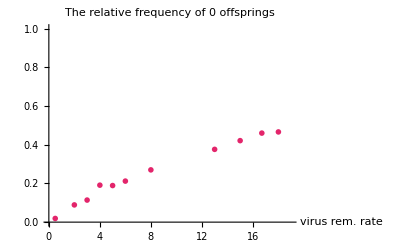

```mathematica
PlotZeroFreq=ListPlot[theoFreqZeroList, 
PlotStyle->{ColorData["Crayola"][zeroFreqColor],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{{0,vrrrangemax},{0,1}},AxesLabel->{"virus rem. rate",""},PlotLabel->"The relative frequency of 0 offsprings"]
```

This looks similar to part of the 1/(1+(a/x)^n) curve -- Hill equation with n=1:

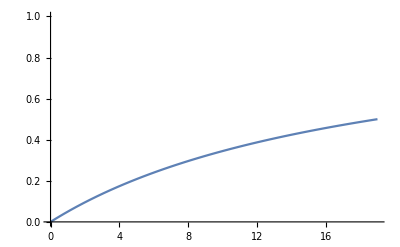

```mathematica
curvePlot=Plot[1/(1+(vrrrangemax/x)),{x,0,vrrrangemax},PlotRange->{0,1}]
```

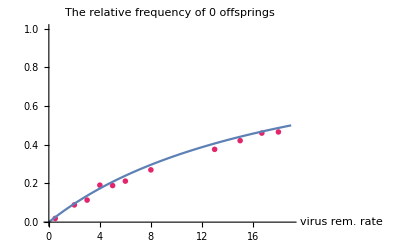

```mathematica
Show[PlotZeroFreq,curvePlot]
```

## The Maximum Likelihood estimate of the parameter of the geometric distribution.

For each virus removal rate value we run a series of experiments and calculate the relative frequency of 0 offsprings.

```mathematica
vrrrangemax=20;
```

```mathematica
MLEstList={{1.67,0.07431},{2.0,0.091424},{3,0.128617},{4,0.167476},{5,0.1970055},{6,0.219202104340201},{8,0.27708506},{13,0.392772},{15,0.443852},{16.7, 0.468603},{18,0.47664}};
```

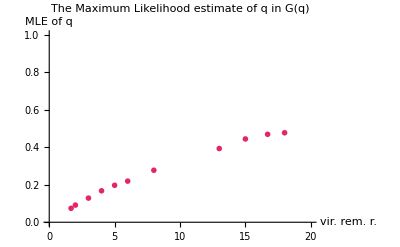

```mathematica
PlotZeroFreq=ListPlot[MLEstList, 
PlotStyle->{ColorData["Crayola"][zeroFreqColor],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{{0,vrrrangemax},{0,1}},AxesLabel->{"vir. rem. r.","MLE of q"},PlotLabel->"The Maximum Likelihood estimate of q in G(q)"]
```

This looks similar to part of the 1/(1+(a/x)^n) curve -- Hill equation with n=1:

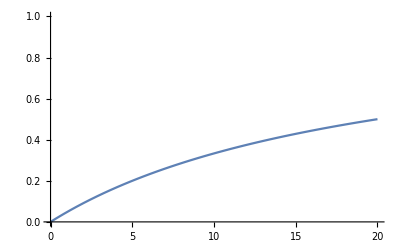

```mathematica
curvePlot=Plot[1/(1+(vrrrangemax/x)),{x,0,vrrrangemax},PlotRange->{0,1}]
```

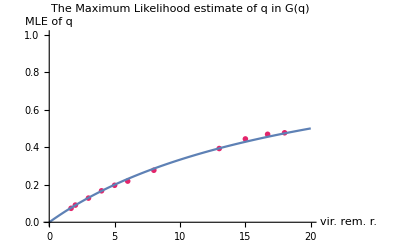

```mathematica
Show[PlotZeroFreq,curvePlot]
```

Observation nr2: at this point we have a concave function.

## Branching processes: the theoretical PoE

Using the above observation regarding a reasonable fit to geometrical distribution, the PoE is given by the fix point of the PGF of the geometrical distribution.

The POE is given by

G_X(q)=q
q / (1 - (1-q)x) = x, thus we have
q = x * (1 - (1-q)x) 

We have a simple second order equation. The non-negative solution to that is:

```mathematica
Rasterize[Plot[N[(1-Sqrt[1-4*(1-(q))*(q)])/(2*(1-(q)))],{q,0,1},PlotLabel->"The G_X(q)=q fixpoint eq.'s solution for geom. distr.",AxesLabel->{"q","PoE"}]]
```

-Graphics-

We have seen that q = q(mu), where we found that q = q(mu) takes the following form: q(mu) = 1 / (1 + 20/mu)

Altogether we have

q / (1 - (1-q)x) = x and
q(mu) = 1 / (1 + 20/mu)

The probability of extinction is given (below on the LHS) as a function of q (the relative frequency of 0 offsprings), and for that to be a linear function of mu we need the following:

```mathematica
Solve[(1-Sqrt[1-4*(1-q)*q])/(2*(1-q))==(1/20)*mu,q]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{q→mu/(20+mu)}}

Which corresponds to what we have previously observed.

## Theoretical linearity

```mathematica
PoE[q_]:=(1-Sqrt[1-4*(1-q)*q])/(2*(1-q))
```

```mathematica
qMLE[mu_]:=1/(1 + 19/mu)
```

```mathematica
POEqMLE={{0.5,PoE[qMLE[0.5]]},{2.0,PoE[qMLE[2.0]]},{3,PoE[qMLE[3.0]]},{4,PoE[qMLE[4.0]]},{5,PoE[qMLE[5]]},{6,PoE[qMLE[6]]},{8,PoE[qMLE[8]]},{13,PoE[qMLE[13]]},{15,PoE[qMLE[15]]},{16.7, PoE[qMLE[16.7]]},{18,PoE[qMLE[18]]},{20,PoE[qMLE[20]]}};
```

```mathematica
experimentalList={{0.5,23/1000},{1.67, 78/1000},{2,95/1000 },{6,288/1000},{8,391/1000},{10,469/1000},{11, 559/1000},{12, 602/1000},{13, 637/1000},{14,714/1000},{15,774/1000},{16, 839/1000},{16.7, 893/1000},{17,912/1000},{18,957/1000},{19,989/1000},{20,997/1000}};
```

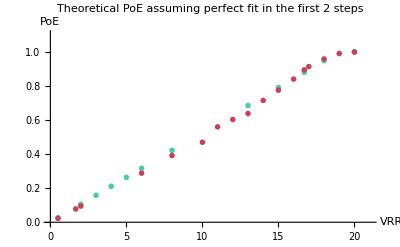

```mathematica
PlotZeroFreqAtF=ListPlot[{POEqMLE,experimentalList}, 
PlotStyle->{{ColorData["Crayola"]["ShamRock"],Thickness[0.010]},{ColorData["Crayola"]["BrickRed"],Thickness[0.010]}},
PlotMarkers->{{●,10}},
PlotRange->{{0,21},{0,1.1}},AxesLabel->{"VRR","PoE"},PlotLabel->"Theoretical PoE assuming perfect fit in the first 2 steps"]
```